V6 :Use Block for faster code(?)

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

# Graphics

## Notations

```mathematica
Needs["Notation`"]
Notation[Subscript[β, a__] ⟺ β[a__]]
Notation[Subscript[R, a__] ⟺ R[a__]]
Notation[Subscript[ϕ, a__] ⟺ ϕ[a__]]
Notation[Subscript[χ, a__] ⟺ χ[a__]]
Notation[Subscript[ψ, a__] ⟺ ψ[a__]]
Notation[Subscript[ξ, a__] ⟺ ξ[a__]]
Notation[(ϕ^*)_a__ ⟺ ϕs[a__]]
Notation[(χ^*)_a__ ⟺ χs[a__]]
Notation[(ψ^*)_a__ ⟺ ψs[a__]]
Notation[(ξ^*)_a__ ⟺ ξs[a__]]
Notation[ϕ^* ⟺ ϕs]
{{Notation[χ^* ⟺ χs]}, {Notation[ψ^* ⟺ ψs]
Notation[ξ^* ⟺ ξs]}}
```

{{Null},{Null^2}}

### Test Notation

```mathematica
V[a]
```

V[a]

```mathematica
β[1,2]
```

β_(1,2)

## MyGraph[]

```mathematica
Clear[MyGraph];
Options[MyGraph]={"undirected" ->True,"label" ->False};
MyGraph[edges__,root_,source_,OptionsPattern[]]:={Module[{locEdges={},i,locWeights={},locRoot=root,locSource=source,p},
Clear[β];

For[i=1, i<=(Dimensions@edges)[[1]],i++,
If[OptionValue["undirected"] && edges[[i,2]] =!=locSource && edges[[i,2]] =!=edges[[i,1]] ,
AppendTo[locEdges,edges[[i,2]]->edges[[i,1]]];
AppendTo[locWeights,β[edges[[i,2]],edges[[i,1]]] ]
];

If[edges[[i,1]]==locSource,Continue[]];

AppendTo[locEdges,edges[[i,1]]->edges[[i,2]]];
AppendTo[locWeights,β[edges[[i,1]],edges[[i,2]]] ]
];

locEdges=Sort[locEdges,(#1[[1]]<=#2[[1]] &&#1[[2]]<=#2[[1]])||(#1[[1]]<#2[[2]] &&#1[[2]]<=#2[[2]]) &];

p[β[a_,b_],β[c_,d_]]:=1/;(a<=c&&b<=c);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<=a&&d<=a);
p[β[a_,b_],β[c_,d_]]:=1/;(a<d&&b<=d);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<b&&d<=b);
locWeights=Sort[locWeights,p];

(*Print[locEdges];
Print[locWeights]*);

If[ OptionValue["label"],
(*True*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, EdgeLabels->"EdgeWeight", VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"],
(*False*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"]]
],
root(*Root*),source(*Source*)}
```

### Usage example of MyGraph[]

“edges” must be a list of ordered pairs containing the vertices of the graph. The edge is intended from the first vertex to the second.
If “directed” is false (optional, default to true), then a undirected graph is drawn

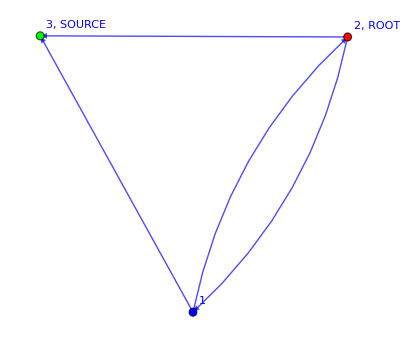

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]]
```

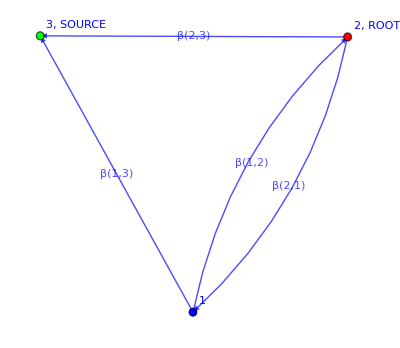

```mathematica
gLabel=MyGraph[edges,root,source,"printEdgesLabel"->True]
```

## DrawOnGraph[]

“Path” should be made of triplets whose first two elements are the initial and final vertices respectively, while the last is the color of this edge

```mathematica
Clear[DrawOnGraph];
Options[DrawOnGraph]={"drawOthers"-> True};
DrawOnGraph[graph_,path__,OptionsPattern[]]:=Module[{locEdges,locPathStyle={},locRoot,locSource,i},
locEdges = EdgeList@graph;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

For[i=1, i<=Length[path],i++,
AppendTo[locPathStyle,{path[[i,1]]->path[[i,2]]->path[[i,3]]}];
(*Print[locPathStyle]*)
];
If[OptionValue["drawOthers"],
(*True*)Graph[locEdges,EdgeStyle->Flatten@{locPathStyle,Blue}, VertexLabels->{locRoot->ToString[locRoot]",ROOT",locSource->ToString[locSource]",SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"],
(*False*)Graph[locEdges,EdgeStyle->Flatten@{locPathStyle,White}, VertexLabels->{locRoot->ToString[locRoot]",ROOT",locSource->ToString[locSource]",SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"]
]
]
```

### Usage example of DrawOnGraph[]

“path” should be an ordered list of pairs of vertices, i.e. edges, that form the desired Laplacian RW

```mathematica
path1={{2,1,Red},{1,3,Green}};
DrawOnGraph[g,path1]
```

PropertyValue::pvobj: g is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~ROOT].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

Part::partw: Part 1 of PropertyValue[] does not exist.

PropertyValue::pvobj: g is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~SOURCE].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

General::stop: Further output of PropertyValue::argrx will be suppressed during this calculation.

Part::partw: Part 1 of PropertyValue[] does not exist.

Graph[EdgeList[g],EdgeStyle→{2->1→RGBColor[1, 0, 0],1->3→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},VertexLabels→{PropertyValue[]⟦1⟧→PropertyValue[][[1]] ,ROOT,PropertyValue[]⟦1⟧→PropertyValue[][[1]] ,SOURCE,Name},VertexStyle→{PropertyValue[]⟦1⟧→RGBColor[1, 0, 0],PropertyValue[]⟦1⟧→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

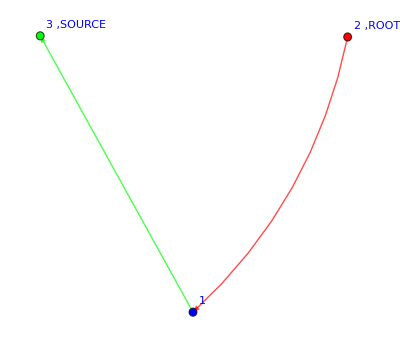

```mathematica
DrawOnGraph[g,path1,"drawOthers"->False]
```

## DrawFromExpression[]

```mathematica
Clear[DrawFromExpression];
Options[DrawFromExpression]={"graph"->g,"drawOthers"->False};

DrawFromExpression[exp_,OptionsPattern[]]:=Module[{terms,graphs={},i},
terms=exp//.R[a_,b_,c_]^n_->R[a,b,c]//Expand;
terms=List @@ (terms+Zeta[3]);
terms=terms//.β[__]->1;
terms=DeleteElements[terms,{Zeta[3]}];
terms=Outer[List,terms];
terms=terms//.Times->List;
terms=monoFlatten@@@terms;
terms=terms//.R[a_,b_,c_]->{a,b,c};
(*For[i=1,i<=Length[terms],i++,
terms[[i]]=DeleteElements[terms[[i]],{a_?NumericQ}];
];*)
Print[terms];

For[i=1,i<=Length[terms],i++,
AppendTo[graphs,DrawOnGraph[OptionValue["graph"],terms[[i,2;;]],"drawOthers"->OptionValue["drawOthers"]]];
Print[graphs[[i]]];
Print[Weight ==terms[[i,1]]];
];
]
```

## AugmentedGraph[]

This is useful to compute the total incoming current from the source towards the DLA cluster/Tree. WE MUST ADD THE EDGE FROM THE OLD SOURCE TO THE NEW SOURCE, AS WELL AS ALLOW THE EDGES FROM THE OLD SOURCE TO THE NEIGHBORS

```mathematica
Clear[AugmentedGraph];
AugmentedGraph[graph_]:=Module[{locVertices,locEdges,locPathStyle={},locRoot,locSource,newSource,oldSourceNeighbors,graphPlus,i},

locVertices = VertexList@graph;
locEdges = EdgeList@graph/.DirectedEdge->List;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

newSource=locVertices[[-1]]+1;

(*Add the edge from the oldSource to the newSource*)
AppendTo[locEdges,{locSource,newSource}];

(*Add all the edges from the oldSource to its neighbors*)
oldSourceNeighbors=Select[locEdges, #[[2]]==locSource &];

For[i=1,i<=Length[oldSourceNeighbors],i++,
AppendTo[locEdges,{locSource,oldSourceNeighbors[[i,1]]}]
];

graphPlus =MyGraph[locEdges,locRoot,newSource,"undirected"->False][[1]];

Return[{graphPlus,locSource,newSource}]
]
```

#### Usage example of AugmentedGraph[]

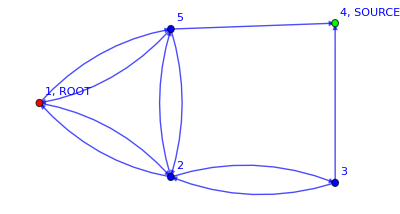

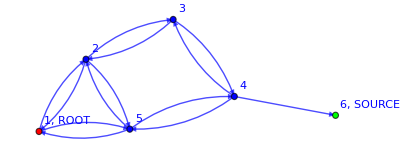
{-Graphics-,4,6}

```mathematica
g=myFavoriteGraph
AugmentedGraph[g]
```

# Field Theory tools

## monoFlatten[]

```mathematica
Clear[monoFlatten];
(*monoFlatten[a_?NumericQ]:={};*)
monoFlatten[a_]:={a};
monoFlatten[{a__}]:={{a}};
monoFlatten[{a__,b__}]:={a,b};
```

#### Test

## ExtractPaths[]

```mathematica
(*To extract the paths and their weights from the expression of an expectation value*)
```

```mathematica
Clear[ExtractPaths];
ExtractPaths[exp_]:=Module[{terms,paths={},i},

terms=exp//Expand;
terms=List @@Collect[terms,R[__,Red]];
terms=Outer[List,terms];

For[i=1,i<=Length[terms],i++,
If[MatchQ[terms[[i,1]],R[__,Red]*A_],
AppendTo[paths,terms[[i]]]
]
];
terms=paths//.R[__,Blue]->1//FullSimplify;

Return[terms]
]
```

#### Usage example of ExtractPaths[]

```mathematica
exp=(1-(Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,2,RGBColor[0, 0, 1]] Subscript[β, 2,3] Subscript[β, 3,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]))+(Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,4,RGBColor[0, 0, 1]] Subscript[β, 1,2] Subscript[β, 2,3] Subscript[β, 3,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[R, 2,5,RGBColor[0, 0, 1]] Subscript[R, 5,2,RGBColor[0, 0, 1]] Subscript[β, 2,5] Subscript[β, 5,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,4,RGBColor[0, 0, 1]] Subscript[R, 5,2,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 2,3] Subscript[β, 3,4] Subscript[β, 5,2])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[0, 0, 1]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,2] Subscript[β, 2,5] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,2,RGBColor[0, 0, 1]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 2,3] Subscript[β, 3,2] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4])));ExtractPaths[exp]
```

{{(R_(1,2,RGBColor[1, 0, 0]) β_(1,2) (β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))},{(R_(1,5,RGBColor[1, 0, 0]) β_(1,5) ((β_(2,1)+β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,2)+β_(5,4))))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))}}

## Vertex rules and VertexAssignment[]

The vertices are where the interaction takes place in the field theory.

```mathematica
Clear[V];
V[1.]:=1.;
V[1]:=1.;
(*V[0]:=0;*)
V'[a_]:=1.
```

```mathematica
Clear[VertexAssignment];
Options[VertexAssignment]={"system"->"LERW","print"->False,"excludedVertices"->{},"sourceBC"->1};

VertexAssignment[graph_,OptionsPattern[]]:=Module[{locVertices,locWeights,totWeights,locSource,action,x,y},
Clear[i];
locVertices=VertexList@graph;
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

(*LERW*)
If[OptionValue["system"]=="LERW",
If[OptionValue["print"],Print["#####   "<>OptionValue["system"]<>"   #####"]];
action = Product[ If[totWeights[[x]]===0 || MemberQ[OptionValue["excludedVertices"],x],1,V[(1+ Sum[locWeights[[x,y]]/totWeights[[x]] χs[y,Subscript[i, x]]χ[x,Subscript[i, x]],{y,Length[locVertices]}] ) ]],{x,Length[locVertices]}];
action*=V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[i, s]])];(*This is the BC*)
Return[action]];

(*DLA*)
If[OptionValue["system"]=="DLA",If[OptionValue["print"],Print["#####   "<>OptionValue["system"]<>"   #####"]];
Return[
Product[ If[totWeights[[x]]===0 || MemberQ[OptionValue["excludedVertices"],x],1,V[(1+ Product[1+locWeights[[x,y]]/totWeights[[x]] χs[y,Subscript[i, x]],{y,Length[locVertices]}] χ[x,Subscript[i, x]]+ Sum[locWeights[[x,y]]/totWeights[[x]] ϕs[y,Subscript[j, x]]ϕ[x,Subscript[j, x]],{y,Length[locVertices]}])] ],{x,Length[locVertices]}]
]]
]
```

### Usage example of VertexAssignment[]

```mathematica
Z=VertexAssignment[g[[1]],"system"->"LERW"]
```

(1+χ[4,i_s]) (1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])) (1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])) (1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4]))

```mathematica
VertexAssignment[g[[1]],"system"->"LERW","excludedVertices"->{1}]
```

(1+χ[4,i_s]) (1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])) (1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4]))

## δrules

```mathematica
ClearAll[Σδrule]
Σδrule={δ[a_,b_]^n_/;(!NumericQ[b]&& !MatchQ[b,Subscript[1, __]]):>δ[a,b]^(n-2)δ[a,a],
δ[b_,a_]δ[c_,b_]/;(!NumericQ[b] && !MatchQ[b,Subscript[1, __]]):>δ[c,a],
δ[a_,b_]δ[c_,b_]/;(!NumericQ[b]&& !MatchQ[b,Subscript[1, __]]):>δ[a,c],
δ[a_,a_]/;(MatchQ[a,Subscript[i, __]])/;(a=!=Subscript[i, s]):>n,
δ[a_,a_]/;(MatchQ[a,Subscript[k, _]]):>1,
δ[a_,a_]/;(MatchQ[a,Subscript[l, _]]):>1};
```

```mathematica
ClearAll[δruleExternal]
δruleExternal={δ[a_,a_]/;(NumericQ[a] || a==Subscript[i, s] || MatchQ[a,Subscript[j, __]] || MatchQ[a,Subscript[1, __]]||MatchQ[a,Subscript[k, _]]):>1,
δ[a_,b_]/;(NumericQ[a] ||MatchQ[a,Subscript[k, _]]|| MatchQ[a,Subscript[j, __]]|| MatchQ[a,Subscript[1, _]])/;(a=!=b):>0,
δ[a_,b_]/;(NumericQ[b] ||MatchQ[b,Subscript[k, _]]|| MatchQ[b,Subscript[j, __]]|| MatchQ[b,Subscript[1, _]])/;(a=!=b):>0 };
```

### Usage examples of the δrules

```mathematica
δ[b,a]δ[c,b]/.Σδrule
```

δ[c,a]

```mathematica
δ[b,a]δ[a,b]//.Σδrule
```

n

```mathematica
δ[b,a]δ[c,a]δ[c,b]//.Σδrule
```

n

```mathematica
δ[1,i]δ[i,1]//.Σδrule//.δruleExternal
```

1

```mathematica
δ[1,i]δ[i,2]//.Σδrule//.δruleExternal
```

0

```mathematica
δ[1,i]δ[i,1]δ[a,b]δ[a,b]//.Σδrule//.δruleExternal
```

δ[a,a]

```mathematica
δ[Subscript[k, 1],Subscript[k, 1]]//.Σδrule
```

m

```mathematica
δ[Subscript[i, 1],Subscript[i, 1]]//.Σδrule
```

n

```mathematica
δ[Subscript[j, -1],Subscript[j, -1]]//.δruleExternal
```

1

```mathematica
δ[Subscript[k, -1],Subscript[k, -1]]//.δruleExternal
```

1

```mathematica
δ[Subscript[1, 1],Subscript[1, -1]]δ[Subscript[1, 1],Subscript[1, -1]]//.Σδrule
```

δ[1_1,1_-1]^2

## Operator “vertices” rules

```mathematica
Clear[Op];
Op[1]:=1;
Op[0]:=0;
Op'[_]:=1
```

## FieldsNamesGenerator[]

```mathematica
Clear[FieldsNamesGenerator];
FieldsNamesGenerator[fields_]:=
FieldsNamesGenerator[fields]=Block[{locFields={},starFields={},deltaFields={},deltaStarFields={},l},

locFields=fields;

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]];
];(*End of loop to define the fields*)

Return[{locFields,starFields,deltaFields,deltaStarFields}]
]
```

#### Test

```mathematica
fields={ϕ,χ};
FieldsNamesGenerator[fields]//AbsoluteTiming
FieldsNamesGenerator[fields]//AbsoluteTiming
```

{0.0000616,{{ϕ,χ},{ϕ^*,χ^*},{δϕ,δχ},{δϕs,δχs}}}

{3.1×10^-6,{{ϕ,χ},{ϕ^*,χ^*},{δϕ,δχ},{δϕs,δχs}}}

## WickContraction[]

NOW IT WORKS, but only up to a 2-point function!!!!!!!!

```mathematica
Clear[WickContraction];
Options[WickContraction]={"print"->False,"fields"->{χ}, "endTime"->1};

WickContraction[A_ +B_,OptionsPattern[]]:=WickContraction[A,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"]]+WickContraction[B,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"]];

WickContraction[Op[A_ +B_]*C_,OptionsPattern[]]:=WickContraction[Op[A]C,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"]]+WickContraction[Op[B]C,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"]];

WickContraction[A_?NumericQ,OptionsPattern[]]:=A;


(*################################################################################
									Expectation Values                             
##############################################################################*)
(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)
WickContraction[Op[A_] *B_, OptionsPattern[]]:=Module[{locFields={}, starFields={}, deltaFields={},deltaStarFields={},contributions=0,z,zTemp,κ,j,l,timeIndex},
z=Op[A]B;

If[OptionValue["print"],
Print["###################  Operator found  ##################"];
];


locFields=OptionValue["fields"];

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]];
];(*End of loop to define the fields*)

If[OptionValue["print"],
Print[locFields,starFields,deltaFields,deltaStarFields];
];

For[timeIndex=0,timeIndex<=(OptionValue["endTime"]-1),timeIndex++,

(*
If[timeIndex==0, 
(*TRUE*)If[OptionValue["endTime"]==0,timeIndex++,Continue[]],
(*FALSE*)z=z//.f_[x_,Subscript[t, timeIndex],a_]->f[x,a];
];*)

If[OptionValue["print"],
Print["###################  Time "<> ToString[timeIndex+1]<>"  ##################"];
Print[z]
];

If[OptionValue["endTime"]!=0,
(*TRUE*)z=z//.f_[x_,Subscript[t, (timeIndex+1)],a_]->f[x,a]
];

(*Start of loop over fields*)
For[l=1,l<=Length[locFields],l++,

(*Start of loop over space*)
For[j=1,j<=100,j++,
(*First contribution*)
zTemp=z//.locFields[[l]][j,a_]->0//.starFields[[l]][j,a_]->0;
If[zTemp-z=!=0,
contributions=zTemp;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": First contribution ####"];
Print[contributions]]
];

(*Second contribution*)
zTemp=z/. locFields[[l]][j,a_]->locFields[[l]][j,a]+κ *deltaFields[[l]][j,a];
If[zTemp-z=!=0,
z=D[zTemp,κ]/.κ->0;
];

zTemp=z/. starFields[[l]][j,a_]->starFields[[l]][j,a]+κ *deltaStarFields[[l]][j,a];
If[zTemp-z=!=0,
z=D[zTemp,κ]/.κ->0;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": second contribution ####"];
Print[z]
]
];

z=Expand[z];
zTemp=z//.deltaFields[[l]][j,a_]*deltaStarFields[[l]][j,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b];

If[zTemp-z=!=0,
If[OptionValue["print"],
Print["#### Contraction "<>ToString[j]<>" ####"];
Print[z=zTemp]
]
];
z=zTemp/.deltaFields[[l]][j,a_]->0/.deltaStarFields[[l]][j,b_]->0;


If[contributions-z=!=0,
contributions+=z;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": total contribution ####"];
Print[contributions]]
];

z=contributions;
contributions=0;

];(*End of loop over space*)

z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0;

z=z//.Σδrule;
];(*End of loop over fields*)

(*
For[l=1,l<=Length[locFields],l++,
z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0;
];*)

];(*End of loop over time*)

Return[z]
];


(*################################################################################
									Partition Function                             
##############################################################################*)
(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)

WickContraction[V[A_] *B_, OptionsPattern[]]:=Module[{locFields={}, starFields={}, deltaFields={},deltaStarFields={},contributions=0,z,zTemp,κ,j,l,timeIndex},
z=V[A]B;

If[OptionValue["print"],
Print["###################  Partition Function  ##################"];
];


(* Updated version with FieldsNamesGenarator
locFields=OptionValue["fields"];

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]]
];(*End of loop to define the fields*)
*)


locFields=OptionValue["fields"][[1]];
starFields=OptionValue["fields"][[2]];
deltaFields=OptionValue["fields"][[3]];
deltaStarFields=OptionValue["fields"][[4]];

If[OptionValue["print"],
Print[locFields,starFields,deltaFields,deltaStarFields]
];

(*Start a loop over fields*)
For[timeIndex=0,timeIndex<=(OptionValue["endTime"]-1),timeIndex++,

(*If[timeIndex==0, 
(*TRUE*)If[OptionValue["endTime"]==0,timeIndex++,Continue[]],
(*FALSE*)z=z//.f_[x_,Subscript[t, timeIndex],a_]->f[x,a];
];*)

If[OptionValue["print"],
Print["###################  Time "<> ToString[timeIndex+1]<>"  ##################"];
Print["Z before"];
Print[z]
];

z=z//.f_[x_,Subscript[t, (timeIndex+1)],a_]->f[x,a];

(*If[OptionValue["endTime"]!=0,
(*TRUE*)z=z//.f_[x_,Subscript[t, (timeIndex+1)],a_]->f[x,a]
];*)

If[OptionValue["print"],
Print["Z After"];
Print[z]
];

(*Start of loop over fields*)
For[l=1,l<=Length[locFields],l++,

(*Start of loop over space*)
For[j=1,j<=100,j++,

(*First contribution*)
zTemp=z//.locFields[[l]][j,a_]->0//.starFields[[l]][j,a_]->0;
If[zTemp-z=!=0,
contributions=zTemp;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": First contribution ####"];
Print[contributions]]
];

(*Second contribution*)
zTemp=z/. locFields[[l]][j,a_]->locFields[[l]][j,a]+κ *deltaFields[[l]][j,a];
If[zTemp-z=!=0,
z=D[zTemp,κ]/.κ->0;
];

zTemp=z/. starFields[[l]][j,a_]->starFields[[l]][j,a]+κ *deltaStarFields[[l]][j,a];
If[zTemp-z=!=0,
z=D[zTemp,κ]/.κ->0;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": second contribution ####"];
Print[z]
]
];

z=Expand[z];
zTemp=z//.deltaFields[[l]][j,a_]*deltaStarFields[[l]][j,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b];

If[zTemp-z=!=0,
If[OptionValue["print"],
Print["#### Contraction "<>ToString[j]<>" ####"];
Print[z=zTemp]
]
];

z=zTemp/.deltaFields[[l]][j,a_]->0/.deltaStarFields[[l]][j,b_]->0;


If[contributions-z=!=0,
contributions+=z;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": total contribution ####"];
Print[contributions]]
];

z=contributions;
contributions=0;

];(*End of loop over space*)

z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0;

];(*End of loop over fields*)

(*For[l=1,l<=Length[locFields],l++,
z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0
];*)

z=z//.Σδrule;

];(*End of loop over time*)

Return[z]
];
```

### Usage example of WickContraction[]

Simple

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source];
Z=VertexAssignment[g[[1]],"system"->"LERW"];
WickContraction[Z]/.n->-1
```

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
WickContraction[Z,"endTime"->1]/.n->-1
```

2-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

More complex example CORRECT!!

```mathematica
edges={{1,3},{1,2},{2,2},{2,3}};
root=1;
source=3;
g=MyGraph[edges,root,source];
g[[1]];
Z=VertexAssignment[g[[1]]]
WickContraction[Z]/.n->-1
```

V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,2]+β[2,3])+(β[2,2] χ[2,i_2] χs[2,i_2])/(β[2,1]+β[2,2]+β[2,3])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,2]+β[2,3])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,2]+β[2,3]))-β[2,2]/(β[2,1]+β[2,2]+β[2,3])

Regular 2x2 lattice with absorption (i.e. source) at 4

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source];
g[[1]];
Z=VertexAssignment[g[[1]]]

WickContraction[Z]/.n->-1
```

V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

## WickContractionBlock[]

```mathematica
Clear[WickContractionBlock];
Options[WickContractionBlock]={"print"->False,"fields"->{χ}, "endTime"->1,"#vertices"->10};

WickContractionBlock[A_ +B_,OptionsPattern[]]:=WickContractionBlock[A,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"]]+
WickContractionBlock[B,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"]];

WickContractionBlock[Op[A_ +B_]*C_,OptionsPattern[]]:=WickContractionBlock[Op[A]C,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"]]+
WickContractionBlock[Op[B]C,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"]];

WickContractionBlock[A_?NumericQ,OptionsPattern[]]:=A;

(*################################################################################
									Partition Function                             
##############################################################################*)
(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)

WickContractionBlock[V[A_] *B_, OptionsPattern[]]:=Block[{locFields={}, starFields={}, deltaFields={},deltaStarFields={},contributions=0,z,zTemp,κ,j,l,timeIndex},

z=V[A]B;

(*
If[OptionValue["print"],
Print["###################  Partition Function  ##################"];
];*)

(* Updated version with FieldsNamesGenarator
locFields=OptionValue["fields"];

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]]
];(*End of loop to define the fields*)
*)

locFields=OptionValue["fields"][[1]];
starFields=OptionValue["fields"][[2]];
deltaFields=OptionValue["fields"][[3]];
deltaStarFields=OptionValue["fields"][[4]];


(*Start a loop over time*)
For[timeIndex=0,timeIndex<=(OptionValue["endTime"]-1),timeIndex++,

(*If[timeIndex==0, 
(*TRUE*)If[OptionValue["endTime"]==0,timeIndex++,Continue[]],
(*FALSE*)z=z//.f_[x_,Subscript[t, timeIndex],a_]->f[x,a];
];*)

(*
If[OptionValue["print"],
Print["###################  Time "<> ToString[timeIndex+1]<>"  ##################"];
Print["Z before"];
Print[z]
];*)

z=z//.f_[x_,Subscript[t, (timeIndex+1)],a_]->f[x,a];

(*
If[OptionValue["endTime"]!=0,
(*TRUE*)z=z//.f_[x_,Subscript[t, (timeIndex+1)],a_]->f[x,a]
];*)

(*
If[OptionValue["print"],
Print["Z After"];
Print[z]
];*)

(*Start of loop over fields*)
For[l=1,l<=Length[locFields],l++,

(*Start of loop over space*)
For[j=1,j<=OptionValue["#vertices"],j++,

(*First contribution*)
zTemp=z//.locFields[[l]][j,a_]->0//.starFields[[l]][j,a_]->0;
If[zTemp-z=!=0,
contributions=zTemp;
(*
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": First contribution ####"];
Print[contributions]]*)
];

(*Second contribution*)
zTemp=z/. locFields[[l]][j,a_]->locFields[[l]][j,a]+κ *deltaFields[[l]][j,a];
If[zTemp-z=!=0,
z=D[zTemp,κ]/.κ->0;
];

zTemp=z/. starFields[[l]][j,a_]->starFields[[l]][j,a]+κ *deltaStarFields[[l]][j,a];
If[zTemp-z=!=0,
z=D[zTemp,κ]/.κ->0;
(*
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": second contribution ####"];
Print[z]
]*)
];

z=Expand[z];
zTemp=z//.deltaFields[[l]][j,a_]*deltaStarFields[[l]][j,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b];

(*
If[zTemp-z=!=0,
If[OptionValue["print"],
Print["#### Contraction "<>ToString[j]<>" ####"];
Print[z=zTemp]
]
];*)

z=zTemp/.deltaFields[[l]][j,a_]->0/.deltaStarFields[[l]][j,b_]->0;


If[contributions-z=!=0,
contributions+=z;
(*
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": total contribution ####"];
Print[contributions]]*)
];

z=contributions;
contributions=0;

];(*End of loop over space*)

z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0;

];(*End of loop over fields*)

(*For[l=1,l<=Length[locFields],l++,
z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0
];*)

z=z//.Σδrule;

];(*End of loop over time*)

Return[z]
];
```

### WickContraction[] vs WickContractionBlock[] speed test

Simple

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source];
Z=VertexAssignment[g[[1]],"system"->"LERW"];
(WickContraction[Z,"fields"->FieldsNamesGenerator[{χ}]]/.n->-1)//AbsoluteTiming
```

{0.0088958,1.-(1. β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))}

```mathematica
FieldsNamesGenerator[{χ}]
```

{{χ},{χ^*},{δχ},{δχs}}

```mathematica
(WickContractionBlock[Z,"fields"->FieldsNamesGenerator[{χ}], "endTime"->1]/.n->-1)//AbsoluteTiming
```

{0.0014643,1.-(1. β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))}

More complex example CORRECT!!

```mathematica
edges={{1,3},{1,2},{2,2},{2,3}};
root=1;
source=3;
g=MyGraph[edges,root,source][[1]];
g;
Z=VertexAssignment[g]
WickContractionBlock[Z,"fields"->{χ}, "endTime"->1]/.n->-1
```

V[1+χ_(3,i_s)] V[1+(β_(1,2) χ_(1,i_1) (χ^*)_(2,i_1))/(β_(1,2)+β_(1,3))+(β_(1,3) χ_(1,i_1) (χ^*)_(3,i_1))/(β_(1,2)+β_(1,3))] V[1+(β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,2)+β_(2,3))+(β_(2,2) χ_(2,i_2) (χ^*)_(2,i_2))/(β_(2,1)+β_(2,2)+β_(2,3))+(β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,2)+β_(2,3))]

1.-(1. β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,2)+β_(2,3)))-(1. β_(2,2))/(β_(2,1)+β_(2,2)+β_(2,3))

Regular 2x2 lattice with absorption (i.e. source) at 4

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source];
g[[1]];
Z=VertexAssignment[g[[1]]]

WickContraction[Z]/.n->-1
```

V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

## ExpectationValue[]

```mathematica
Clear[ExpectationValue];
Options[ExpectationValue]={"operator"->1,"print"->False, "fields"->{χ},"endTime"->1,"draw"->False,"graph"->g, "Rrule"->{R[__]->1},"externalδ"->True};

ExpectationValue[Z_,OptionsPattern[]]:=Module[{z,terms,graphs={},i},
If[OptionValue["operator"]===1,
(*True*)z=WickContraction[Z,
"print"->OptionValue["print"], 
"fields"->OptionValue["fields"],
"endTime"->OptionValue["endTime"]
],
(*False*)z=WickContraction[Z*Op[OptionValue["operator"]],
"print"->OptionValue["print"], 
"fields"->OptionValue["fields"],
"endTime"->OptionValue["endTime"]
]/WickContraction[Z, "fields"->OptionValue["fields"],"endTime"->OptionValue["endTime"]]
];

If[OptionValue["externalδ"],
z=z//.δruleExternal];
z=z/.n->-1;
z=z/.m->0;

If[OptionValue["draw"],
(*True*)
z=z//.R[a_,b_,c_]^n_->R[a,b,c];
terms=List @@ (z+Zeta[3]);
terms=terms//.β[__]->1;
terms=DeleteElements[terms,{Zeta[3]}];
terms=Outer[List,terms];
terms=terms//.Times->List;
terms=monoFlatten@@@terms;
terms=terms//.R[a_,b_,c_]->{a,b,c};
(*For[i=1,i<=Length[terms],i++,
terms[[i]]=DeleteElements[terms[[i]],{a_?NumericQ}];
];*)
Print[terms];
z=z/.R[___]->1;

For[i=1,i<=Length[terms],i++,
AppendTo[graphs,DrawOnGraph[OptionValue["graph"],terms[[i,2;;]],"drawOthers"->False]];
Print[graphs[[i]]];
Print[Weight ==terms[[i,1]]];
];,

(*False*)z=z/.OptionValue["Rrule"]];

Return[z]]
```

### Usage example of ExpectationValue[]

Simple triangular graph

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source];
Z=VertexAssignment[g[[1]],"system"->"LERW"]
ExpectationValue[Z]
```

V[1+χ[3,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,3])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,3])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

2-point function

```mathematica
ExpectationValue[Z,"operator"->χs[1,1]χ[3,1]](*/.β[__]->1*)(*Correct*)
```

###################  Operator found  ##################

(β[1,3]/(β[1,2]+β[1,3])+(β[1,2] β[2,3])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3])))/(1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3])))

Attempts

```mathematica
z=Z Op[χs[1,1]χ[3,1]]
contributions=z;

(*At 1*)
zTemp=z/. χ[1,a_]->χ[1,a]+κ *δχ[1,a];
z=D[zTemp,κ]/.κ->0;

zTemp=z/. χs[1,a_]->χs[1,a]+κ *δχs[1,a];

z=D[zTemp,κ]/.κ->0;

z=Expand[z];
zTemp=z//.δχ[1,a_]*δχs[1,b_]/;(!NumericQ[a*b]):>δ[a,b];


z=zTemp/.δχ[1,a_]->0/.δχs[1,b_]->0;

contributions+=z;
z=contributions;

(*At 2*)
zTemp=z/. χ[2,a_]->χ[2,a]+κ *δχ[2,a];
z=D[zTemp,κ]/.κ->0;

zTemp=z/. χs[2,a_]->χs[2,a]+κ *δχs[2,a];

z=D[zTemp,κ]/.κ->0;

z=Expand[z];
zTemp=z//.δχ[2,a_]*δχs[2,b_]/;(!NumericQ[a*b]):>δ[a,b];


z=zTemp/.δχ[2,a_]->0/.δχs[2,b_]->0;

contributions+=z;
z=contributions;

(*At 3*)
zTemp=z/. χ[3,a_]->χ[3,a]+κ *δχ[3,a];
z=D[zTemp,κ]/.κ->0;

zTemp=z/. χs[3,a_]->χs[3,a]+κ *δχs[3,a];

z=D[zTemp,κ]/.κ->0;

z=Expand[z];
zTemp=z//.δχ[3,a_]*δχs[3,b_]/;(!NumericQ[a*b]):>δ[a,b];


z=zTemp/.δχ[3,a_]->0/.δχs[3,b_]->0;

contributions+=z;
z=contributions;
z=z//.{χ[x_,a_]->0,χs[x_,b_]->0};
z=z//.Σδrule;
z=z//.δruleExternal;
z=z/.n->-1
```

Op[χ[3,1] χs[1,1]] V[1+χ[3,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,3])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,3])]

β[1,3]/(β[1,2]+β[1,3])+(β[1,2] β[2,3])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
z=Z Op[χs[1,1]χ[3,1]]
contributions=z;

For[j=1,j<=3,j++,
(*Print["#### "<>ToString[j]<>" ####"];
Print[z]*)

zTemp=z/. χ[j,a_]->χ[j,a]+κ *δχ[j,a];
z=D[zTemp,κ]/.κ->0;

zTemp=z/. χs[j,a_]->χs[j,a]+κ *δχs[j,a];

z=D[zTemp,κ]/.κ->0;

z=Expand[z];
zTemp=z//.δχ[j,a_]*δχs[j,b_]/;(!NumericQ[a*b]):>δ[a,b];

z=zTemp/.δχ[j,a_]->0/.δχs[j,b_]->0;

contributions+=z;
z=contributions
]

z=z//.{χ[x_,a_]->0,χs[x_,b_]->0};
z=z//.Σδrule;
z=z//.δruleExternal;
z=z/.n->-1
```

Op[χ[3,1] χs[1,1]] V[1+χ[3,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,3])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,3])]

β[1,3]/(β[1,2]+β[1,3])+(β[1,2] β[2,3])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

1-point function

```mathematica
Z=VertexAssignment[g[[1]],"system"->"LERW","excludedVertices"->{2,3}]

ExpectationValue[Z]
ExpectationValue[Z,"operator"->χs[1,Subscript[i, s]]]
```

V[1+χ[3,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])]

1

###################  Operator found  ##################

β[1,3]/(β[1,2]+β[1,3])

More complex example CORRECT!!

```mathematica
edges={{1,3},{1,2},{2,2},{2,3}};
root=1;
source=3;
g=MyGraph[edges,root,source];
g[[1]];
Z=VertexAssignment[g[[1]]]
ExpectationValue[Z]
```

V[1+χ[3,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,2]+β[2,3])+(β[2,2] χ[2,i_2] χs[2,i_2])/(β[2,1]+β[2,2]+β[2,3])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,2]+β[2,3])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,2]+β[2,3]))-β[2,2]/(β[2,1]+β[2,2]+β[2,3])

Regular 2x2 lattice with absorption (i.e. source) at 4

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source];
g[[1]];
Z=VertexAssignment[g[[1]]]

ExpectationValue[Z]
```

V[1+χ[4,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
Z=VertexAssignment[myFavoriteGraph]

ExpectationValue[Z]
```

V[1+χ[4,i_s]] V[1+(β[3,2] χ[3,i_3] χs[2,i_3])/(β[3,2]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,2]+β[3,4])] V[1+(β[5,1] χ[5,i_5] χs[1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,2] χ[5,i_5] χs[2,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,4] χ[5,i_5] χs[4,i_5])/(β[5,1]+β[5,2]+β[5,4])] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,5])+(β[1,5] χ[1,i_1] χs[5,i_1])/(β[1,2]+β[1,5])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,5] χ[2,i_2] χs[5,i_2])/(β[2,1]+β[2,3]+β[2,5])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]))-(β[2,3] β[3,2])/((β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]))-(β[1,5] β[5,1])/((β[1,2]+β[1,5]) (β[5,1]+β[5,2]+β[5,4]))-(β[1,2] β[2,5] β[5,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))+(β[1,5] β[2,3] β[3,2] β[5,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4]))-(β[1,5] β[2,1] β[5,2])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))-(β[2,5] β[5,2])/((β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))

This can also be used for observables

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source];
g[[1]];
Z=VertexAssignment[g[[1]]]

ExpectationValue[Z]/.β[__]->1
```

V[1+χ[4,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4])]

1/2

Two-point function OK

```mathematica
ExpectationValue[Z,"operator"->1]/.β[__]->1
0
Z Op[χs[1,1]χ[4,1]]
ExpectationValue[Z,"operator"->χs[1,1]χ[4,1],"print"->False](*/.β[__]->1*)
```

1/2

0

Op[χ[4,1] χs[1,1]] V[1+χ[4,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4])]

###################  Operator found  ##################

((β[1,2] β[2,4])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))+(β[1,3] β[3,4])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4])))/(1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4])))

One point function OK

```mathematica
Z=VertexAssignment[g[[1]],"system"->"LERW","excludedVertices"->{2,4}]

ExpectationValue[Z]
```

V[1+χ[4,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4])]

1-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

```mathematica
ExpectationValue[Z,"operator"->χs[4,Subscript[i, s]]]/.β[__]->1
```

###################  Operator found  ##################

1

```mathematica
ExpectationValue[Z,"operator"->χs[1,Subscript[i, s]]]/.β[__]->1
```

###################  Operator found  ##################

1/3

```mathematica
ExpectationValue[Z,"operator"->χs[3,Subscript[i, s]]]/.β[__]->1
```

###################  Operator found  ##################

2/3

```mathematica
ExpectationValue[Z,"operator"->χs[2,Subscript[i, s]]]/.β[__]->1
```

###################  Operator found  ##################

0

4-point function NOT OK

```mathematica
ExpectationValue[Z,"operator"->1]/.β[__]->1
0
Z Op[χs[1,1]χ[2,1]χs[2,2]χ[4,2]]
ExpectationValue[Z ,"operator"->χs[3,1]χ[1,1]χs[1,2]χ[2,2]χs[2,3]χ[4,3],"print"->False]/.β[__]->1
```

1/2

0

Op[χ[2,1] χ[4,2] χs[1,1] χs[2,2]] V[1+χ[4,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4])]

###################  Operator found  ##################

3/4

```mathematica
ExpectationValue[Z ,"operator"->χs[3,1]χ[4,1],"print"->False]/.β[__]->1
```

###################  Operator found  ##################

1

```mathematica
(*NOT CORRECT! WORKS WITH STANDARD EXPAND*)
```

Test with different fields

Only χ’s

```mathematica
Z=Op[χs[2,1] χ[4,1] ] V[1+χ[4,Subscript[i, s]]] V[1+(β[1,2] χ[1,Subscript[i, 1]] χs[2,Subscript[i, 1]])/(β[1,2]+β[1,3])+(β[1,3] χ[1,Subscript[i, 1]] χs[3,Subscript[i, 1]])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,Subscript[i, 2]] χs[1,Subscript[i, 2]])/(β[2,1]+β[2,4])+(β[2,4] χ[2,Subscript[i, 2]] χs[4,Subscript[i, 2]])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,Subscript[i, 3]] χs[1,Subscript[i, 3]])/(β[3,1]+β[3,4])+(β[3,4] χ[3,Subscript[i, 3]] χs[4,Subscript[i, 3]])/(β[3,1]+β[3,4])];
ExpectationValue[Z]
```

###################  Operator found  ##################

β[2,4]/(β[2,1]+β[2,4])-(β[1,3] β[2,4] β[3,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]) (β[3,1]+β[3,4]))+(β[1,3] β[2,1] β[3,4])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]) (β[3,1]+β[3,4]))

χ’s and ϕ’s

```mathematica
Z=Op[ϕs[2,1] ϕ[4,1] ] V[1+χ[4,Subscript[i, s]]] V[1+(β[1,2] χ[1,Subscript[i, 1]] χs[2,Subscript[i, 1]])/(β[1,2]+β[1,3])+(β[1,3] χ[1,Subscript[i, 1]] χs[3,Subscript[i, 1]])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,Subscript[i, 2]] χs[1,Subscript[i, 2]])/(β[2,1]+β[2,4])+(β[2,4] ϕ[2,Subscript[i, 2]] ϕs[4,Subscript[i, 2]])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,Subscript[i, 3]] χs[1,Subscript[i, 3]])/(β[3,1]+β[3,4])+(β[3,4] χ[3,Subscript[i, 3]] χs[4,Subscript[i, 3]])/(β[3,1]+β[3,4])];
ExpectationValue[Z,"fields"->{χ,ϕ}]
```

###################  Operator found  ##################

β[2,4]/(β[2,1]+β[2,4])-(β[1,3] β[2,4] β[3,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]) (β[3,1]+β[3,4]))

```mathematica
(*CORRECT!!*)
```

### GeneralizedExpectationValue[] NOT NECESSARY ANY MORE

```mathematica
Clear[GeneralizedExpectationValue];
Options[GeneralizedExpectationValue]={"draw"->False,"graph"->1};

GeneralizedExpectationValue[Z_,OptionsPattern[]]:=Module[{z,terms,i,graphs={}},

z=Z//Expand;
(*z=z//.χ[x_,a_]*χs[x_,b_]/;(MemberQ[{Subscript[i, s]},a]):>δ[a,b]*);
z=z//.ϕ[x_,t__]*ϕs[x_,t__]->R[x,ϕ];
z=z//.{ϕ[__]->0,ϕs[__]->0};

z=z//.ψ[x_,t__]*ψs[x_,t__]->R[x,ψ];
z=z//.{ψ[__]->0,ψs[__]->0};

z=z//.χ[x_,t_,a_]*χs[x_,t_,b_]/;(!NumericQ[a*b]):>δ[a,b]R[x,χ];
z=z//.{χ[__]->0,χs[__]->0};
z=z//.Σδrule;
z=z//.δruleExternal;
z=z/.n->-1;
z=z/.m->0;

If[OptionValue["draw"],
(*True*)
z=z/.R[__]->1;
terms=List @@ z;
terms=Abs[Numerator[terms]];
terms=Outer[List,terms];
terms=terms//.Times->List;
terms=monoFlatten@@@terms;
terms=terms//.β[a_,b_]->{a,b};

For[i=1,i<=Length[terms],i++,
AppendTo[graphs,DrawOnGraph[OptionValue["graph"],terms[[i]],"drawOthers"->False]]
];
Print[graphs],

(*False*)z=z/.R[__]->1];

Return[z]]
```

### Usage example of GeneralizedExpectationValue[]

Simple case

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g
endTime=1;
Z=DynamicLERWaction[g,endTime]
```

-Graphics-

(1+ϕ[1,t_1]) (1+ϕ[2,t_1]) (1+χ[3,t_1,1]) (1+ψ[1,t_1]) (1+ψ[2,t_1]) (1+(β[1,2] χ[1,t_1,i_1] χs[2,t_1,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,t_1,i_1] χs[3,t_1,i_1])/(β[1,2]+β[1,3])+ψ[1,t_1] ψs[1,t_2]+(β[1,2] ϕ[1,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[1,2]+β[1,3])+(β[1,3] ϕ[1,t_1] ϕs[3,t_2] χs[3,t_1,1] ψs[3,t_2])/(β[1,2]+β[1,3])) (1+(β[2,1] χ[2,t_1,i_2] χs[1,t_1,i_2])/(β[2,1]+β[2,3])+(β[2,3] χ[2,t_1,i_2] χs[3,t_1,i_2])/(β[2,1]+β[2,3])+(β[2,1] ϕ[2,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[2,1]+β[2,3])+ψ[2,t_1] ψs[2,t_2]+(β[2,3] ϕ[2,t_1] ϕs[3,t_2] χs[3,t_1,1] ψs[3,t_2])/(β[2,1]+β[2,3]))

```mathematica
GeneralizedExpectationValue[Z]
```

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
GeneralizedExpectationValue[Z,"draw"->True]
```

1-(R[1,χ] R[2,χ] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

Two time-slices

```mathematica
endTime=2;
Z=DynamicLERWaction[g,endTime];
GeneralizedExpectationValue[Z]
%/.β[__]->1
```

1+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

9/16

```mathematica
(*Wich is (Z_t)^2. Correct!!!*)
```

Now let’s add an external field

```mathematica
endTime=1;
Z=DynamicLERWaction[g,endTime];
GeneralizedExpectationValue[Z ϕs[2,Subscript[t, 1]]]
```

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*Which makes sense since I am not considering any step. endTime=1 means that we consider only one time-slice, i.e. the initial position*)
```

```mathematica
endTime=2;
Z=DynamicLERWaction[g,endTime];
GeneralizedExpectationValue[Z ϕs[2,Subscript[t, 1]]]
```

-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*The previous line gives*)-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))
```

-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
%/.β[__]->1
```

3/4

Regular 2x2 lattice with absorption (i.e. source) at 4

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source][[1]];
g;
endTime=1;
Z=DynamicLERWaction[g,endTime]
```

(1+χ[4,t_1,1]) (1+ψ[1,t_1]) (1+ψ[2,t_1]) (1+ψ[3,t_1]) (1+(β[1,2] χ[1,t_1,i_1] χs[2,t_1,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,t_1,i_1] χs[3,t_1,i_1])/(β[1,2]+β[1,3])+ψ[1,t_1] ψs[1,t_2]+(β[1,2] ϕ[1,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[1,2]+β[1,3])+(β[1,3] ϕ[1,t_1] ϕs[3,t_2] χs[3,t_1,1] ψs[3,t_2])/(β[1,2]+β[1,3])) (1+(β[2,1] χ[2,t_1,i_2] χs[1,t_1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,t_1,i_2] χs[4,t_1,i_2])/(β[2,1]+β[2,4])+(β[2,1] ϕ[2,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[2,1]+β[2,4])+ψ[2,t_1] ψs[2,t_2]+(β[2,4] ϕ[2,t_1] ϕs[4,t_2] χs[4,t_1,1] ψs[4,t_2])/(β[2,1]+β[2,4])) (1+(β[3,1] χ[3,t_1,i_3] χs[1,t_1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,t_1,i_3] χs[4,t_1,i_3])/(β[3,1]+β[3,4])+(β[3,1] ϕ[3,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[3,1]+β[3,4])+ψ[3,t_1] ψs[3,t_2]+(β[3,4] ϕ[3,t_1] ϕs[4,t_2] χs[4,t_1,1] ψs[4,t_2])/(β[3,1]+β[3,4]))

```mathematica
GeneralizedExpectationValue[Z]
```

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

Two time-slices (it’s very slow, I would need kay’s trick for the vertices...)

```mathematica
endTime=2;
Z=DynamicLERWaction[g,endTime];
GeneralizedExpectationValue[Z]
```

$Aborted

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]];
```

```mathematica
endTime=1;
Z=DynamicLERWaction[myFavoriteGraph,endTime]
```

(1+χ[4,t_1,1]) (1+ψ[1,t_1]) (1+ψ[2,t_1]) (1+ψ[3,t_1]) (1+ψ[5,t_1]) (1+(β[3,2] χ[3,t_1,i_3] χs[2,t_1,i_3])/(β[3,2]+β[3,4])+(β[3,4] χ[3,t_1,i_3] χs[4,t_1,i_3])/(β[3,2]+β[3,4])+(β[3,2] ϕ[3,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[3,2]+β[3,4])+ψ[3,t_1] ψs[3,t_2]+(β[3,4] ϕ[3,t_1] ϕs[4,t_2] χs[4,t_1,1] ψs[4,t_2])/(β[3,2]+β[3,4])) (1+(β[1,2] χ[1,t_1,i_1] χs[2,t_1,i_1])/(β[1,2]+β[1,5])+(β[1,5] χ[1,t_1,i_1] χs[5,t_1,i_1])/(β[1,2]+β[1,5])+ψ[1,t_1] ψs[1,t_2]+(β[1,2] ϕ[1,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[1,2]+β[1,5])+(β[1,5] ϕ[1,t_1] ϕs[5,t_2] χs[5,t_1,1] ψs[5,t_2])/(β[1,2]+β[1,5])) (1+(β[2,1] χ[2,t_1,i_2] χs[1,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,3] χ[2,t_1,i_2] χs[3,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,5] χ[2,t_1,i_2] χs[5,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,1] ϕ[2,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[2,1]+β[2,3]+β[2,5])+ψ[2,t_1] ψs[2,t_2]+(β[2,3] ϕ[2,t_1] ϕs[3,t_2] χs[3,t_1,1] ψs[3,t_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,5] ϕ[2,t_1] ϕs[5,t_2] χs[5,t_1,1] ψs[5,t_2])/(β[2,1]+β[2,3]+β[2,5])) (1+(β[5,1] χ[5,t_1,i_5] χs[1,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,2] χ[5,t_1,i_5] χs[2,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,4] χ[5,t_1,i_5] χs[4,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,1] ϕ[5,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[5,1]+β[5,2]+β[5,4])+(β[5,2] ϕ[5,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[5,1]+β[5,2]+β[5,4])+(β[5,4] ϕ[5,t_1] ϕs[4,t_2] χs[4,t_1,1] ψs[4,t_2])/(β[5,1]+β[5,2]+β[5,4])+ψ[5,t_1] ψs[5,t_2])

```mathematica
GeneralizedExpectationValue[Z]
```

1-(β[1,2] β[2,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]))-(β[2,3] β[3,2])/((β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]))-(β[1,5] β[5,1])/((β[1,2]+β[1,5]) (β[5,1]+β[5,2]+β[5,4]))-(β[1,2] β[2,5] β[5,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))+(β[1,5] β[2,3] β[3,2] β[5,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4]))-(β[1,5] β[2,1] β[5,2])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))-(β[2,5] β[5,2])/((β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))

## ExpectationValueBlock[]

```mathematica
Clear[ExpectationValueBlock];
Options[ExpectationValueBlock]={"operator"->1,"print"->False, "fields"->{χ},"endTime"->1,"draw"->False,"graph"->g, "Rrule"->{R[__]->1},"externalδ"->True};

ExpectationValueBlock[Z_,OptionsPattern[]]:=Block[{Nvertices,z,terms,graphs={},i},

Nvertices=Length[VertexList@OptionValue["graph"]];

If[OptionValue["operator"]===1,
(*True*)z=WickContractionBlock[Z,
"print"->OptionValue["print"], 
"fields"->OptionValue["fields"],
"endTime"->OptionValue["endTime"],
"#vertices"->Nvertices
],
(*False*)z=WickContractionBlock[Z*Op[OptionValue["operator"]],
"print"->OptionValue["print"], 
"fields"->OptionValue["fields"],
"endTime"->OptionValue["endTime"],
"#vertices"->Nvertices
]/WickContractionBlock[Z, "fields"->OptionValue["fields"],"endTime"->OptionValue["endTime"],
"#vertices"->Nvertices]
];

If[OptionValue["externalδ"],
z=z//.δruleExternal];
z=z/.n->-1;
z=z/.m->0;

If[OptionValue["draw"],
(*True*)
z=z//.R[a_,b_,c_]^n_->R[a,b,c];
terms=List @@ (z+Zeta[3]);
terms=terms//.β[__]->1;
terms=DeleteElements[terms,{Zeta[3]}];
terms=Outer[List,terms];
terms=terms//.Times->List;
terms=monoFlatten@@@terms;
terms=terms//.R[a_,b_,c_]->{a,b,c};
(*For[i=1,i<=Length[terms],i++,
terms[[i]]=DeleteElements[terms[[i]],{a_?NumericQ}];
];*)
Print[terms];
z=z/.R[___]->1;

For[i=1,i<=Length[terms],i++,
AppendTo[graphs,DrawOnGraph[OptionValue["graph"],terms[[i,2;;]],"drawOthers"->False]];
Print[graphs[[i]]];
Print[Weight ==terms[[i,1]]];
];,

(*False*)z=z/.OptionValue["Rrule"]];

Return[z]]
```

### ExpectationValue[] vs ExpectationValueBlock[] speed test

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
g=myFavoriteGraph;
Z=VertexAssignment[g];
ExpectationValue[Z]//AbsoluteTiming
ExpectationValueBlock[Z,"graph"->g]//AbsoluteTiming
```

{0.0649989,1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))}

{0.0150432,1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))}

It  does  seem  to  be  faster  indeed

## LERWtransitionProb[]

This function computes the transition probability as

```mathematica
Clear[LERWtransitionProb];
Options[LERWtransitionProb]={"draw"->False,"print"->False};

LERWtransitionProb[graph_,path__,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,denominator,prob=1, Z,numerator},
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

If[locRoot =!= path[[1,1]], Print["####  WRONG ROOT  ####"]; Return[NULL]];
If[locSource =!= path[[-1,2]], Print["####  WRONG SOURCE  ####"];Return[NULL]];

Module[{locBC={{},{}},ϕ,i=1,j},
locBC={{ϕ[locSource]==1},{locSource}};

For[i=1,i<=Length[path],i++,

Z=VertexAssignment[graph, "excludedVertices"->locBC[[2]]];
Z=ExpectationValue[Z*χs[path[[i,1]],1]];

If[OptionValue["print"],
Print["#####  Previous Partition Function  #####"];
Print[Z]
];

denominator=Z//FullSimplify;


(*Then we need to solve it again with updated BC at the current step*)

AppendTo[locBC[[1]],ϕ[path[[i,1]]]==0];
AppendTo[locBC[[2]],path[[i,1]]];
(*Print[locBC]*);


Z=VertexAssignment[graph, "excludedVertices"->locBC[[2]],"sourceBC"->denominator^-1];
Z=ExpectationValue[Z*χs[path[[i,2]],1] ];

If[OptionValue["print"],
Print["#####  Current Partition Function  #####"];
Print[Z]
];

numerator=locWeights[[path[[i,1]],path[[i,2]]]]/totWeights[[path[[i,1]]]]*Z//FullSimplify;

Print["#####  Transition probability "<>ToString[path[[i,1]]]<>" to "<>ToString[path[[i,2]]]<>"  #####"];
Print[numerator/.β[_,_]->1//FullSimplify];

prob*=numerator//FullSimplify;
]
];
If[OptionValue["draw"],Print[DrawOnGraph[graph,path]]];
Return[prob]
]
```

### Usage example of LaplacianRW[] &LERWtransitionProb[]

“path” should be an ordered list of pairs of vertices, i.e. edges, that form the desired Laplacian RW.
If “draw” is true, then draw the path

Simple cases first

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];

path1={{2,1},{1,3}};
LaplacianRW[g,{{2,1},{1,3}}](*/.β[_,_]->1*)
```

LaplacianRW[-Graphics-,{{2,1},{1,3}}]

```mathematica
(β[1,3] β[2,1])/((β[1,2]+β[1,3]) ((β[1,3] β[2,1])/(β[1,2]+β[1,3])+β[2,3]))//FullSimplify
```

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
%//FullSimplify
```

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
(*Correct!!*)
```

```mathematica
VertexAssignment[g,"excludedVertices"->{2,3}]
LERWtransitionProb[g,path1]
```

(1+χ[3,i_s]) (1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3]))

#####  Transition probability 2 to 1  #####

1/3

#####  Transition probability 1 to 3  #####

1

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
(*Correct!!*)
```

Let’s try with another example, i.e. my favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
PathFinder[myFavoriteGraph]
```

{{{1,2},{2,3},{3,4}},{{1,2},{2,5},{5,4}},{{1,5},{5,2},{2,3},{3,4}},{{1,5},{5,4}}}

#####  Transition probability 1 to 2  #####

5/11

#####  Transition probability 2 to 3  #####

3/5

#####  Transition probability 3 to 4  #####

1

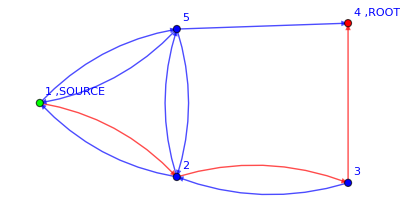

3/11

```mathematica
path2={{1,2},{2,3},{3,4}};
LaplacianRW[myFavoriteGraph,path2,"draw"->True]/.β[_,_]->1
```

```mathematica
LERWtransitionProb[myFavoriteGraph,path2]/.β[_,_]->1
```

#####  Transition probability 1 to 2  #####

5/11

#####  Transition probability 2 to 3  #####

3/5

#####  Transition probability 3 to 4  #####

1

3/11

```mathematica
(*Correct!!!*)
```

# Dynamics

## Znorm[]

```mathematica
Clear[Znorm];
Options[Znorm]={"graph"->g,"fields"->{ϕ,ξ,χ},"theory"->"LERW","βrule"->{β[__]->1.}};

Znorm[expression_,OptionsPattern[]]:=Block[{locZnorm,excludedVertices},

excludedVertices=(expression * 2)/.R[__]->1/.γ->1//Expand;
excludedVertices=List @@excludedVertices;
excludedVertices=excludedVertices[[2;;]]; (*Gets rid of the numerical coefficient*)
excludedVertices=excludedVertices/.SuperStar[ϕ][a_,__]->a;
excludedVertices=excludedVertices/.SuperStar[ψ][a_,__]->a;

locZnorm=VertexAssignment[OptionValue["graph"],"system"->"LERW","excludedVertices"->excludedVertices]/.OptionValue["βrule"];

ExpectationValueBlock[locZnorm,"graph"->OptionValue["graph"]]
]
```

#### Test

```mathematica
g
```

-Graphics-

```mathematica
VertexAssignment[g]
```

V[1+χ_(4,i_s)] V[1+(β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(β_(1,2) χ_(1,i_1) (χ^*)_(2,i_1))/(β_(1,2)+β_(1,5))+(β_(1,5) χ_(1,i_1) (χ^*)_(5,i_1))/(β_(1,2)+β_(1,5))] V[1+(β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))]

```mathematica
ExpectationValue[%]
```

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
%/.β[__]->1
```

11/36

```mathematica
Znorm[+5/18 γ Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[SuperStar[ϕ], 2,Subscript[t, 2],Subscript[k, 1]],"graph"->g]
```

0.833333

```mathematica
Znorm[11/18 γ Subscript[SuperStar[ϕ], 1,Subscript[t, 2],Subscript[k, 1]]]
```

13/18

## DynamicLERWaction[]

This action should be:

For fields that do not have a color index, we default to set it to j_-1, because in the WickContraction[] it automated with color indices.
Instead, the source is set with index 1, so that it can contract with an external “probe”

```mathematica
Clear[DynamicLERWaction];
Options[DynamicLERWaction]={"sourceBC"->1};

DynamicLERWaction[graph_,endTime_,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j];

locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[ If[totWeights[[x]]===0 ,1,(*FALSE*)
V[(1+ Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]ψs[x,Subscript[t, T+1],Subscript[j, -1]]χs[y,Subscript[t, T],1],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]+ ψs[x,Subscript[t, T+1],Subscript[j, -1]]ψ[x,Subscript[t, T],Subscript[j, -1]]) ]],{x,Length[locVertices]}]
V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,endTime}]Product[V[(1+ψ[x,Subscript[t, endTime+1],Subscript[j, -1]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, endTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}];

Return[action]

]
```

### Usage example of DynamicLERWaction[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
endTime=1;
DynamicLERWaction[myFavoriteGraph,endTime]
```

V[1+ϕ[1,t_1]] V[1+ϕ[2,t_1]] V[1+ϕ[3,t_1]] V[1+ϕ[5,t_1]] V[1+χ[4,t_1,1]] V[1+ψ[1,t_1]] V[1+ψ[2,t_1]] V[1+ψ[3,t_1]] V[1+ψ[5,t_1]] V[1+(β[3,2] χ[3,t_1,i_3] χs[2,t_1,i_3])/(β[3,2]+β[3,4])+(β[3,4] χ[3,t_1,i_3] χs[4,t_1,i_3])/(β[3,2]+β[3,4])+(β[3,2] ϕ[3,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[3,2]+β[3,4])+ψ[3,t_1] ψs[3,t_2]+(β[3,4] ϕ[3,t_1] ϕs[4,t_2] χs[4,t_1,1] ψs[4,t_2])/(β[3,2]+β[3,4])] V[1+(β[1,2] χ[1,t_1,i_1] χs[2,t_1,i_1])/(β[1,2]+β[1,5])+(β[1,5] χ[1,t_1,i_1] χs[5,t_1,i_1])/(β[1,2]+β[1,5])+ψ[1,t_1] ψs[1,t_2]+(β[1,2] ϕ[1,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[1,2]+β[1,5])+(β[1,5] ϕ[1,t_1] ϕs[5,t_2] χs[5,t_1,1] ψs[5,t_2])/(β[1,2]+β[1,5])] V[1+(β[2,1] χ[2,t_1,i_2] χs[1,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,3] χ[2,t_1,i_2] χs[3,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,5] χ[2,t_1,i_2] χs[5,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,1] ϕ[2,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[2,1]+β[2,3]+β[2,5])+ψ[2,t_1] ψs[2,t_2]+(β[2,3] ϕ[2,t_1] ϕs[3,t_2] χs[3,t_1,1] ψs[3,t_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,5] ϕ[2,t_1] ϕs[5,t_2] χs[5,t_1,1] ψs[5,t_2])/(β[2,1]+β[2,3]+β[2,5])] V[1+(β[5,1] χ[5,t_1,i_5] χs[1,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,2] χ[5,t_1,i_5] χs[2,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,4] χ[5,t_1,i_5] χs[4,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,1] ϕ[5,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[5,1]+β[5,2]+β[5,4])+(β[5,2] ϕ[5,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[5,1]+β[5,2]+β[5,4])+(β[5,4] ϕ[5,t_1] ϕs[4,t_2] χs[4,t_1,1] ψs[4,t_2])/(β[5,1]+β[5,2]+β[5,4])+ψ[5,t_1] ψs[5,t_2]]

## Evaluation of the DynamicLERWaction[]

Simple case

One time-slice

```mathematica
fields={χ,ϕ,ψ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g;

endTime=1;
Z=DynamicLERWaction[g,endTime];
```

###################  Partition Function  ##################

{{1},{-1/4,{1,2,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]}}}

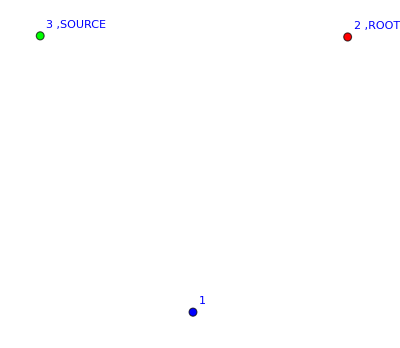

Weight 1

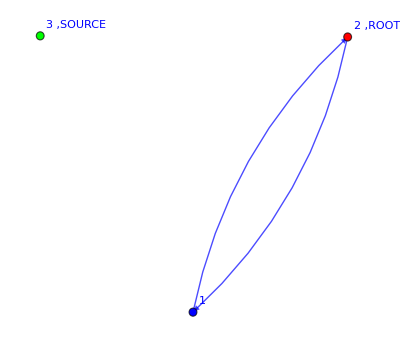

Weight   1
-(-)
  4

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
fields={χ,ϕ,ψ};
endTime=1;
Z=DynamicLERWaction[g,endTime];
ExpectationValue[Z,"fields"->fields,"endTime"->endTime,"print"->False,"draw"->True,"graph"->g]
```

```mathematica
Z//.V[A_]->A;
GeneralizedExpectationValue[%,"draw"->True,"graph"->g]
```

Part::partw: Part 3 of {1,2} does not exist.

Part::partw: Part 3 of {2,1} does not exist.

{-Graphics-,-Graphics-}

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

Two time-slices

```mathematica
endTime=2;
Z=DynamicLERWaction[g,endTime];
Z//.V[A_]->A;
GeneralizedExpectationValue[%]
%/.β[__]->1
```

$Aborted

$Aborted

```mathematica
(*Wich is (Z_t)^2. Correct!!!*)
```

```mathematica
WickContraction[Z,"fields"->fields,"endTime"->endTime]
```

1+V[1+ϕ[1,t_2,0]] V[1+ϕ[2,t_2,0]] V[1+ϕ[3,t_2,0]] V[1+ψ[1,t_2,i_-1]] V[1+ψ[2,t_2,i_-1]] V[1+ψ[3,t_2,i_-1]]+(n R[1,2,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))+(n R[1,2,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] V[1+ϕ[1,t_2,0]] V[1+ϕ[2,t_2,0]] V[1+ϕ[3,t_2,0]] V[1+ψ[1,t_2,i_-1]] V[1+ψ[2,t_2,i_-1]] V[1+ψ[3,t_2,i_-1]] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*IT IS WAAAAAY QUICKER!!!!!!!*)
```

```mathematica
ExpectationValue[Z,"fields"->fields,"endTime"->endTime]
```

1+V[1+ϕ[1,t_3,0]] V[1+ϕ[2,t_3,0]] V[1+ϕ[3,t_3,0]] V[1+ψ[1,t_3,i_-1]] V[1+ψ[2,t_3,i_-1]] V[1+ψ[3,t_3,i_-1]]+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(V[1+ϕ[1,t_3,0]] V[1+ϕ[2,t_3,0]] V[1+ϕ[3,t_3,0]] V[1+ψ[1,t_3,i_-1]] V[1+ψ[2,t_3,i_-1]] V[1+ψ[3,t_3,i_-1]] β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))-(2 V[1+ϕ[1,t_3,0]] V[1+ϕ[2,t_3,0]] V[1+ϕ[3,t_3,0]] V[1+ψ[1,t_3,i_-1]] V[1+ψ[2,t_3,i_-1]] V[1+ψ[3,t_3,i_-1]] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
%/.V[_]->1
```

2+(2 β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(4 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

Now let’s add an external field

With the generalized expectation value

```mathematica
endTime=1;
Z=DynamicLERWaction[g,endTime];
Z//.V[A_]->A;
GeneralizedExpectationValue[%* ϕs[2,Subscript[t, 1],Subscript[i, -1]]]
```

(β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*Which makes sense since I am not considering any step. endTime=1 means that we consider only one time-slice, i.e. the initial position*)
```

```mathematica
endTime=2;
Z=DynamicLERWaction[g,endTime];
```

```mathematica
(*WARNING: VERY SLOW, DO NOT RUN THIS LINE*)GeneralizedExpectationValue[Z ϕs[2,Subscript[t, 1]]]
```

-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*The previous line gives*)-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))
```

-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
%/.β[__]->1
```

3/4

Done with the enhanced WickContraction

###################  Partition Function  ##################

{{},{{1,2,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]}},{{1,2,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]}}}

-Graphics-

-Graphics-

-Graphics-

1+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

###################  Operator found  ##################

{{{1,3,RGBColor[0, 0, 1]},{1,3,RGBColor[1, 0, 0]},{2,1,RGBColor[1, 0, 0]}}}

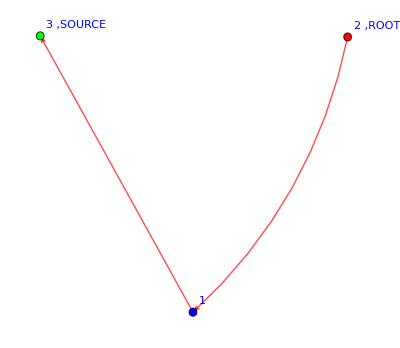

(β[1,3]^2 β[2,1])/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3]))

```mathematica
fields={χ,ϕ,ψ};
endTime=2;
Z=DynamicLERWaction[g,endTime];
ExpectationValue[Z ,"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->True]
Z Op[ϕs[2,Subscript[t, 1],0]];
ExpectationValue[Z Op[ϕs[2,Subscript[t, 1],0]],"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->True]
```

```mathematica
1+V[1+ϕ[1,Subscript[t, 3],0]] V[1+ϕ[2,Subscript[t, 3],0]] V[1+ϕ[3,Subscript[t, 3],0]] V[1+ψ[1,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[2,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[3,Subscript[t, 3],Subscript[i, -1]]]+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(V[1+ϕ[1,Subscript[t, 3],0]] V[1+ϕ[2,Subscript[t, 3],0]] V[1+ϕ[3,Subscript[t, 3],0]] V[1+ψ[1,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[2,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[3,Subscript[t, 3],Subscript[i, -1]]] β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))-(2 V[1+ϕ[1,Subscript[t, 3],0]] V[1+ϕ[2,Subscript[t, 3],0]] V[1+ϕ[3,Subscript[t, 3],0]] V[1+ψ[1,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[2,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[3,Subscript[t, 3],Subscript[i, -1]]] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))/.f_[a_,Subscript[t, 3],b_]->f[a,b];
WickContraction[V[1]*%,"fields"->fields,"endTime"->0]
```

###################  Partition Function  ##################

###################  Partition Function  ##################

###################  Partition Function  ##################

2+WickContraction[(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2),print→False,fields→{χ,ϕ,ψ},endTime→0]+WickContraction[-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3])),print→False,fields→{χ,ϕ,ψ},endTime→0]+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*expected*)
```

```mathematica
ϕs[2,Subscript[t, 1],0](β[2,1] ϕ[2,Subscript[t, 1],Subscript[k, 2]] ϕs[1,Subscript[t, 2],Subscript[k, 2]] χs[1,Subscript[t, 1],1] ψs[2,Subscript[t, 2],Subscript[i, -1]])/(β[2,1]+β[2,3])((β[1,3] χ[1,Subscript[t, 1],Subscript[i, 1]] χs[3,Subscript[t, 1],Subscript[i, 1]])/(β[1,2]+β[1,3])χ[3,Subscript[t, 1],1])((β[1,3] ϕ[1,Subscript[t, 2],Subscript[k, 1]] ϕs[3,Subscript[t, 3],Subscript[k, 1]] χs[3,Subscript[t, 2],1] ψs[1,Subscript[t, 3],Subscript[i, -1]])/(β[1,2]+β[1,3])ϕ[3,Subscript[t, 3],0]ψ[1,Subscript[t, 3],Subscript[i, -1]]χ[3,Subscript[t, 2],1])ψ[2,Subscript[t, 2],Subscript[i, -1]]ψs[2,Subscript[t, 3],Subscript[i, -1]]ψ[2,Subscript[t, 3],Subscript[i, -1]]
```

```mathematica
(*Weight*)
```

```mathematica
ϕs[2,Subscript[t, 1],0](β[2,1] ϕ[2,Subscript[t, 1],Subscript[k, 2]] ϕs[1,Subscript[t, 2],Subscript[k, 2]] χs[1,Subscript[t, 1],1] ψs[2,Subscript[t, 2],Subscript[i, -1]])/(β[2,1]+β[2,3])((β[1,3] χ[1,Subscript[t, 1],Subscript[i, 1]] χs[3,Subscript[t, 1],Subscript[i, 1]])/(β[1,2]+β[1,3])χ[3,Subscript[t, 1],1])((β[1,3] ϕ[1,Subscript[t, 2],Subscript[k, 1]] ϕs[3,Subscript[t, 3],Subscript[k, 1]] χs[3,Subscript[t, 2],1] ψs[1,Subscript[t, 3],Subscript[i, -1]])/(β[1,2]+β[1,3])ϕ[3,Subscript[t, 3],0]ψ[1,Subscript[t, 3],Subscript[i, -1]]χ[3,Subscript[t, 2],1])ψ[2,Subscript[t, 2],Subscript[i, -1]]ψs[2,Subscript[t, 3],Subscript[i, -1]]ψ[2,Subscript[t, 3],Subscript[i, -1]]//.f_[_,_,_]->1
```

(β[1,3]^2 β[2,1])/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3]))

```mathematica
(*THEY SEEM TO MATCH!!!!!!!!!*)
```

Regular 2x2 lattice with absorption (i.e. source) at 4

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source][[1]];
g;
fields={χ,ϕ,ψ};
endTime=1;
Z=DynamicLERWaction[g,endTime]
```

V[1+ϕ[1,t_2,0]] V[1+ϕ[2,t_2,0]] V[1+ϕ[3,t_2,0]] V[1+ϕ[4,t_2,0]] V[1+χ[4,t_1,1]] V[1+ψ[1,t_2,j_-1]] V[1+ψ[2,t_2,j_-1]] V[1+ψ[3,t_2,j_-1]] V[1+ψ[4,t_2,j_-1]] V[1+(R[1,2,RGBColor[0, 0, 1]] β[1,2] χ[1,t_1,i_1] χs[2,t_1,i_1])/(β[1,2]+β[1,3])+(R[1,3,RGBColor[0, 0, 1]] β[1,3] χ[1,t_1,i_1] χs[3,t_1,i_1])/(β[1,2]+β[1,3])+(R[1,2,RGBColor[1, 0, 0]] β[1,2] ϕ[1,t_1,k_1] ϕs[2,t_2,k_1] χs[2,t_1,1] ψs[1,t_2,j_-1])/(β[1,2]+β[1,3])+(R[1,3,RGBColor[1, 0, 0]] β[1,3] ϕ[1,t_1,k_1] ϕs[3,t_2,k_1] χs[3,t_1,1] ψs[1,t_2,j_-1])/(β[1,2]+β[1,3])+ψ[1,t_1,j_-1] ψs[1,t_2,j_-1]] V[1+(R[2,1,RGBColor[0, 0, 1]] β[2,1] χ[2,t_1,i_2] χs[1,t_1,i_2])/(β[2,1]+β[2,4])+(R[2,4,RGBColor[0, 0, 1]] β[2,4] χ[2,t_1,i_2] χs[4,t_1,i_2])/(β[2,1]+β[2,4])+(R[2,1,RGBColor[1, 0, 0]] β[2,1] ϕ[2,t_1,k_2] ϕs[1,t_2,k_2] χs[1,t_1,1] ψs[2,t_2,j_-1])/(β[2,1]+β[2,4])+(R[2,4,RGBColor[1, 0, 0]] β[2,4] ϕ[2,t_1,k_2] ϕs[4,t_2,k_2] χs[4,t_1,1] ψs[2,t_2,j_-1])/(β[2,1]+β[2,4])+ψ[2,t_1,j_-1] ψs[2,t_2,j_-1]] V[1+(R[3,1,RGBColor[0, 0, 1]] β[3,1] χ[3,t_1,i_3] χs[1,t_1,i_3])/(β[3,1]+β[3,4])+(R[3,4,RGBColor[0, 0, 1]] β[3,4] χ[3,t_1,i_3] χs[4,t_1,i_3])/(β[3,1]+β[3,4])+(R[3,1,RGBColor[1, 0, 0]] β[3,1] ϕ[3,t_1,k_3] ϕs[1,t_2,k_3] χs[1,t_1,1] ψs[3,t_2,j_-1])/(β[3,1]+β[3,4])+(R[3,4,RGBColor[1, 0, 0]] β[3,4] ϕ[3,t_1,k_3] ϕs[4,t_2,k_3] χs[4,t_1,1] ψs[3,t_2,j_-1])/(β[3,1]+β[3,4])+ψ[3,t_1,j_-1] ψs[3,t_2,j_-1]]

```mathematica
Z/.V[A_]->A/.R[___]->1;
GeneralizedExpectationValue[%]
```

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source][[1]];
g;
fields={χ,ϕ,ψ};
endTime=1;
Z=DynamicLERWaction[g,endTime];

ExpectationValue[Z ,"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->False]
```

###################  Partition Function  ##################

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

Two time-slices (it’s very slow, I would need kay’s trick for the vertices AND NOW I HAVE IT!!!!)

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source][[1]];
g;
fields={χ,ϕ,ψ};
endTime=2;
Z=DynamicLERWaction[g,endTime];
ExpectationValue[Z ,"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->False]
```

###################  Partition Function  ##################

1+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,4])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))+(β[1,3]^2 β[3,1]^2)/((β[1,2]+β[1,3])^2 (β[3,1]+β[3,4])^2)-(2 β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))+(2 β[1,2] β[1,3] β[2,1] β[3,1])/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,4]) (β[3,1]+β[3,4]))

My favorite graph

Partition function

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]];
```

```mathematica
fields={χ,ϕ,ψ};
endTime=1;
Z=DynamicLERWaction[myFavoriteGraph,endTime];

ExpectationValue[Z ,"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->False]
```

###################  Partition Function  ##################

1-(β[1,2] β[2,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]))-(β[2,3] β[3,2])/((β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]))-(β[1,5] β[5,1])/((β[1,2]+β[1,5]) (β[5,1]+β[5,2]+β[5,4]))-(β[1,2] β[2,5] β[5,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))+(β[1,5] β[2,3] β[3,2] β[5,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4]))-(β[1,5] β[2,1] β[5,2])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))-(β[2,5] β[5,2])/((β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))

With a source at 1:

###################  Operator found  ##################

{{{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{2,3,RGBColor[1, 0, 0]},{3,4,RGBColor[0, 0, 1]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]},{5,2,RGBColor[1, 0, 0]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,5,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,2,RGBColor[1, 0, 0]},{2,5,RGBColor[0, 0, 1]},{2,5,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[1, 0, 0]},{2,5,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]}},{{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{2,5,RGBColor[1, 0, 0]},{3,4,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]}}}

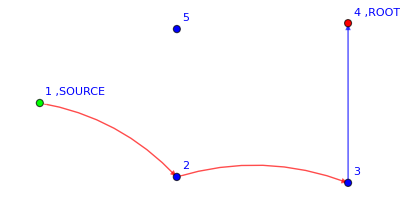

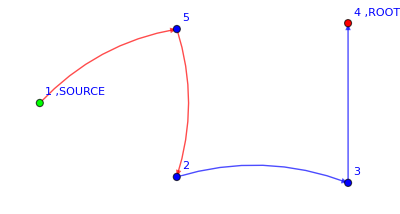

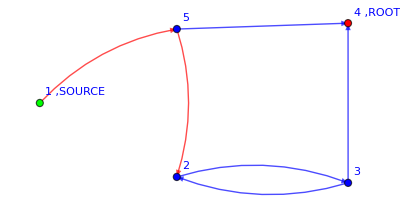

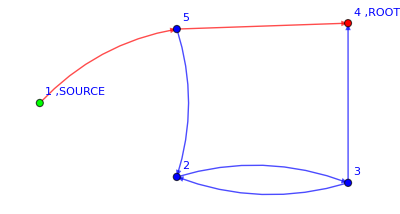

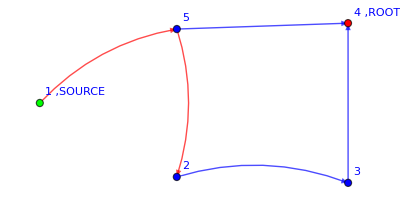

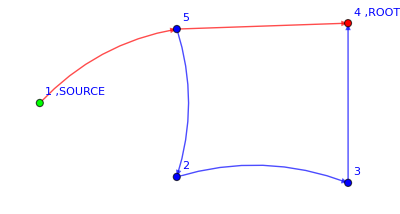

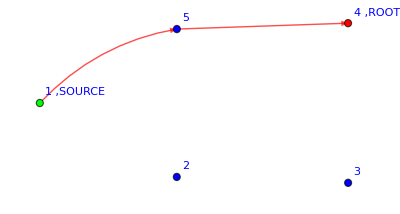

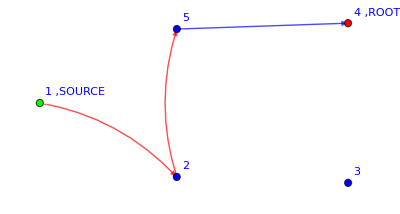

-Graphics-

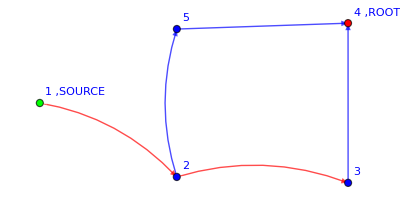

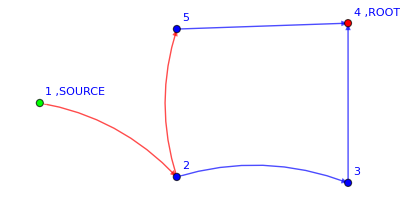

(β[1,2] β[2,3]^2 β[3,4]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4])^2)+(β[1,5] β[2,3]^2 β[3,4]^2 β[5,2]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4])^2 (β[5,1]+β[5,2]+β[5,4])^2)-(2 β[1,5] β[2,3]^2 β[3,2] β[3,4] β[5,2] β[5,4])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4])^2 (β[5,1]+β[5,2]+β[5,4])^2)+(2 β[1,5] β[2,3] β[3,4] β[5,2] β[5,4])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4])^2)+(β[1,5] β[5,4]^2)/((β[1,2]+β[1,5]) (β[5,1]+β[5,2]+β[5,4])^2)+(β[1,2] β[2,5]^2 β[5,4]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[5,1]+β[5,2]+β[5,4])^2)+(β[1,5] β[2,3]^2 β[3,2]^2 β[5,4]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4])^2 (β[5,1]+β[5,2]+β[5,4])^2)-(2 β[1,5] β[2,3] β[3,2] β[5,4]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4])^2)+(2 β[1,2] β[2,3] β[2,5] β[3,4] β[5,4])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4]))

```mathematica
g=myFavoriteGraph;
fields={χ,ϕ,ψ};
endTime=2;
Z=DynamicLERWaction[g,endTime];
Z Op[ϕs[1,Subscript[t, 1],0]];
ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->True]
```

## DynamicDLAaction[]

This action should be:

For fields that do not have a color index, we default to set it to j_-1, because in the WickContraction[] it automated with color indices.
Instead, the source is set with index 1, so that it can contract with an external “probe”.

```mathematica
Clear[DynamicDLAaction];
Options[DynamicDLAaction]={"sourceBC"->1,"excludedVertices"->{}};

DynamicDLAaction[graph_,endTime_,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j];

locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[ If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,(*FALSE*)
V[(1+ Sum[locWeights[[x,y]]R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]ϕs[x,Subscript[t, T+1],Subscript[k, x]]χs[y,Subscript[t, T],1],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]+ ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]) ]],{x,Length[locVertices]}]
V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,endTime}]Product[V[(1+ϕ[x,Subscript[t, endTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, endTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}];

Return[action]

]
```

### Usage example of DynamicDLAaction[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Partition Function

###################  Partition Function  ##################

{{1},{-1/6,{1,2,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]}},{-1/6,{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]}},{-1/6,{1,5,RGBColor[0, 0, 1]},{5,1,RGBColor[0, 0, 1]}},{-1/18,{1,2,RGBColor[0, 0, 1]},{2,5,RGBColor[0, 0, 1]},{5,1,RGBColor[0, 0, 1]}},{1/36,{1,5,RGBColor[0, 0, 1]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{5,1,RGBColor[0, 0, 1]}},{-1/18,{1,5,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]}},{-1/9,{2,5,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]}}}

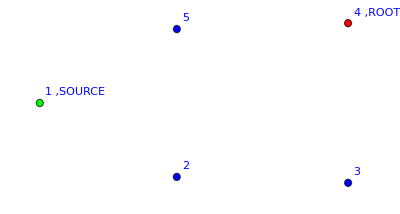

Weight==1

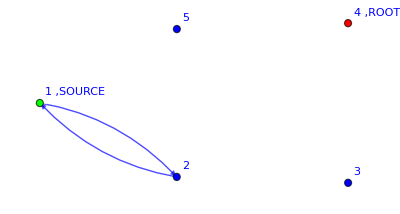

Weight==-1/6

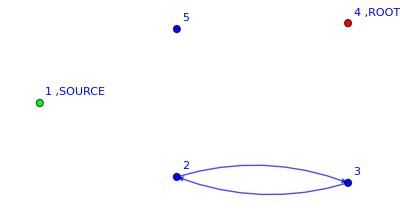

Weight==-1/6

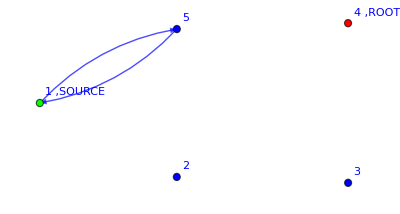

Weight==-1/6

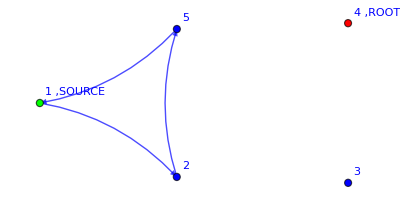

Weight==-1/18

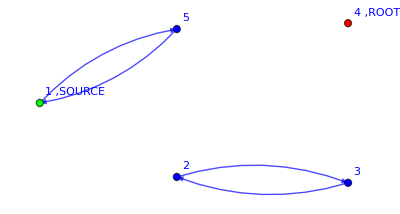

Weight==1/36

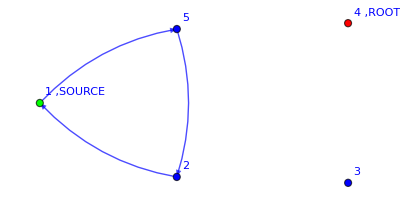

Weight==-1/18

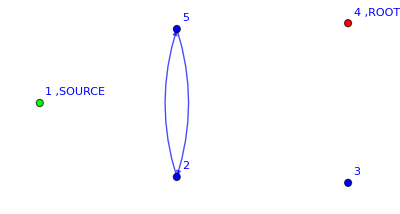

Weight==-1/9

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->True]
```

Observables: Op[ϕs[1,t_1,0]]

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

Here I would like to compare it to the result obtained by solving the laplace eq but I still need the normalization from the FT

```mathematica
sol=LaplaceEqSolver[g];
phi2=Select[sol,#[[1]]==Φ[2] &][[1,2]];
phi5=Select[sol,#[[1]]==Φ[5] &][[1,2]];
phi2/(phi2+phi5)//FullSimplify
phi5/(phi2+phi5)//FullSimplify
```

(β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4)))/((β_(2,1)+2 β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+2 (β_(5,2)+β_(5,4))))

((β_(2,1)+β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,2)+β_(5,4)))/((β_(2,1)+2 β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+2 (β_(5,2)+β_(5,4))))

Observables: Op[χs[1,t_1,1]], i.e. the solution to the Laplace eq

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[g,endTime];
ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Partition Function  ##################

((R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
g=AugmentedGraph[myFavoriteGraph]
Z=DynamicDLAaction[g,endTime];

ExpectationValue[Z  ,"endTime"->endTime,"fields"->fields,"draw"->False]
```

-Graphics-

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))+(β_(1,2) β_(2,1) β_(3,4) β_(4,3))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(3,4) β_(4,3) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,2) β_(2,5) β_(3,4) β_(4,3) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,3) β_(3,4) β_(4,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,1) β_(3,4) β_(4,3) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(3,2) β_(4,3) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,2) β_(2,1) β_(4,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

Φ evaluated at the new source:

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Which is the same as Z. CORRECT!*)
```

Φ evaluated at the old source			 CORRECT!!!!!

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

###################  Operator found  ##################

(β_(4,6))/(β_(4,3)+β_(4,5)+β_(4,6))-(β_(2,3) β_(3,2) β_(4,6))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(4,6) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Let's check that we get the same result by solving the Laplace equation. First, we need to properly normalize it, i.e. divide by Z*)
```

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Phi4FT=ExpectationValue[Z  ,"operator"->χs[4,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Partition Function  ##################

((β_(4,6))/(β_(4,3)+β_(4,5)+β_(4,6))-(β_(2,3) β_(3,2) β_(4,6))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(4,6) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
(*Now from the Laplace eq*)
```

```mathematica
Phi4Laplace=LaplaceEqSolver[g,"selectSolution"->4]
```

(β_(4,6) (β_(2,1) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4)))/(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,6) β_(5,1)+β_(2,5) β_(3,2) β_(4,6) β_(5,1)+β_(2,1) β_(3,4) β_(4,6) β_(5,1)+β_(2,3) β_(3,4) β_(4,6) β_(5,1)+β_(2,5) β_(3,4) β_(4,6) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,6) β_(5,2)+β_(2,1) β_(3,4) β_(4,6) β_(5,2)+β_(2,3) β_(3,4) β_(4,6) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4)+β_(2,1) β_(3,2) β_(4,6) β_(5,4)+β_(2,5) β_(3,2) β_(4,6) β_(5,4)+β_(2,1) β_(3,4) β_(4,6) β_(5,4)+β_(2,3) β_(3,4) β_(4,6) β_(5,4)+β_(2,5) β_(3,4) β_(4,6) β_(5,4))

```mathematica
(*And now, let's subtract them*)
```

```mathematica
Phi4Laplace-Phi4FT//FullSimplify
```

0

```mathematica
(*CORRECT!!!!!!!!*)
```

### Let’s check that kay’s trick for the total current works: IT WORKS ONLY FOR SYMMETRICAL β BUT WITH ANY σ!!!!!!

```mathematica
g=AugmentedGraph[myFavoriteGraph];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Limit[σ(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]
```

###################  Operator found  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,3) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,3) β_(3,2) β_(5,2)+β_(2,5) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,5) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,3) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

```mathematica
Z2=DynamicDLAaction[myFavoriteGraph,endTime,"excludedVertices"->{1}];
ExpectationValue[Z2  Op[χs[2,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]+
ExpectationValue[Z2  Op[χs[5,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]-

ExpectationValue[Z2  Op[χs[2,Subscript[t, 1],1]+χs[5,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Operator found  ##################

###################  Operator found  ##################

0

```mathematica
(*Ok, I can insert the operators directly inside Op[]*)
```

Kay’s trick works only with symmetrical weights!!!!!

```mathematica
(*Now let's verify that kay's trick works*)
```

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Limit[σ*(ExpectationValue[Z  ,"operator"->(χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]

Z2=DynamicDLAaction[myFavoriteGraph,endTime,"excludedVertices"->{1}];
ExpectationValue[Z2,"operator"-> (β[1,2]χs[2,Subscript[t, 1],1]+β[1,5]χs[5,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False]
%%%-%//FullSimplify
%//.β[a_,b_]/;(a<b):>β[b,a]//FullSimplify
```

###################  Operator found  ##################

###################  Partition Function  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

###################  Operator found  ##################

###################  Partition Function  ##################

((β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(5,4))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

(β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)-β_(1,5) β_(2,3) β_(3,4) β_(5,2)-β_(1,5) (β_(2,5) β_(3,2)+(β_(2,3)+β_(2,5)) β_(3,4)) β_(5,4)+β_(2,1) ((β_(3,2) β_(4,3)+(β_(3,2)+β_(3,4)) β_(4,5)) (β_(5,1)+β_(5,2))-(β_(1,5) (β_(3,2)+β_(3,4))-β_(3,2) β_(4,3)) β_(5,4))+β_(1,2) (-β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)-β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))))/(β_(2,5) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,4))+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))+β_(2,1) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

0

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Limit[σ*(ExpectationValue[Z Op[(χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1])],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]

Z2=DynamicDLAaction[myFavoriteGraph,endTime,"excludedVertices"->{1}];
ExpectationValue[Z2 Op[(β[1,2]χs[2,Subscript[t, 1],1]+β[1,5]χs[5,Subscript[t, 1],1])],"endTime"->endTime,"fields"->fields,"draw"->False]
%%%-%//FullSimplify
%//.β[a_,b_]/;(a<b):>β[b,a]//FullSimplify
```

###################  Operator found  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,3) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,3) β_(3,2) β_(5,2)+β_(2,5) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,5) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,3) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

###################  Operator found  ##################

(β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(5,4))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

(β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)-β_(1,5) β_(2,3) β_(3,4) β_(5,2)-β_(1,5) (β_(2,5) β_(3,2)+(β_(2,3)+β_(2,5)) β_(3,4)) β_(5,4)+β_(2,1) ((β_(3,2) β_(4,3)+(β_(3,2)+β_(3,4)) β_(4,5)) (β_(5,1)+β_(5,2))-(β_(1,5) (β_(3,2)+β_(3,4))-β_(3,2) β_(4,3)) β_(5,4))+β_(1,2) (-β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)-β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

0

Does it work for any σ? YESSS

```mathematica
g
```

-Graphics-

Exclude just 1: CORRECT!!!!

```mathematica
AugmGraph=AugmentedGraph[myFavoriteGraph];
g=AugmGraph[[1]];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
exp1=(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ)
exp2=(ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ)
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

###################  Operator found  ##################

σ/(σ+β_(4,3)+β_(4,5))-(σ β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(σ β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp2/.σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])*A_+σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])*B_+σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])->HoldForm[σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])*(A+B+1)]
```

(σ (-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+1))/(σ+β_(4,3)+β_(4,5))

```mathematica
σ (exp1-exp2)
```

σ (1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-σ/(σ+β_(4,3)+β_(4,5))+(σ β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(σ β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
Limit[σ (exp1-exp2), σ -> ∞]-((-(Subscript[β, 3,4] Subscript[β, 4,3])/((Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]))+(Subscript[β, 2,5] Subscript[β, 3,4] Subscript[β, 4,3] Subscript[β, 5,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[β, 2,3] Subscript[β, 3,4] Subscript[β, 4,5] Subscript[β, 5,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[β, 2,5] Subscript[β, 3,2] Subscript[β, 4,3] Subscript[β, 5,4])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[β, 4,5] Subscript[β, 5,4])/((σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[β, 2,3] Subscript[β, 3,2] Subscript[β, 4,5] Subscript[β, 5,4])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4])))(σ+Subscript[β, 4,3]+Subscript[β, 4,5])+exp2(σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5]))^-1(Subscript[β, 4,3]+Subscript[β, 4,5]))//FullSimplify
```

0

```mathematica
(*CORRECT!!! THE LIMIT σ->∞ IS THE SAME AS THE BIG PARENTHESES. CHECK ONENOTE NOTEBOOK FOR DETAILS*)
```

```mathematica
Limit[σ(1-σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])),σ->∞]
```

β_(4,3)+β_(4,5)

```mathematica
Limit[σ((Subscript[β, 3,4] Subscript[β, 4,3])/((Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]))),σ->∞]
```

(β_(3,4) β_(4,3))/(β_(3,2)+β_(3,4))

```mathematica
exp3=ExpectationValue[Z Op[β[1,2]χs[2,Subscript[t, 1],1]+β[1,5]χs[5,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ
```

###################  Operator found  ##################

(σ β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))+(σ β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(σ β_(1,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(σ β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(σ β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
σ(exp1-exp2)-exp3//FullSimplify
%//.β[a_,b_]/;(a<b):>β[b,a]//FullSimplify
```

(σ (β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)-β_(1,5) β_(2,3) β_(3,4) β_(5,2)-β_(1,5) (β_(2,5) β_(3,2)+(β_(2,3)+β_(2,5)) β_(3,4)) β_(5,4)+β_(2,1) ((β_(3,2) β_(4,3)+(β_(3,2)+β_(3,4)) β_(4,5)) (β_(5,1)+β_(5,2))-(β_(1,5) (β_(3,2)+β_(3,4))-β_(3,2) β_(4,3)) β_(5,4))+β_(1,2) (-β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)-β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4)))))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

0

Exclude 1 and 2: CORRECT!!!!

```mathematica
AugmGraph=AugmentedGraph[myFavoriteGraph];
g=AugmGraph[[1]];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1,2}];
exp1=σ(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ)
```

###################  Operator found  ##################

σ (1-σ/(σ+β_(4,3)+β_(4,5))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(β_(4,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
exp2=ExpectationValue[Z Op[β[2,3]χs[3,Subscript[t, 1],1]+(β[1,5]+β[2,5])χs[5,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ
```

###################  Operator found  ##################

(σ β_(2,3) β_(3,4))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))+(σ β_(1,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(σ β_(2,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp1-exp2//FullSimplify
%//.β[a_,b_]/;(a<b):>β[b,a]//FullSimplify
```

-(σ (β_(3,4) (β_(2,3)-β_(4,5))-β_(3,2) (β_(4,3)+β_(4,5))) (β_(5,1)+β_(5,2))+σ (β_(2,3) β_(3,4)+β_(1,5) (β_(3,2)+β_(3,4))+β_(2,5) (β_(3,2)+β_(3,4))-β_(3,2) β_(4,3)) β_(5,4))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

0

### β or β/r? Answer: β!!

We want to check whether we need to use β or β/r in the DLA dynamical action

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
g=AugmentedGraph[myFavoriteGraph];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
DLAnorm=Limit[σ(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]
```

###################  Operator found  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,3) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,3) β_(3,2) β_(5,2)+β_(2,5) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,5) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,3) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

```mathematica
g=myFavoriteGraph;
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];
exp=ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]/DLAnorm/.β[__]->1
ExtractPaths[exp](*This is nicely normalized!!!*)
```

###################  Operator found  ##################

18/11 (1-1/6 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1])+1/6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])-1/9 R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])+1/18 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])+1/3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])+1/9 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1])-1/18 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]))

{{18/11},{-3/11,{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]}},{3/11,{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]}},{-2/11,{2,5,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]}},{1/11,{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]}},{6/11,{1,5,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]}},{2/11,{1,2,RGBColor[1, 0, 0]},{2,5,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]}},{-1/11,{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]}}}

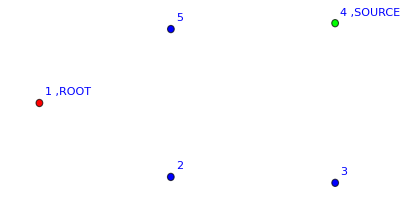

Weight==18/11

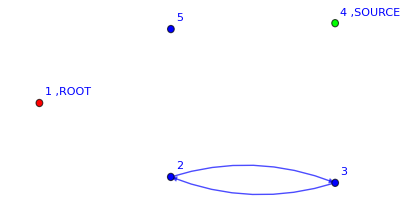

Weight==-3/11

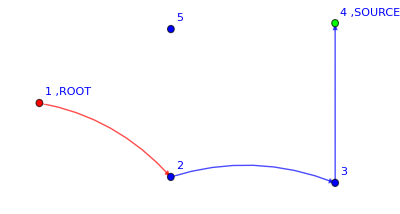

Weight==3/11

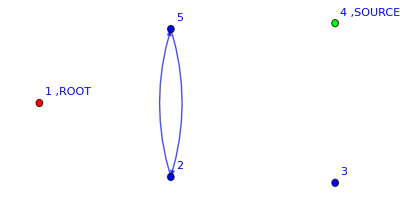

Weight==-2/11

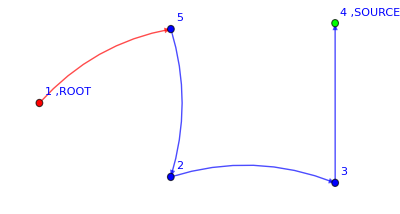

Weight==1/11

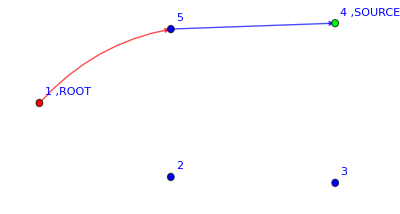

Weight==6/11

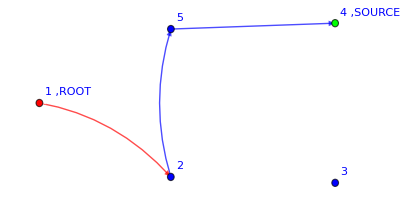

Weight==2/11

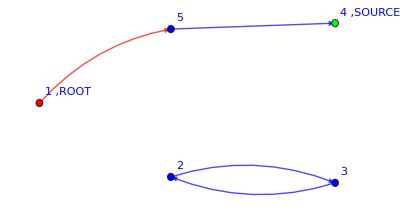

Weight==-1/11

```mathematica
DrawFromExpression[exp];
```

Now, if we use β/r: NOT PROPERLY NORMALIZED

```mathematica
g=AugmentedGraph[myFavoriteGraph];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
DLAnorm=Limit[σ(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]
```

###################  Operator found  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,3) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,3) β_(3,2) β_(5,2)+β_(2,5) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,5) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,3) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

```mathematica
g=myFavoriteGraph;
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];
exp=ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]/DLAnorm/.β[__]->1
ExtractPaths[exp]
```

###################  Operator found  ##################

18/11 (1-1/6 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1])+1/12 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])-1/9 R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])+1/36 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])+1/6 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])+1/18 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1])-1/36 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]))

{{(5 R_(1,2,RGBColor[1, 0, 0]))/22},{(3 R_(1,5,RGBColor[1, 0, 0]))/11}}

```mathematica
(*Not properly normalized!!!*)
```

### Can I send each field to zero immediately or do I need to do it at the end? Answer: YESSS!

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Partition Function right away

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

Partition function field by field

```mathematica
fields={ϕ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
fields={χ};
ExpectationValue[%%,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

V[1+χ_(4,1)] V[1+(β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(β_(1,2) χ_(1,i_1) (χ^*)_(2,i_1))/(β_(1,2)+β_(1,5))+(β_(1,5) χ_(1,i_1) (χ^*)_(5,i_1))/(β_(1,2)+β_(1,5))] V[1+(β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))]

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Ok, for the partition funciton it works. But in the partition function only χ is used*)
```

Observables: Op[ϕs[1,t_1,0]]

Right away

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
```

###################  Operator found  ##################

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

Field by field

```mathematica
fields={ϕ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
fields={χ};
ExpectationValue[%%,"endTime"->endTime,"fields"->fields,"draw"->False"Rrule"->{}]
```

###################  Operator found  ##################

V[1+χ_(4,1)] V[1+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))]+R_(1,2,RGBColor[1, 0, 0]) V[1+χ_(4,1)] V[1+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))] β_(1,2) (χ^*)_(2,1)+R_(1,5,RGBColor[1, 0, 0]) V[1+χ_(4,1)] V[1+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))] β_(1,5) (χ^*)_(5,1)

###################  Partition Function  ##################

###################  Partition Function  ##################

###################  Partition Function  ##################

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*OK!! IT SEEMS THAT I CAN DO FIRST A FIELD, SET TO ZERO, THEN THE OTHERS*)
```

## I would like to compute the denominator of the DLA transition probability. To do this, I try to use nn different fields and then send nn->-1.

```mathematica
fields={χ,ϕ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g=AugmentedGraph[g];

endTime=1;Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}]
```

V[1+ϕ_(1,t_2,0)] V[1+ϕ_(1,t_2,k_1)] V[1+ϕ_(2,t_2,0)] V[1+ϕ_(2,t_2,k_2)] V[1+ϕ_(3,t_2,0)] V[1+ϕ_(3,t_2,k_3)] V[1+ϕ_(4,t_2,0)] V[1+ϕ_(4,t_2,k_4)] V[1+χ_(4,t_1,1)] V[1+ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1)+R_(1,2,RGBColor[1, 0, 0]) β_(1,2) ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (χ^*)_(2,t_1,1)+(R_(1,2,RGBColor[0, 0, 1]) β_(1,2) χ_(1,t_1,i_1) (χ^*)_(2,t_1,i_1))/(β_(1,2)+β_(1,3))+R_(1,3,RGBColor[1, 0, 0]) β_(1,3) ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (χ^*)_(3,t_1,1)+(R_(1,3,RGBColor[0, 0, 1]) β_(1,3) χ_(1,t_1,i_1) (χ^*)_(3,t_1,i_1))/(β_(1,2)+β_(1,3))] V[1+ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2)+R_(2,1,RGBColor[1, 0, 0]) β_(2,1) ϕ_(2,t_1,k_2) (ϕ^*)_(1,t_2,k_2) (ϕ^*)_(2,t_2,k_2) (χ^*)_(1,t_1,1)+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,t_1,i_2) (χ^*)_(1,t_1,i_2))/(β_(2,1)+β_(2,3))+R_(2,3,RGBColor[1, 0, 0]) β_(2,3) ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(3,t_2,k_2) (χ^*)_(3,t_1,1)+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,t_1,i_2) (χ^*)_(3,t_1,i_2))/(β_(2,1)+β_(2,3))] V[1+ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3)+R_(3,1,RGBColor[1, 0, 0]) β_(3,1) ϕ_(3,t_1,k_3) (ϕ^*)_(1,t_2,k_3) (ϕ^*)_(3,t_2,k_3) (χ^*)_(1,t_1,1)+(R_(3,1,RGBColor[0, 0, 1]) β_(3,1) χ_(3,t_1,i_3) (χ^*)_(1,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))+R_(3,2,RGBColor[1, 0, 0]) β_(3,2) ϕ_(3,t_1,k_3) (ϕ^*)_(2,t_2,k_3) (ϕ^*)_(3,t_2,k_3) (χ^*)_(2,t_1,1)+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,t_1,i_3) (χ^*)_(2,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))+R_(3,4,RGBColor[1, 0, 0]) β_(3,4) ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3) (ϕ^*)_(4,t_2,k_3) (χ^*)_(4,t_1,1)+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,t_1,i_3) (χ^*)_(4,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))]

```mathematica
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))-(β_(1,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(1,2) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(1,3) β_(2,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

```mathematica
ExpectationValue[Z Op[(χs[4,Subscript[t, 1],1]-χs[3,Subscript[t, 1],1])]Op[(χs[4,Subscript[t, 1],1]-χs[3,Subscript[t, 1],1])],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

0

```mathematica
fields={χ,ϕ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g=AugmentedGraph[g];

endTime=1;
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];

Z1=ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))-(β_(1,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(1,2) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(1,3) β_(2,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

```mathematica
endTime=3;
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];
Z3=ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1-(β_(1,2)^3 β_(2,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3)+(3 β_(1,2)^2 β_(2,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2)-(3 β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))-(β_(1,3)^3 β_(3,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(β_(1,2)^3 β_(2,3)^3 β_(3,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2)^2 β_(1,3) β_(2,3)^2 β_(3,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2) β_(1,3)^2 β_(2,3) β_(3,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2)^2 β_(1,3) β_(2,1) β_(2,3)^2 β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2)^2 β_(2,3)^3 β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(6 β_(1,2) β_(1,3)^2 β_(2,1) β_(2,3) β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(6 β_(1,2) β_(1,3) β_(2,3)^2 β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3)^3 β_(2,1) β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3)^2 β_(2,3) β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2) β_(1,3)^2 β_(2,1)^2 β_(2,3) β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(6 β_(1,2) β_(1,3) β_(2,1) β_(2,3)^2 β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2) β_(2,3)^3 β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3)^3 β_(2,1)^2 β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(6 β_(1,3)^2 β_(2,1) β_(2,3) β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3) β_(2,3)^2 β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(β_(1,3)^3 β_(2,1)^3 β_(3,2)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3)^2 β_(2,1)^2 β_(2,3) β_(3,2)^3)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3) β_(2,1) β_(2,3)^2 β_(3,2)^3)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(β_(2,3)^3 β_(3,2)^3)/((β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)+(3 β_(1,3)^2 β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,2)^3 β_(2,1) β_(2,3)^2 β_(3,1)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2)^2 β_(1,3) β_(2,1) β_(2,3) β_(3,1)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(3 β_(1,2)^2 β_(2,3)^2 β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,2) β_(1,3)^2 β_(2,1) β_(3,1)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,2) β_(1,3) β_(2,3) β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2)^2 β_(1,3) β_(2,1)^2 β_(2,3) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2)^2 β_(2,1) β_(2,3)^2 β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2) β_(1,3)^2 β_(2,1)^2 β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,2) β_(2,3)^2 β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,3)^2 β_(2,1) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,3) β_(2,3) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,2) β_(1,3)^2 β_(2,1)^3 β_(3,2)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2) β_(1,3) β_(2,1)^2 β_(2,3) β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,2) β_(2,1) β_(2,3)^2 β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(3 β_(1,3)^2 β_(2,1)^2 β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,3) β_(2,1) β_(2,3) β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(3 β_(2,3)^2 β_(3,2)^2)/((β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2)^3 β_(2,1)^2 β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2)^2 β_(1,3) β_(2,1)^2 β_(3,1))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(6 β_(1,2)^2 β_(2,1) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(6 β_(1,2) β_(1,3) β_(2,1) β_(3,1))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2)^2 β_(1,3) β_(2,1)^3 β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2)^2 β_(2,1)^2 β_(2,3) β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4)))+(6 β_(1,2) β_(1,3) β_(2,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(6 β_(1,2) β_(2,1) β_(2,3) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,3) β_(2,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

```mathematica
Z1^3-Z3//FullSimplify
```

0

```mathematica
(*SO, USING nn TIME-SLICES YIELDS Z^nn!!!! THIS IS EXPECTED. DOES IT WORK FOR <χ^*χ>?? *)
```

Does it work for <χ^*χ>?

###################  Operator found  ##################

{{1/12,{1,3,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]}},{1/6,{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]}}}

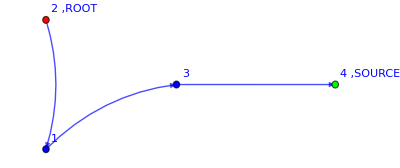

Weight==1/12

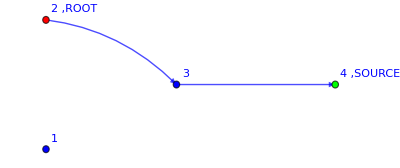

Weight==1/6

(β_(1,3) β_(2,1) β_(3,4))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))+(β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

```mathematica
fields={χ,ϕ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g=AugmentedGraph[g];

endTime=1;
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];

Z1=ExpectationValue[Z Op[χs[2,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->True,"graph"->g]
```

```mathematica
endTime=3;
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];
Z3=ExpectationValue[Z Op[χs[2,Subscript[t, 1],1]] Op[χs[2,Subscript[t, 2],1]] Op[χs[2,Subscript[t, 3],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

(β_(1,3)^3 β_(2,1)^3 β_(3,4)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)+(3 β_(1,3)^2 β_(2,1)^2 β_(2,3) β_(3,4)^3)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)+(3 β_(1,3) β_(2,1) β_(2,3)^2 β_(3,4)^3)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)+(β_(2,3)^3 β_(3,4)^3)/((β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)

```mathematica
Z1^3-Z3//FullSimplify
```

0

```mathematica
(*IT WORKS!!!!!!!!!!!
CAN I USE THIS TO COMPUTE THE DENOMINATOR?????*)
```

Other attempt

```mathematica
Z=V[1+(Subscript[R, 1,2,RGBColor[0, 0, 1]] Subscript[β, 1,2] Subscript[χ, 1,Subscript[t, 1],Subscript[i, 1]] Subscript[SuperStar[χ], 2,Subscript[t, 1],Subscript[i, 1]])/(Subscript[β, 1,2]+Subscript[β, 1,3])+(Subscript[R, 1,3,RGBColor[0, 0, 1]] Subscript[β, 1,3] Subscript[χ, 1,Subscript[t, 1],Subscript[i, 1]] Subscript[SuperStar[χ], 3,Subscript[t, 1],Subscript[i, 1]])/(Subscript[β, 1,2]+Subscript[β, 1,3])] V[1+(Subscript[R, 2,1,RGBColor[0, 0, 1]] Subscript[β, 2,1] Subscript[χ, 2,Subscript[t, 1],Subscript[i, 2]] Subscript[SuperStar[χ], 1,Subscript[t, 1],Subscript[i, 2]])/(Subscript[β, 2,1]+Subscript[β, 2,3])+(Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[β, 2,3] Subscript[χ, 2,Subscript[t, 1],Subscript[i, 2]] Subscript[SuperStar[χ], 3,Subscript[t, 1],Subscript[i, 2]])/(Subscript[β, 2,1]+Subscript[β, 2,3])] V[1+(Subscript[R, 3,1,RGBColor[0, 0, 1]] Subscript[β, 3,1] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3]] Subscript[SuperStar[χ], 1,Subscript[t, 1],Subscript[i, 3]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])+(Subscript[R, 3,2,RGBColor[0, 0, 1]] Subscript[β, 3,2] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3]] Subscript[SuperStar[χ], 2,Subscript[t, 1],Subscript[i, 3]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])+(Subscript[R, 3,4,RGBColor[0, 0, 1]] Subscript[β, 3,4] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3]] Subscript[SuperStar[χ], 4,Subscript[t, 1],Subscript[i, 3]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])];Z=Z/.χ[a_,b_,c_]->(ϕ[a,b,c])/.χs[a_,b_,c_]->ϕs[a,b,c]
```

V[1+(R_(1,2,RGBColor[0, 0, 1]) β_(1,2) ϕ_(1,t_1,i_1) (ϕ^*)_(2,t_1,i_1))/(β_(1,2)+β_(1,3))+(R_(1,3,RGBColor[0, 0, 1]) β_(1,3) ϕ_(1,t_1,i_1) (ϕ^*)_(3,t_1,i_1))/(β_(1,2)+β_(1,3))] V[1+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) ϕ_(2,t_1,i_2) (ϕ^*)_(1,t_1,i_2))/(β_(2,1)+β_(2,3))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) ϕ_(2,t_1,i_2) (ϕ^*)_(3,t_1,i_2))/(β_(2,1)+β_(2,3))] V[1+(R_(3,1,RGBColor[0, 0, 1]) β_(3,1) ϕ_(3,t_1,i_3) (ϕ^*)_(1,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) ϕ_(3,t_1,i_3) (ϕ^*)_(2,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) ϕ_(3,t_1,i_3) (ϕ^*)_(4,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))]

```mathematica
fields={χ,ϕ};
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]-(1-(Subscript[β, 1,2] Subscript[β, 2,1])/((Subscript[β, 1,2]+Subscript[β, 1,3]) (Subscript[β, 2,1]+Subscript[β, 2,3]))-(Subscript[β, 1,3] Subscript[β, 3,1])/((Subscript[β, 1,2]+Subscript[β, 1,3]) (Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[β, 1,2] Subscript[β, 2,3] Subscript[β, 3,1])/((Subscript[β, 1,2]+Subscript[β, 1,3]) (Subscript[β, 2,1]+Subscript[β, 2,3]) (Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[β, 1,3] Subscript[β, 2,1] Subscript[β, 3,2])/((Subscript[β, 1,2]+Subscript[β, 1,3]) (Subscript[β, 2,1]+Subscript[β, 2,3]) (Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[β, 2,3] Subscript[β, 3,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]) (Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])))^2//FullSimplify
```

###################  Partition Function  ##################

(2 β_(1,3)^2 β_(3,2) (-2 β_(2,3) (β_(2,1)+β_(2,3)) β_(3,1)-β_(2,1)^2 β_(3,2))-2 β_(1,2)^2 β_(2,3) (β_(2,3) β_(3,1)^2+2 β_(2,1) β_(3,2) (β_(3,1)+β_(3,2)+β_(3,4)))-4 β_(1,2) β_(1,3) β_(2,3) β_(3,2) (β_(2,3) β_(3,1)+β_(2,1) (3 β_(3,1)+β_(3,2)+β_(3,4))))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)

# Final Dynamical theories (?)

## FinalDynamicLERWaction[]

This action should be:

For fields that do not have a color index, we default to set it to j_-1, because in the WickContraction[] it automated with color indices.
Instead, the source is set with index 1, so that it can contract with an external “probe”

```mathematica
Clear[FinalDynamicLERWaction];
Options[FinalDynamicLERWaction]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

FinalDynamicLERWaction[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[ 
V[(1+γ Sum[If[totWeights[[x]]===0 ,0,(*FALSE*)locWeights[[x,y]]/totWeights[[x]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, x]]ψs[x,Subscript[t, T+1],Subscript[j, -1]]- ϕs[x,Subscript[t, T+1],Subscript[k, x]])ϕ[x,Subscript[t, T],Subscript[k, x]]χs[y,Subscript[t, T],1]] ,{y,Length[locVertices]}]+Sum[If[totWeights[[x]]===0 ,0,(*FALSE*)locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]]],{y,Length[locVertices]}]+ ψs[x,Subscript[t, T+1],Subscript[j, -1]]ψ[x,Subscript[t, T],Subscript[j, -1]]+ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]) ],{x,Length[locVertices]}]
V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,locStartingTime,locEndTime}]Product[V[(1+ψ[x,Subscript[t, locEndTime+1],Subscript[j, -1]])(*This allows the PASSIVE path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],Subscript[k, x]])(*This allows the ACTIVE path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}];

Return[action]

]
```

```mathematica
fields={ϕ,ψ,χ};
startingTime=1;
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicLERWaction["graph"->g,"startingTime"->startingTime,"endTime"->endTime];
ExpectationValue[Z Op[Subscript[SuperStar[ϕ], 2,Subscript[t, 1],0] Subscript[SuperStar[ψ], 1,Subscript[t, 1],Subscript[j, -1]]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
```

###################  Operator found  ##################

1-(γ R_(3,4,RGBColor[0, 0, 1]) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(γ R_(5,4,RGBColor[0, 0, 1]) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
%/.β[__]->1/.R[__,Blue]->1
```

1-(5 γ)/18+1/6 γ R_(2,3,RGBColor[1, 0, 0])+1/9 γ R_(2,5,RGBColor[1, 0, 0])

### Usage example of DynamicLERWaction[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Partition Function

```mathematica
g=myFavoriteGraph;
endTime=1;
Z=FinalDynamicLERWaction["graph"->g,"endTime"->endTime]
```

V[1+ϕ_(1,t_2,0)] V[1+ϕ_(2,t_2,0)] V[1+ϕ_(3,t_2,0)] V[1+ϕ_(4,t_2,0)] V[1+ϕ_(5,t_2,0)] V[1+ψ_(1,t_2,j_-1)] V[1+ψ_(2,t_2,j_-1)] V[1+ψ_(3,t_2,j_-1)] V[1+ψ_(4,t_2,j_-1)] V[1+ψ_(5,t_2,j_-1)] V[1+ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1)+(R_(1,2,RGBColor[0, 0, 1]) β_(1,2) χ_(1,t_1,i_1) (χ^*)_(2,t_1,i_1))/(β_(1,2)+β_(1,5))+(R_(1,5,RGBColor[0, 0, 1]) β_(1,5) χ_(1,t_1,i_1) (χ^*)_(5,t_1,i_1))/(β_(1,2)+β_(1,5))+ψ_(1,t_1,j_-1) (ψ^*)_(1,t_2,j_-1)+γ ((R_(1,2,RGBColor[1, 0, 0]) β_(1,2) ϕ_(1,t_1,k_1) χ_(4,t_1,1) (χ^*)_(2,t_1,1) (-(ϕ^*)_(1,t_2,k_1)+(ϕ^*)_(2,t_2,k_1) (ψ^*)_(1,t_2,j_-1)))/(β_(1,2)+β_(1,5))+(R_(1,5,RGBColor[1, 0, 0]) β_(1,5) ϕ_(1,t_1,k_1) χ_(4,t_1,1) (χ^*)_(5,t_1,1) (-(ϕ^*)_(1,t_2,k_1)+(ϕ^*)_(5,t_2,k_1) (ψ^*)_(1,t_2,j_-1)))/(β_(1,2)+β_(1,5)))] V[1+ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2)+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,t_1,i_2) (χ^*)_(1,t_1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,t_1,i_2) (χ^*)_(3,t_1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,t_1,i_2) (χ^*)_(5,t_1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+ψ_(2,t_1,j_-1) (ψ^*)_(2,t_2,j_-1)+γ ((R_(2,1,RGBColor[1, 0, 0]) β_(2,1) ϕ_(2,t_1,k_2) χ_(4,t_1,1) (χ^*)_(1,t_1,1) (-(ϕ^*)_(2,t_2,k_2)+(ϕ^*)_(1,t_2,k_2) (ψ^*)_(2,t_2,j_-1)))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[1, 0, 0]) β_(2,3) ϕ_(2,t_1,k_2) χ_(4,t_1,1) (χ^*)_(3,t_1,1) (-(ϕ^*)_(2,t_2,k_2)+(ϕ^*)_(3,t_2,k_2) (ψ^*)_(2,t_2,j_-1)))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[1, 0, 0]) β_(2,5) ϕ_(2,t_1,k_2) χ_(4,t_1,1) (χ^*)_(5,t_1,1) (-(ϕ^*)_(2,t_2,k_2)+(ϕ^*)_(5,t_2,k_2) (ψ^*)_(2,t_2,j_-1)))/(β_(2,1)+β_(2,3)+β_(2,5)))] V[1+ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3)+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,t_1,i_3) (χ^*)_(2,t_1,i_3))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,t_1,i_3) (χ^*)_(4,t_1,i_3))/(β_(3,2)+β_(3,4))+ψ_(3,t_1,j_-1) (ψ^*)_(3,t_2,j_-1)+γ ((R_(3,2,RGBColor[1, 0, 0]) β_(3,2) ϕ_(3,t_1,k_3) χ_(4,t_1,1) (χ^*)_(2,t_1,1) (-(ϕ^*)_(3,t_2,k_3)+(ϕ^*)_(2,t_2,k_3) (ψ^*)_(3,t_2,j_-1)))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[1, 0, 0]) β_(3,4) ϕ_(3,t_1,k_3) χ_(4,t_1,1) (χ^*)_(4,t_1,1) (-(ϕ^*)_(3,t_2,k_3)+(ϕ^*)_(4,t_2,k_3) (ψ^*)_(3,t_2,j_-1)))/(β_(3,2)+β_(3,4)))] V[1+ϕ_(5,t_1,k_5) (ϕ^*)_(5,t_2,k_5)+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,t_1,i_5) (χ^*)_(1,t_1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,t_1,i_5) (χ^*)_(2,t_1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,t_1,i_5) (χ^*)_(4,t_1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+ψ_(5,t_1,j_-1) (ψ^*)_(5,t_2,j_-1)+γ ((R_(5,1,RGBColor[1, 0, 0]) β_(5,1) ϕ_(5,t_1,k_5) χ_(4,t_1,1) (χ^*)_(1,t_1,1) (-(ϕ^*)_(5,t_2,k_5)+(ϕ^*)_(1,t_2,k_5) (ψ^*)_(5,t_2,j_-1)))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[1, 0, 0]) β_(5,2) ϕ_(5,t_1,k_5) χ_(4,t_1,1) (χ^*)_(2,t_1,1) (-(ϕ^*)_(5,t_2,k_5)+(ϕ^*)_(2,t_2,k_5) (ψ^*)_(5,t_2,j_-1)))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[1, 0, 0]) β_(5,4) ϕ_(5,t_1,k_5) χ_(4,t_1,1) (χ^*)_(4,t_1,1) (-(ϕ^*)_(5,t_2,k_5)+(ϕ^*)_(4,t_2,k_5) (ψ^*)_(5,t_2,j_-1)))/(β_(5,1)+β_(5,2)+β_(5,4)))]

Observable Op[ϕs[1,t_1,0]]

```mathematica
fields={ϕ,ψ,χ};
startingTime=1;
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicLERWaction["graph"->g,"startingTime"->startingTime,"endTime"->endTime];
exp=ExpectationValue[Z Op[Subscript[SuperStar[ϕ], 1,Subscript[t, 1],0]],"endTime"->endTime+1,"fields"->fields,"draw"->False,"Rrule"->{}]

(*Dexp=D[exp,γ]/.γ->0*)
```

###################  Operator found  ##################

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp*18/13/.β[__]->1/.R[__,Blue]->1/.γ->2 γ//Expand
```

1-(11 γ)/13+5/13 γ R_(1,2,RGBColor[1, 0, 0])+6/13 γ R_(1,5,RGBColor[1, 0, 0])

```mathematica
%/.R[__,Red]->1
```

1

```mathematica
(*Dexp=D[exp,γ]/.γ->0;*)
exp2=exp/.R[a_,b_,Red]->R[a,b,Red]Op[ϕs[b,Subscript[t, 1],0]ψs[a,Subscript[t, 1],Subscript[j, -1]]]
```

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp=ExpectationValue[Z exp2,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
```

###################  Partition Function  ##################

1-(R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))+(R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 β_(2,3)^2 β_(3,2)^2)/((β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)+(γ R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3)^2 β_(3,2) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)-(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,3)^2 β_(3,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)+(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,3)^2 β_(3,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)+(R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(1,2) β_(2,1) β_(2,3) β_(3,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)))-(2 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2)^2 β_(2,1) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1])^2 R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(2,5)^2 β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(1,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,5) β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,3)^2 β_(3,2) β_(3,4) β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(2,5) β_(3,2) β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,3) β_(2,5) β_(3,4) β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,3) β_(3,4) β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])^2 β_(1,5) β_(2,1) β_(2,5) β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(2,5,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1])^2 β_(2,5)^2 β_(5,2)^2)/((β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])^2 β_(1,5)^2 β_(2,1) β_(2,3) β_(3,4) β_(5,2)^2)/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])^2 β_(1,5) β_(2,3) β_(2,5) β_(3,4) β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5)^2 β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1])^2 R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2)^2 β_(2,5)^2 β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,5) β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,5) β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,3)^2 β_(3,2)^2 β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,3) β_(2,5) β_(3,2) β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,3) β_(2,5) β_(3,2) β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(2 γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,3) β_(3,2) β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,1) β_(2,5) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(2,5,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5)^2 β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,1) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,5) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,1) β_(2,3) β_(3,2) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(2,5) β_(3,2) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,5)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,5)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(2 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(2 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3) β_(3,2) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(R_(1,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,1))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(2 R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2)^2 β_(2,3) β_(2,5) β_(3,4) β_(5,1))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,3) β_(3,4) β_(5,1))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(2,1) β_(2,5) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(2 R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,1) β_(2,3) β_(3,2) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(2 R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,3) β_(2,5) β_(3,2) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,1) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,1) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2)^2 β_(2,1) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,1) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(2 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(2 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
comp=exp*18/13/.β[__]->1/.R[__,Blue]->1/.γ->2 γ//Expand
```

11/36-(121 γ)/468+5/13 γ R_(1,2,RGBColor[1, 0, 0])-25/117 γ^2 R_(1,2,RGBColor[1, 0, 0])+5/13 γ R_(1,5,RGBColor[1, 0, 0])-4/13 γ^2 R_(1,5,RGBColor[1, 0, 0])+5/39 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0])+10/117 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0])+2/39 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+10/39 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

```mathematica
comp/.γ^n_->γ
```

11/36-(121 γ)/468+20/117 γ R_(1,2,RGBColor[1, 0, 0])+1/13 γ R_(1,5,RGBColor[1, 0, 0])+5/39 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0])+10/117 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0])+2/39 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+10/39 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

```mathematica
Dexp=D[exp,γ]/.γ->0;
exp2=Dexp/.R[a_,b_,Red]R[b_,c_,Red]->R[a,b,Red]R[b,c,Red]Op[ϕs[c,Subscript[t, 1],0]ψs[b,Subscript[t, 1],Subscript[j, -1]]ψs[a,Subscript[t, 1],Subscript[j, -1]]]
```

(Op[(ϕ^*)_(3,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,3)^2 β_(3,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)+(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(Op[(ϕ^*)_(4,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(4,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(4,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,5)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(4,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(2 Op[(ϕ^*)_(4,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3) β_(3,2) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(3,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp=ExpectationValue[Z exp2,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
```

###################  Partition Function  ##################

(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,3)^2 β_(3,4)^3)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^3)+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,3)^2 β_(3,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,5)^2 β_(5,4)^3)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^3)+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^3 R_(5,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^3 β_(3,4)^3 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^3 (β_(3,2)+β_(3,4))^3 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(2,3,RGBColor[1, 0, 0]) R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^3 β_(3,2) β_(3,4)^2 β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^3 (β_(3,2)+β_(3,4))^3 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,5)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4)^2 β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
Dexp=D[exp,γ]/.γ->0;
exp2=Dexp/.R[a_,b_,Red]R[b_,c_,Red]R[c_,d_,Red]->R[a,b,Red]R[b,c,Red]R[c,d,Red]Op[ϕs[c,Subscript[t, 1],0]ψs[c,Subscript[t, 1],Subscript[j, -1]]ψs[b,Subscript[t, 1],Subscript[j, -1]]ψs[a,Subscript[t, 1],Subscript[j, -1]]]
```

(Op[(ϕ^*)_(3,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(3,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,3)^2 β_(3,4)^3)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^3)+(Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,5)^2 β_(5,4)^3)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^3)+(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^3 R_(5,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^3 β_(3,4)^3 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^3 (β_(3,2)+β_(3,4))^3 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(2,3,RGBColor[1, 0, 0]) R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^3 β_(3,2) β_(3,4)^2 β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^3 (β_(3,2)+β_(3,4))^3 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(3,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(3,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4)^2 β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
ExpectationValue[Z Op[Subscript[SuperStar[ϕ], 2,Subscript[t, 1],0] Subscript[SuperStar[ψ], 1,Subscript[t, 1],Subscript[j, -1]]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
```

###################  Operator found  ##################

1

```mathematica
exp/.R[__,Blue]->1/.β[__]->1
```

169/324+25/648 γ R_(1,2,RGBColor[1, 0, 0])+1/54 γ R_(1,5,RGBColor[1, 0, 0])

```mathematica
%/.γ->1/.R[__]->1
```

125/216

## FinalDynamicDLAaction[]

This action should be:

For fields that do not have a color index, we default to set it to j_-1, because in the WickContraction[] it automated with color indices.
Instead, the source is set with index 1, so that it can contract with an external “probe”.

```mathematica
Clear[FinalDynamicDLAaction];
Options[FinalDynamicDLAaction]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"endTime"->10};

FinalDynamicDLAaction[OptionsPattern[]]:=Module[{locGraph,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];

locGraph=OptionValue["graph"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, x]]-1)ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]χs[y,Subscript[t, T],1],{y,Length[locVertices]}]+
Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]+ ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]) ]
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])]
(*V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])]*);

action=Product[actionTimeSlice[T],{T,locEndTime}](*Product[V[(1+ϕ[x,Subscript[t, locEndTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}]*);

Return[action]

]
```

### Usage example of DynamicDLAaction[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Partition Function

```mathematica
Z=FinalDynamicDLAaction["graph"->g,"endTime"->endTime]
```

V[1+ϕ_(4,t_1,k_4) (ϕ^*)_(4,t_2,k_4)+χ_(4,t_1,1)] V[1+ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3)+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,t_1,i_3) (χ^*)_(2,t_1,i_3))/(β_(3,2)+β_(3,4))+γ (β_(3,2) ϕ_(3,t_1,k_3) (-1+R_(3,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_2,k_3)) (ϕ^*)_(3,t_2,k_3) (χ^*)_(2,t_1,1)+β_(3,4) ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3) (-1+R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(4,t_2,k_3)) (χ^*)_(4,t_1,1))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,t_1,i_3) (χ^*)_(4,t_1,i_3))/(β_(3,2)+β_(3,4))] V[1+ϕ_(5,t_1,k_5) (ϕ^*)_(5,t_2,k_5)+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,t_1,i_5) (χ^*)_(1,t_1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,t_1,i_5) (χ^*)_(2,t_1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+γ (β_(5,1) ϕ_(5,t_1,k_5) (-1+R_(5,1,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_5)) (ϕ^*)_(5,t_2,k_5) (χ^*)_(1,t_1,1)+β_(5,2) ϕ_(5,t_1,k_5) (-1+R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_2,k_5)) (ϕ^*)_(5,t_2,k_5) (χ^*)_(2,t_1,1)+β_(5,4) ϕ_(5,t_1,k_5) (-1+R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(4,t_2,k_5)) (ϕ^*)_(5,t_2,k_5) (χ^*)_(4,t_1,1))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,t_1,i_5) (χ^*)_(4,t_1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1)+(R_(1,2,RGBColor[0, 0, 1]) β_(1,2) χ_(1,t_1,i_1) (χ^*)_(2,t_1,i_1))/(β_(1,2)+β_(1,5))+γ (β_(1,2) ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1) (-1+R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_2,k_1)) (χ^*)_(2,t_1,1)+β_(1,5) ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1) (-1+R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(5,t_2,k_1)) (χ^*)_(5,t_1,1))+(R_(1,5,RGBColor[0, 0, 1]) β_(1,5) χ_(1,t_1,i_1) (χ^*)_(5,t_1,i_1))/(β_(1,2)+β_(1,5))] V[1+ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2)+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,t_1,i_2) (χ^*)_(1,t_1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,t_1,i_2) (χ^*)_(3,t_1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+γ (β_(2,1) ϕ_(2,t_1,k_2) (-1+R_(2,1,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_2)) (ϕ^*)_(2,t_2,k_2) (χ^*)_(1,t_1,1)+β_(2,3) ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2) (-1+R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_2,k_2)) (χ^*)_(3,t_1,1)+β_(2,5) ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2) (-1+R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(5,t_2,k_2)) (χ^*)_(5,t_1,1))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,t_1,i_2) (χ^*)_(5,t_1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))]

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicDLAaction["graph"->g,"endTime"->endTime];
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

Observables: Op[ϕs[1,t_1,0]]

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicDLAaction["graph"->g,"endTime"->endTime];
exp=ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],Subscript[k, 1]]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{},"externalδ"->True]
(*Dexp=D[exp,γ]/.γ->0*)
```

###################  Operator found  ##################

(ϕ^*)_(1,t_2,k_1)-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4) (ϕ^*)_(1,t_2,k_1))/(β_(5,1)+β_(5,2)+β_(5,4))-(γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(β_(5,1)+β_(5,2)+β_(5,4))-(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
comp=exp*18/13/.β[__]->1/.R[__,Blue]->1//Expand
```

(ϕ^*)_(1,t_2,k_1)-11/13 γ (ϕ^*)_(1,t_2,k_1)+5/13 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+6/13 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)

```mathematica
exp2=comp/.SuperStar[ϕ][a_,b_,c_]->Op[SuperStar[ϕ][a,b,c]]/.Subscript[t, a_]->Subscript[t, a-1]
```

Op[(ϕ^*)_(1,t_1,k_1)]-11/13 γ Op[(ϕ^*)_(1,t_1,k_1)]+5/13 γ Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0])+6/13 γ Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,5,RGBColor[1, 0, 0])

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicDLAaction["graph"->g,"endTime"->endTime];
exp=ExpectationValue[Z exp2,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{},"externalδ"->True]
```

###################  Partition Function  ##################

(ϕ^*)_(1,t_2,k_1)-11/13 γ (ϕ^*)_(1,t_2,k_1)-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(11 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2) (ϕ^*)_(1,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(11 γ^2 R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(11 γ R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2) (ϕ^*)_(1,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(11 γ^2 R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) (ϕ^*)_(1,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4) (ϕ^*)_(1,t_2,k_1))/(β_(5,1)+β_(5,2)+β_(5,4))+(11 γ^2 R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4) (ϕ^*)_(1,t_2,k_1))/(13 (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(11 γ^2 R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4) (ϕ^*)_(1,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(11 γ^2 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4) (ϕ^*)_(1,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+5/13 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-(5 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/(13 (β_(3,2)+β_(3,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(11 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(5 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/(13 (β_(5,1)+β_(5,2)+β_(5,4)))-(5 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(2,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/(13 (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(11 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(5 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1))/(13 (β_(3,2)+β_(3,4)))+6/13 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-(6 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(6 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(6 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(2,3) β_(3,4) β_(5,2) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-6/13 γ^2 R_(1,5,RGBColor[1, 0, 0]) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+(6 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(11 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(β_(5,1)+β_(5,2)+β_(5,4))-(11 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(11 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(6 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(6 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(2,3) β_(3,4) β_(5,2) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(5 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(5,1)+β_(5,2)+β_(5,4)))+(5 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(2,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(5,1)+β_(5,2)+β_(5,4)))+6/13 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-(6 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(2,3) β_(3,2) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))

```mathematica
comp2=exp/.β[__]->1/.R[__,Blue]->1//Expand
```

13/18 (ϕ^*)_(1,t_2,k_1)-11/9 γ (ϕ^*)_(1,t_2,k_1)+121/234 γ^2 (ϕ^*)_(1,t_2,k_1)+155/234 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-80/117 γ^2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+5/26 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)+28/39 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-32/39 γ^2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+8/39 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/39 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/13 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/13 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)

```mathematica
exp3=comp2/.SuperStar[ϕ][a_,b_,c_]->Op[SuperStar[ϕ][a,b,c]]/.Subscript[t, a_]->Subscript[t, a-1]
```

13/18 Op[(ϕ^*)_(1,t_1,k_1)]-11/9 γ Op[(ϕ^*)_(1,t_1,k_1)]+121/234 γ^2 Op[(ϕ^*)_(1,t_1,k_1)]+155/234 γ Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0])-80/117 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0])+28/39 γ Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,5,RGBColor[1, 0, 0])-32/39 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,5,RGBColor[1, 0, 0])+8/39 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0])+5/26 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] Op[(ϕ^*)_(3,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0])+5/39 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0])+1/13 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+5/13 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(4,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicDLAaction["graph"->g,"endTime"->endTime];
exp=ExpectationValue[Z exp3,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{},"externalδ"->True];
comp3=exp/.β[__]->1/.R[__,Blue]->1//Expand
```

###################  Partition Function  ##################

169/324 (ϕ^*)_(1,t_2,k_1)-143/108 γ (ϕ^*)_(1,t_2,k_1)+121/108 γ^2 (ϕ^*)_(1,t_2,k_1)-(1331 γ^3 (ϕ^*)_(1,t_2,k_1))/4212+(3635 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/4212-(7565 γ^2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/4212+305/324 γ^3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+245/468 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)-155/234 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)+5/26 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)+589/702 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-677/351 γ^2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+61/54 γ^3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+383/702 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-236/351 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+245/702 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-295/702 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+23/117 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-59/234 γ^3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/6 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/39 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/26 γ^3 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+215/234 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-265/234 γ^3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+7/26 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/39 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+11/78 γ^3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+25/78 γ^3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)

```mathematica
DrawFromExpression[comp2,"graph"->g]
```

{{13/18,(ϕ^*)_(1,t_2,k_1)},{-11/9,γ,(ϕ^*)_(1,t_2,k_1)},{121/234,γ^2,(ϕ^*)_(1,t_2,k_1)},{5/18,γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)},{-55/234,γ^2,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)},{5/13,γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)},{-35/78,γ^2,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)},{5/26,γ^2,{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(3,t_2,k_2)},{1/3,γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)},{-11/39,γ^2,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)},{5/39,γ^2,{1,2,RGBColor[1, 0, 0]},{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(5,t_2,k_1)},{5/39,γ^2,{1,2,RGBColor[1, 0, 0]},{2,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(5,t_2,k_2)},{5/13,γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)},{-7/13,γ^2,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)},{1/13,γ^2,{1,2,RGBColor[1, 0, 0]},{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1),(ϕ^*)_(5,t_2,k_5)},{1/13,γ^2,{1,5,RGBColor[1, 0, 0]},{5,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_5),(ϕ^*)_(5,t_2,k_5)},{5/13,γ^2,{1,5,RGBColor[1, 0, 0]},{5,4,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(4,t_2,k_5),(ϕ^*)_(5,t_2,k_5)}}

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{1->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==13/18

Part::partd: Part specification {γ,(ϕ^*)_(1,t_2,k_1)}⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification {γ,(ϕ^*)_(1,t_2,k_1)}⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification {γ,(ϕ^*)_(1,t_2,k_1)}⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{{γ,(ϕ^*)_(1,t_2,k_1)}⟦1,1⟧->{γ,(ϕ^*)_(1,t_2,k_1)}⟦1,2⟧→{γ,(ϕ^*)_(1,t_2,k_1)}⟦1,3⟧,1->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==-11/9

Part::partw: Part 3 of γ^2 does not exist.

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,(ϕ^*)_(1,t_2,k_1)}⟦1,3⟧,1->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==121/234

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)}⟦1,1⟧->{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)}⟦1,2⟧→{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/18

Part::partw: Part 3 of γ^2 does not exist.

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==-55/234

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)}⟦1,1⟧->{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)}⟦1,2⟧→{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_2,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/13

Part::partw: Part 3 of γ^2 does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_2,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==-35/78

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(3,t_2,k_2)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],2->3→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_2,3->t_2→k_2,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/26

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)}⟦1,1⟧->{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)}⟦1,2⟧→{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],1->t_2→k_1,5->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==1/3

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],1->t_2→k_1,5->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==-11/39

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(5,t_2,k_1)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->5→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_2,5->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/39

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},{2,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(5,t_2,k_2)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],2->5→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_2,5->t_2→k_2,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/39

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)}⟦1,1⟧->{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)}⟦1,2⟧→{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],1->t_2→k_1,5->t_2→k_5,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/13

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],1->t_2→k_1,5->t_2→k_5,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==-7/13

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1),(ϕ^*)_(5,t_2,k_5)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->5→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_1,5->t_2→k_5,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==1/13

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,5,RGBColor[1, 0, 0]},{5,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_5),(ϕ^*)_(5,t_2,k_5)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],5->2→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_5,5->t_2→k_5,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==1/13

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,5,RGBColor[1, 0, 0]},{5,4,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(4,t_2,k_5),(ϕ^*)_(5,t_2,k_5)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],5->4→RGBColor[1, 0, 0],1->t_2→k_1,4->t_2→k_5,5->t_2→k_5,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/13

```mathematica
ExtractPaths[Dexp]/.β[__]->1
```

{{(48 R_(1,5,RGBColor[1, 0, 0]))/121},{(100 R_(1,2,RGBColor[1, 0, 0]))/121}}

```mathematica
exp/.γ->0/.β[__]->1/.R[__]->1
```

676/121

Here I would like to compare it to the result obtained by solving the laplace eq but I still need the normalization from the FT

```mathematica
sol=LaplaceEqSolver[g];
phi2=Select[sol,#[[1]]==Φ[2] &][[1,2]];
phi5=Select[sol,#[[1]]==Φ[5] &][[1,2]];
phi2/(phi2+phi5)//FullSimplify
phi5/(phi2+phi5)//FullSimplify
```

(β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4)))/((β_(2,1)+2 β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+2 (β_(5,2)+β_(5,4))))

((β_(2,1)+β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,2)+β_(5,4)))/((β_(2,1)+2 β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+2 (β_(5,2)+β_(5,4))))

Observables: Op[χs[1,t_1,1]], i.e. the solution to the Laplace eq

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[g,endTime];
ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Partition Function  ##################

((R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
g=AugmentedGraph[myFavoriteGraph]
Z=DynamicDLAaction[g,endTime];

ExpectationValue[Z  ,"endTime"->endTime,"fields"->fields,"draw"->False]
```

-Graphics-

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))+(β_(1,2) β_(2,1) β_(3,4) β_(4,3))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(3,4) β_(4,3) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,2) β_(2,5) β_(3,4) β_(4,3) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,3) β_(3,4) β_(4,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,1) β_(3,4) β_(4,3) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(3,2) β_(4,3) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,2) β_(2,1) β_(4,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

Φ evaluated at the new source:

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Which is the same as Z. CORRECT!*)
```

Φ evaluated at the old source			 CORRECT!!!!!

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

###################  Operator found  ##################

(β_(4,6))/(β_(4,3)+β_(4,5)+β_(4,6))-(β_(2,3) β_(3,2) β_(4,6))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(4,6) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Let's check that we get the same result by solving the Laplace equation. First, we need to properly normalize it, i.e. divide by Z*)
```

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Phi4FT=ExpectationValue[Z  ,"operator"->χs[4,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Partition Function  ##################

((β_(4,6))/(β_(4,3)+β_(4,5)+β_(4,6))-(β_(2,3) β_(3,2) β_(4,6))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(4,6) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
(*Now from the Laplace eq*)
```

```mathematica
Phi4Laplace=LaplaceEqSolver[g,"selectSolution"->4]
```

(β_(4,6) (β_(2,1) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4)))/(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,6) β_(5,1)+β_(2,5) β_(3,2) β_(4,6) β_(5,1)+β_(2,1) β_(3,4) β_(4,6) β_(5,1)+β_(2,3) β_(3,4) β_(4,6) β_(5,1)+β_(2,5) β_(3,4) β_(4,6) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,6) β_(5,2)+β_(2,1) β_(3,4) β_(4,6) β_(5,2)+β_(2,3) β_(3,4) β_(4,6) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4)+β_(2,1) β_(3,2) β_(4,6) β_(5,4)+β_(2,5) β_(3,2) β_(4,6) β_(5,4)+β_(2,1) β_(3,4) β_(4,6) β_(5,4)+β_(2,3) β_(3,4) β_(4,6) β_(5,4)+β_(2,5) β_(3,4) β_(4,6) β_(5,4))

```mathematica
(*And now, let's subtract them*)
```

```mathematica
Phi4Laplace-Phi4FT//FullSimplify
```

0

```mathematica
(*CORRECT!!!!!!!!*)
```

## ConvergenceManual[]

```mathematica
Clear[ConvergenceManual];
Options[ConvergenceManual]={"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->10,"precision"->10^-9,"theory"->"DLA","gammaValue"->0.1};

ConvergenceManual[operator_,OptionsPattern[]]:=Module[{Z,locOperator,locPrecision,locγ,exp,i,temp,token},

i=1;

If[OptionValue["theory"]=="DLA",
Z=FinalDynamicDLAaction["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1.,
Z=FinalDynamicLERWaction["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1.
];

locOperator= operator + token;
locPrecision=OptionValue["precision"];
locγ=OptionValue["gammaValue"];

exp=Replace[locOperator,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->OptionValue["graph"]]),1];

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1},"graph"->OptionValue[ "graph"]];
exp=exp/.ϕs[a_,Subscript[t, b_],c_]->ϕs[a,Subscript[t, b-1],Subscript[k, a]];
exp=exp/.ψs[a_,Subscript[t, b_],c_]->ψs[a,Subscript[t, b-1],Subscript[l, a]];
exp=exp/.γ->locγ;

Print["########## i="<>ToString[i]<>", "<>ToString[(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0/.γ->locγ)]<>" ############"];

exp=exp/.token->0;

For[i=2,i<=OptionValue["steps"] (*&& (Coefficient[exp,  ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0/.γ->locγ)>=locPrecision*),i++,

exp=exp+token;
exp=Replace[exp,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->OptionValue["graph"]]),1];

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1},"graph"->OptionValue[ "graph"]];
exp=exp/.ϕs[a_,Subscript[t, b_],c_]->ϕs[a,Subscript[t, b-1],Subscript[k, a]];
exp=exp/.ψs[a_,Subscript[t, b_],c_]->ψs[a,Subscript[t, b-1],Subscript[l, a]];
exp=exp/.γ->locγ/.token->0;

Print["########## i="<>ToString[i]<>", "<>ToString[(Coefficient[exp,  ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0/.γ->locγ)]<>" ############"];
];

(*If[(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0/.γ->locγ)<=locPrecision, 
exp=exp/.γ->locγ
];*)

Return[exp];
]
```

#### Test ConvergenceManual[]

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
g=myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
g=myFavoriteGraph;
expManual=ConvergenceManual[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->{ϕ,χ},"steps"->2,"precision"->10^-7,"gammaValue"->0.45]
```

########## i=1, 0.619231 ############

########## i=2, 0.383447 ############

0.+0.383447 (ϕ^*)_(1,t_1,k_1)+0.189386 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+0.0389423 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.205456 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+0.0446538 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.0259615 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.0186923 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.0934615 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
g=myFavoriteGraph;
expManual=ConvergenceManual[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->10,"precision"->10^-7,"gammaValue"->0.45]
```

########## i=1, 0.619231 ############

########## i=2, 0.383447 ############

########## i=3, 0.237442 ############

########## i=4, 0.147031 ############

########## i=5, 0.0910464 ############

########## i=6, 0.0563787 ############

########## i=7, 0.0349114 ############

########## i=8, 0.0216182 ############

########## i=9, 0.0133867 ############

########## i=10, 0.00828944 ############

0.+0.00828944 (ϕ^*)_(1,t_1,k_1)+0.00924569 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+0.00536046 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.00599384 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+0.00405485 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)^2+0.0068678 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+0.00642869 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.00437728 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.00205141 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.0041226 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.0032552 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.000867406 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.0119128 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0120058 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00579311 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00621274 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0048974 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00417804 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000719358 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00802127 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00482159 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00319968 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00844244 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4)^2 (ϕ^*)_(5,t_1,k_5)+0.00806169 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4)^2 (ϕ^*)_(5,t_1,k_5)+0.00382409 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4)^2 (ϕ^*)_(5,t_1,k_5)+0.0042376 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4)^2 (ϕ^*)_(5,t_1,k_5)+0.00323816 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)^2 (ϕ^*)_(5,t_1,k_5)+0.00274547 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)^2 (ϕ^*)_(5,t_1,k_5)+0.000492697 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)^2 (ϕ^*)_(5,t_1,k_5)+0.00847724 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)^2 (ϕ^*)_(5,t_1,k_5)+0.00586498 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)^2 (ϕ^*)_(5,t_1,k_5)+0.00261225 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)^2 (ϕ^*)_(5,t_1,k_5)+0.00523907 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)^2 (ϕ^*)_(5,t_1,k_5)+0.00311952 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)^2 (ϕ^*)_(5,t_1,k_5)+0.00211956 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)^2 (ϕ^*)_(5,t_1,k_5)

```mathematica
(*It is repeating the last vertex!!!!*)
```

```mathematica
g=myFavoriteGraph;
expManualNoRepeat=ConvergenceManual[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->4,"precision"->10^-7,"gammaValue"->0.45]
```

########## i=1, 0.619231 ############

########## i=2, 0.383447 ############

########## i=3, 0.237442 ############

########## i=4, 0.147031 ############

0.+0.147031 (ϕ^*)_(1,t_1,k_1)+0.11535 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+0.0482598 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.0410804 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+0.106908 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+0.0574165 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.0354234 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.0219931 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.0232585 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.0173106 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.00594793 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.255962 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0477294 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0282631 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0194662 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00714981 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00525721 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0018926 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00714981 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00525721 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0018926 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
(*Now it should be ok. There was a problem in the way the action was defined*)
```

```mathematica
g=myFavoriteGraph;
expManualNoRepeat=ConvergenceManual[expManualNoRepeat,"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->10,"precision"->10^-7,"gammaValue"->0.45]
```

########## i=1, 0.0910464 ############

########## i=2, 0.0563787 ############

########## i=3, 0.0349114 ############

########## i=4, 0.0216182 ############

########## i=5, 0.0133867 ############

########## i=6, 0.00828944 ############

########## i=7, 0.00513308 ############

########## i=8, 0.00317856 ############

########## i=9, 0.00196826 ############

########## i=10, 0.00121881 ############

0.+0.00121881 (ϕ^*)_(1,t_1,k_1)+0.00142685 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+0.000855537 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.11586 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+0.00101492 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+0.00101937 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.000709992 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.000309382 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.000678529 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.000544947 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.000133582 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.388411 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.137311 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0857295 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0515818 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0532986 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.04047 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0128287 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0532986 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.04047 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0128287 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
g=myFavoriteGraph;
expManualNoRepeat=ConvergenceManual[expManualNoRepeat,"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->10,"precision"->10^-7,"gammaValue"->0.45]
```

########## i=1, 0.000754724 ############

########## i=2, 0.000467348 ############

########## i=3, 0.000289396 ############

########## i=4, 0.000179203 ############

########## i=5, 0.000110968 ############

########## i=6, 0.0000687148 ############

########## i=7, 0.0000425503 ############

########## i=8, 0.0000263485 ############

########## i=9, 0.0000163158 ############

########## i=10, 0.0000101032 ############

0.+0.0000101032 (ϕ^*)_(1,t_1,k_1)+0.000012103 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+7.36711×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.116874 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+8.41933×10^-6 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+8.73519×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6.15992×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+2.57527×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5.9077×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+4.79178×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+1.11592×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.3896 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.138518 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0865728 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.051945 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0541056 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0411199 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0129857 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0541056 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0411199 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0129857 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
g=myFavoriteGraph;
expManualNoRepeat2=ConvergenceManual[expManualNoRepeat,"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->10,"precision"->10^-7,"gammaValue"->0.45]
```

########## i=1,           -6
6.25624 10 ############

########## i=2,           -6
3.87405 10 ############

########## i=3,           -6
2.39893 10 ############

########## i=4,           -6
1.48549 10 ############

########## i=5,           -7
9.19863 10 ############

########## i=6,           -7
5.69608 10 ############

########## i=7,           -7
3.52719 10 ############

########## i=8,           -7
2.18414 10 ############

########## i=9,           -7
1.35249 10 ############

########## i=10,           -8
8.37502 10 ############

0.+8.37502×10^-8 (ϕ^*)_(1,t_1,k_1)+1.00488×10^-7 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+6.12301×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.116883 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+6.97918×10^-8 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+7.25713×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5.12232×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+2.13481×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+4.91329×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+3.9882×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+9.25084×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.138528 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.08658 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.051948 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0541125 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0541125 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
g=myFavoriteGraph;
Convergence[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->6,"precision"->10^-7]
```

########## i= 1 ############

########## i= 2 ############

########## i= 3 ############

########## i= 4 ############

########## i= 5 ############

########## i= 6 ############

0.+0.963889 (ϕ^*)_(1,t_1,k_1)+0.0159394 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1)+0.000198935 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1)+2.67268×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)+1.35363×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2+0.0191273 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.000212673 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.00013292 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.0000797523 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.31228×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.77841×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+5.33862×10^-7 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.000400552 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.75349×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.7863×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.96719×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.42776×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.02314×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+4.04627×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.17245×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.02405×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.14841×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.24733×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.89904×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+9.03941×10^-9 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+9.95098×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+8.21204×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+6.84336×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.36867×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.89382×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.36883×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+5.2499×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.07261×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+6.84491×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+3.88122×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)

```mathematica
%/.f_[__]->1
```

1

```mathematica
exp=%%
```

0.+0.963889 (ϕ^*)_(1,t_1,k_1)+0.0159394 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1)+0.000198935 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1)+2.67268×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)+1.35363×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2+0.0191273 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.000212673 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.00013292 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.0000797523 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.31228×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.77841×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+5.33862×10^-7 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.000400552 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.75349×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.7863×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.96719×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.42776×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.02314×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+4.04627×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.17245×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.02405×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.14841×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.24733×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.89904×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+9.03941×10^-9 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+9.95098×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+8.21204×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+6.84336×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.36867×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.89382×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.36883×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+5.2499×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.07261×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+6.84491×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+3.88122×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)

```mathematica
g=myFavoriteGraph;
Convergence[exp,"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->6,"precision"->10^-7]
```

$Aborted

```mathematica
fields={ϕ,ξ,χ};
endTime=1;
g=myFavoriteGraph;
Z=Final2DynamicDLAaction["graph"->g,"endTime"->endTime]/.β[__]->1;
exp2=ExpectationValue[Z exp,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{},"externalδ"->True]
```

0.+0.963889 (ϕ^*)_(1,t_2,k_1)-0.160648 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-0.0535494 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-0.321296 γ R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-0.107099 γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+0.0535494 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+0.0159394 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-0.0079697 γ R_(1,2,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+0.160648 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-0.0106263 γ R_(1,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+0.107099 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+0.000198935 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)-0.000198935 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)+0.0079697 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)-0.000132623 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)+2.67268×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)+0.000196262 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)-1.78179×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)+2.67268×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2+0.0191273 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.0191273 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00318788 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.00637576 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0535494 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.321296 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.0535494 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000212673 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.000212673 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00013292 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.00013292 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.000106336 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00318788 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.0000664602 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000797523 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.0000797523 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.0000398761 γ R_(1,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00318788 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00531313 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00531313 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.31228×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-4.62455×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.77841×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-3.55683×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000106336 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000664602 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5.33862×10^-7 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1.06772×10^-6 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000398761 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000663115 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000663115 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000400552 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0187267 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.00312112 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.000133517 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+3.75349×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000208919 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.7863×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000131134 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1.87674×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000667587 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-8.93149×10^-7 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.96719×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000777851 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-9.83594×10^-7 γ R_(1,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000667587 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.42776×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.26372×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.02314×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.73795×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+4.04627×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5.2577×10^-7 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+8.90894×10^-7 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+8.90894×10^-7 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+3.17245×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.24883×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.02405×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.73793×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.87674×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+8.93149×10^-7 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.14841×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5.10894×10^-7 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+9.83594×10^-7 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000400552 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)-0.0000667587 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+3.75349×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+1.7863×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+1.96719×10^-6 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+2.42776×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+2.02314×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+4.04627×10^-9 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+5.60022×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+4.04718×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+1.55303×10^-8 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+3.17245×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+2.02405×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+1.14841×10^-8 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)

```mathematica
exp2=exp2/.R[__,Blue]->1/.γ->0.01//Expand;
exp2=exp2/.Subscript[t, a_]->Subscript[t, a-1];
```

```mathematica
g=myFavoriteGraph;
exp3=Convergence[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->4,"precision"->10^-7]
```

########## i=1, 0.938889 ϕs[1, t , k ]
       1   1 ############

########## i=2, 0.938889 ϕs[1, t , k ]
       1   1 ############

########## i=3, 0.881512 ϕs[1, t , k ]
       1   1 ############

########## i=4, 0.827642 ϕs[1, t , k ]
       1   1 ############

0.+0.777064 (ϕ^*)_(1,t_1,k_1)+0.0841153 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+0.00653348 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.000507716 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+0.100938 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+0.0070556 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.00440975 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.00264585 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.000417181 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.00032073 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.0000964506 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.0147593 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000544033 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000340021 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000204012 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000012037 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+9.25926×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+2.77778×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000012037 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+9.25926×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+2.77778×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
g=myFavoriteGraph;
exp4=Convergence[exp3,"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->4,"precision"->10^-7]
```

########## i=1, 0.729577 ϕs[1, t , k ]
       1   1 ############

########## i=2, 0.729577 ϕs[1, t , k ]
       1   1 ############

########## i=3, 0.684992 ϕs[1, t , k ]
       1   1 ############

########## i=4, 0.643131 ϕs[1, t , k ]
       1   1 ############

0.+0.603828 (ϕ^*)_(1,t_1,k_1)+0.116575 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+0.0188751 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.00500425 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+0.13989 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+0.0208513 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.0130321 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.00781924 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.00331512 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.00254322 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.000771901 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.054431 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00545235 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00340772 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00204463 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000539571 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000414363 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000125208 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000539571 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000414363 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000125208 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
g=myFavoriteGraph;
exp5=Convergence[exp4,"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->5,"precision"->10^-7]
```

########## i=1, 0.566928 ϕs[1, t , k ]
       1   1 ############

########## i=2, 0.566928 ϕs[1, t , k ]
       1   1 ############

########## i=3, 0.532282 ϕs[1, t , k ]
       1   1 ############

########## i=4, 0.499754 ϕs[1, t , k ]
       1   1 ############

########## i=5, 0.469213 ϕs[1, t , k ]
       1   1 ############

0.+0.440539 (ϕ^*)_(1,t_1,k_1)+0.120594 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+0.0292581 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.0168268 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+0.144712 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+0.0331331 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.0207082 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.0124249 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.00847479 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.00648531 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.00198948 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.114606 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0186599 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0116625 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00699748 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00323206 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00247743 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000754631 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00323206 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00247743 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000754631 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
g=myFavoriteGraph;
exp6=Convergence[exp5,"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->20,"precision"->10^-5]
```

########## i=1, 0.413617 ############

########## i=2, 0.388341 ############

########## i=3, 0.364609 ############

########## i=4, 0.342327 ############

########## i=5, 0.321407 ############

########## i=6, 0.301766 ############

########## i=7, 0.283324 ############

$Aborted

## Convergence[]

```mathematica
Clear[Convergence];
Options[Convergence]={"graph"->g,"fields"->FieldsNamesGenerator[{ϕ,ξ,χ}],"steps"->10,"precision"->10^-9,"theory"->"DLA","gammaValue"->0.1};

Convergence[operator_,OptionsPattern[]]:=Module[{Z,locOperator,locPrecision,locγ,exp,i=1,temp},

If[OptionValue["theory"]=="DLA",
Z=Final2DynamicDLAaction["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1.,
Z=Final2DynamicLERWaction["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1.
];

locOperator= operator;
locPrecision=OptionValue["precision"];
locγ=OptionValue["gammaValue"];


exp=ExpectationValueBlock[Z locOperator,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"]];
exp=exp/.ϕs[a_,Subscript[t, b_],c_]->ϕs[a,Subscript[t, b-1],Subscript[k, a]];
exp=exp/.ψs[a_,Subscript[t, b_],c_]->ψs[a,Subscript[t, b-1],Subscript[l, a]];
exp=exp/.γ->locγ;

Print["########## i="<>ToString[i]<>", ",(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)," ############"];

For[i=2,i<=OptionValue["steps"] && (Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)>=locPrecision,i++,

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"]];
exp=exp/.ϕs[a_,Subscript[t, b_],c_]->ϕs[a,Subscript[t, b-1],Subscript[k, a]];
exp=exp/.ψs[a_,Subscript[t, b_],c_]->ψs[a,Subscript[t, b-1],Subscript[l, a]];
exp=exp/.γ->locγ;

Print["########## i="<>ToString[i]<>", ",(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)," ############"];
];

(*
If[(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0/.γ->locγ)<=locPrecision, 
exp=exp/.γ->locγ
];*)

Return[exp];
]
```

#### Test Convergence[]

```mathematica
g=myFavoriteGraph;
Convergence[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->3,"precision"->10^-7]
```

########## i= 1 ############

########## i= 2 ############

########## i= 3 ############

0.+0.981778 (ϕ^*)_(1,t_1,k_1)+0.00818587 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1)+0.0000411883 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1)+1.38889×10^-7 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)+0.00982304 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.0000439588 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.0000274743 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.0000164846 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.2037×10^-7 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+9.25926×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.77778×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.0000825154 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.94444×10^-7 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+9.25926×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.01852×10^-7 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.31481×10^-7 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)

{{2.18384},{0.00818587,{1,2,RGBColor[1, 0, 0]}},{0.00982304,{1,5,RGBColor[1, 0, 0]}},{0.0000439588,{1,2,RGBColor[1, 0, 0]},{1,5,RGBColor[1, 0, 0]}},{0.0000411883,{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[1, 0, 0]}},{1.2037×10^-7,{1,2,RGBColor[1, 0, 0]},{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[1, 0, 0]}},{0.0000274743,{1,2,RGBColor[1, 0, 0]},{2,5,RGBColor[1, 0, 0]}},{9.25926×10^-8,{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[1, 0, 0]},{2,5,RGBColor[1, 0, 0]}},{1.38889×10^-7,{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[1, 0, 0]},{3,4,RGBColor[1, 0, 0]}},{0.0000164846,{1,5,RGBColor[1, 0, 0]},{5,2,RGBColor[1, 0, 0]}},{2.77778×10^-8,{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[1, 0, 0]},{5,2,RGBColor[1, 0, 0]}},{0.0000827469,{1,5,RGBColor[1, 0, 0]},{5,4,RGBColor[1, 0, 0]}},{1.94444×10^-7,{1,2,RGBColor[1, 0, 0]},{1,5,RGBColor[1, 0, 0]},{5,4,RGBColor[1, 0, 0]}},{9.25926×10^-8,{1,2,RGBColor[1, 0, 0]},{2,5,RGBColor[1, 0, 0]},{5,4,RGBColor[1, 0, 0]}},{1.01852×10^-7,{1,5,RGBColor[1, 0, 0]},{5,2,RGBColor[1, 0, 0]},{5,4,RGBColor[1, 0, 0]}}}

-Graphics-

Weight==2.18384

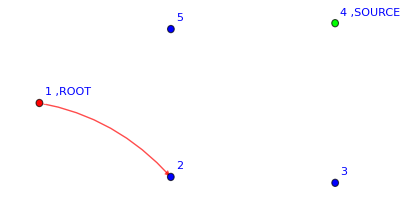

Weight==0.00818587

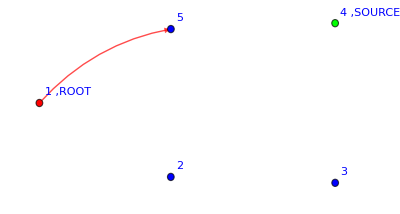

Weight==0.00982304

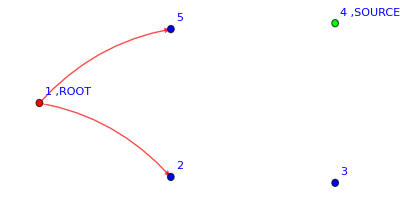

Weight==0.0000439588

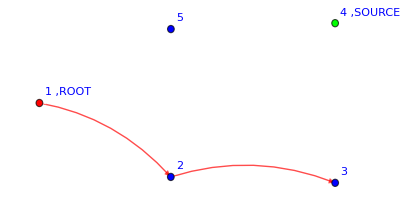

Weight==0.0000411883

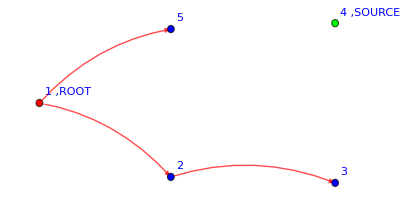

Weight==1.2037×10^-7

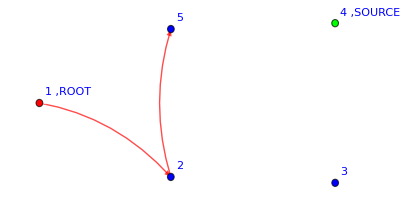

Weight==0.0000274743

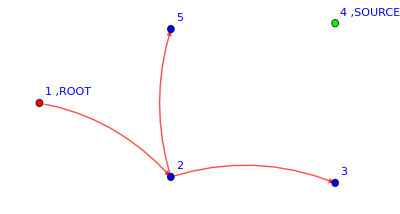

Weight==9.25926×10^-8

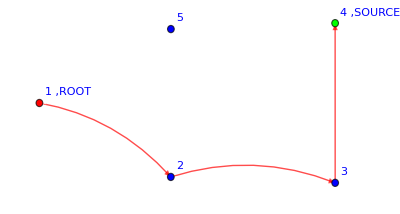

Weight==1.38889×10^-7

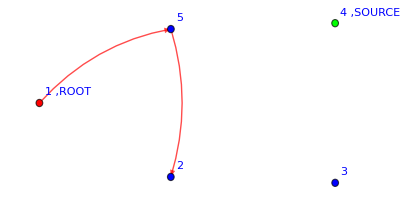

Weight==0.0000164846

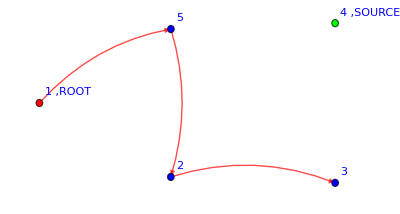

Weight==2.77778×10^-8

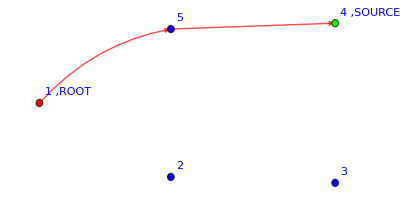

Weight==0.0000827469

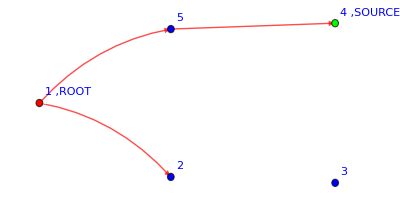

Weight==1.94444×10^-7

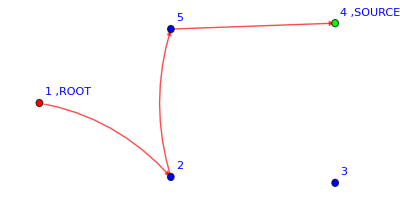

Weight==9.25926×10^-8

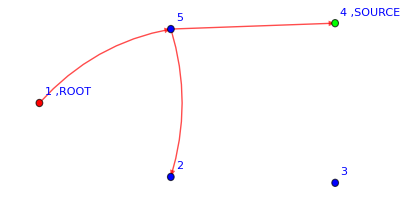

Weight==1.01852×10^-7

```mathematica
exp=0.+0.9817784754801098 Subscript[SuperStar[ϕ], 1,Subscript[t, 1],Subscript[k, 1]]+0.008185865054869686 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[SuperStar[ϕ], 1,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 2,Subscript[t, 1],Subscript[k, 1]]+0.000041188271604938274 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[SuperStar[ϕ], 1,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 2,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 3,Subscript[t, 1],Subscript[k, 1]]+1.388888888888889*^-7 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]] Subscript[SuperStar[ϕ], 1,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 2,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 3,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 4,Subscript[t, 1],Subscript[k, 1]]+0.009823038065843621 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[SuperStar[ϕ], 1,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 5,Subscript[t, 1],Subscript[k, 1]]+0.00004395884773662551 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[SuperStar[ϕ], 1,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 2,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 5,Subscript[t, 1],Subscript[k, 1]]+0.000027474279835390945 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[SuperStar[ϕ], 1,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 2,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 5,Subscript[t, 1],Subscript[k, 1]]+0.000016484567901234566 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[SuperStar[ϕ], 1,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 2,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 5,Subscript[t, 1],Subscript[k, 1]]+1.2037037037037037*^-7 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[SuperStar[ϕ], 1,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 2,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 3,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 5,Subscript[t, 1],Subscript[k, 1]]+9.259259259259259*^-8 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[SuperStar[ϕ], 1,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 2,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 3,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 5,Subscript[t, 1],Subscript[k, 1]]+2.7777777777777774*^-8 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[SuperStar[ϕ], 1,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 2,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 3,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 5,Subscript[t, 1],Subscript[k, 1]]+0.00008251543209876544 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]] Subscript[SuperStar[ϕ], 1,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 4,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 5,Subscript[t, 1],Subscript[k, 1]]+1.9444444444444442*^-7 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]] Subscript[SuperStar[ϕ], 1,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 2,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 4,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 5,Subscript[t, 1],Subscript[k, 1]]+9.259259259259259*^-8 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]] Subscript[SuperStar[ϕ], 1,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 2,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 4,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 5,Subscript[t, 1],Subscript[k, 1]]+1.0185185185185184*^-7 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]] Subscript[SuperStar[ϕ], 1,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 2,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 4,Subscript[t, 1],Subscript[k, 1]] Subscript[SuperStar[ϕ], 5,Subscript[t, 1],Subscript[k, 1]]+2.3148148148148148*^-7 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]^2 Subscript[SuperStar[ϕ], 1,Subscript[t, 1],Subscript[k, 1]] Subscript[(SuperStar[ϕ]), 4,Subscript[t, 1],Subscript[k, 1]]^2 Subscript[SuperStar[ϕ], 5,Subscript[t, 1],Subscript[k, 1]];
exp/.ϕs[__]->1/.Subscript[(SuperStar[ϕ]), __]^2->1;
DrawFromExpression[%,"graph"->g]
```

```mathematica
g=myFavoriteGraph;
Convergence[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->6,"precision"->10^-7]
```

########## i= 1 ############

########## i= 2 ############

########## i= 3 ############

########## i= 4 ############

########## i= 5 ############

########## i= 6 ############

0.+0.963889 (ϕ^*)_(1,t_1,k_1)+0.0159394 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1)+0.000198935 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1)+2.67268×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)+1.35363×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2+0.0191273 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.000212673 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.00013292 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.0000797523 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.31228×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.77841×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+5.33862×10^-7 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.000400552 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.75349×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.7863×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.96719×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.42776×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.02314×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+4.04627×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.17245×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.02405×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.14841×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.24733×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.89904×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+9.03941×10^-9 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+9.95098×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+8.21204×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+6.84336×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.36867×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.89382×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.36883×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+5.2499×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.07261×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+6.84491×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+3.88122×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)

```mathematica
%/.f_[__]->1
```

1

```mathematica
exp=%%
```

0.+0.963889 (ϕ^*)_(1,t_1,k_1)+0.0159394 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1)+0.000198935 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1)+2.67268×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)+1.35363×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2+0.0191273 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.000212673 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.00013292 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.0000797523 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.31228×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.77841×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+5.33862×10^-7 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.000400552 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.75349×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.7863×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.96719×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.42776×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.02314×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+4.04627×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.17245×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.02405×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.14841×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.24733×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.89904×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+9.03941×10^-9 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+9.95098×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+8.21204×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+6.84336×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.36867×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.89382×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.36883×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+5.2499×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.07261×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+6.84491×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+3.88122×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)

```mathematica
g=myFavoriteGraph;
Convergence[exp,"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->6,"precision"->10^-7]
```

$Aborted

```mathematica
fields={ϕ,ξ,χ};
endTime=1;
g=myFavoriteGraph;
Z=Final2DynamicDLAaction["graph"->g,"endTime"->endTime]/.β[__]->1;
exp2=ExpectationValue[Z exp,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{},"externalδ"->True]
```

0.+0.963889 (ϕ^*)_(1,t_2,k_1)-0.160648 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-0.0535494 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-0.321296 γ R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-0.107099 γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+0.0535494 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+0.0159394 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-0.0079697 γ R_(1,2,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+0.160648 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-0.0106263 γ R_(1,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+0.107099 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+0.000198935 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)-0.000198935 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)+0.0079697 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)-0.000132623 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)+2.67268×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)+0.000196262 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)-1.78179×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)+2.67268×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2+0.0191273 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.0191273 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00318788 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.00637576 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0535494 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.321296 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.0535494 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000212673 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.000212673 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00013292 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.00013292 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.000106336 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00318788 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.0000664602 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000797523 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.0000797523 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.0000398761 γ R_(1,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00318788 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00531313 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00531313 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.31228×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-4.62455×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.77841×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-3.55683×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000106336 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000664602 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5.33862×10^-7 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1.06772×10^-6 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000398761 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000663115 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000663115 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000400552 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0187267 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.00312112 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.000133517 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+3.75349×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000208919 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.7863×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000131134 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1.87674×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000667587 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-8.93149×10^-7 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.96719×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000777851 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-9.83594×10^-7 γ R_(1,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000667587 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.42776×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.26372×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.02314×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.73795×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+4.04627×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5.2577×10^-7 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+8.90894×10^-7 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+8.90894×10^-7 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+3.17245×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.24883×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.02405×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.73793×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.87674×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+8.93149×10^-7 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.14841×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5.10894×10^-7 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+9.83594×10^-7 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000400552 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)-0.0000667587 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+3.75349×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+1.7863×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+1.96719×10^-6 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+2.42776×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+2.02314×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+4.04627×10^-9 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+5.60022×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+4.04718×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+1.55303×10^-8 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+3.17245×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+2.02405×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+1.14841×10^-8 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)

```mathematica
exp2=exp2/.R[__,Blue]->1/.γ->0.01//Expand;
exp2=exp2/.Subscript[t, a_]->Subscript[t, a-1];
```

```mathematica
exp2
```

0.+0.957999 (ϕ^*)_(1,t_1,k_1)+0.0184309 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1)+0.000275316 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1)+4.61748×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)+2.67268×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2+0.0221171 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.000294493 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.000184058 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.000110435 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.99251×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.07056×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+9.21946×10^-7 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.000555273 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+6.4915×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.08871×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.40279×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+5.58238×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+4.65198×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+9.30397×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+7.29803×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+4.65513×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.64289×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.33793×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+3.75349×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.7863×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.96719×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+2.42776×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+2.02314×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+4.04627×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+5.60022×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+4.04718×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.55303×10^-10 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+3.17245×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+2.02405×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.14841×10^-10 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)

```mathematica
g=myFavoriteGraph;
exp=Convergence[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->100,"precision"->10^-7,"gammaValue"->0.45]
```

########## i=1, 0.725 ############

########## i=2, 0.525625 ############

########## i=3, 0.381078 ############

########## i=4, 0.276282 ############

########## i=5, 0.200304 ############

########## i=6, 0.145221 ############

########## i=7, 0.105285 ############

########## i=8, 0.0763315 ############

########## i=9, 0.0553404 ############

########## i=10, 0.0401218 ############

########## i=11, 0.0290883 ############

########## i=12, 0.021089 ############

########## i=13, 0.0152895 ############

########## i=14, 0.0110849 ############

########## i=15, 0.00803656 ############

########## i=16, 0.0058265 ############

########## i=17, 0.00422422 ############

########## i=18, 0.00306256 ############

########## i=19, 0.00222035 ############

########## i=20, 0.00160976 ############

########## i=21, 0.00116707 ############

########## i=22, 0.000846128 ############

########## i=23, 0.000613443 ############

########## i=24, 0.000444746 ############

########## i=25, 0.000322441 ############

########## i=26, 0.00023377 ############

########## i=27, 0.000169483 ############

########## i=28, 0.000122875 ############

########## i=29, 0.0000890845 ############

########## i=30, 0.0000645863 ############

########## i=31, 0.000046825 ############

########## i=32, 0.0000339482 ############

########## i=33, 0.0000246124 ############

########## i=34, 0.000017844 ############

########## i=35, 0.0000129369 ############

########## i=36,           -6
9.37925 10 ############

########## i=37,           -6
6.79996 10 ############

########## i=38,           -6
4.92997 10 ############

########## i=39,           -6
3.57423 10 ############

########## i=40,           -6
2.59131 10 ############

########## i=41,          -6
1.8787 10 ############

########## i=42,           -6
1.36206 10 ############

########## i=43,           -7
9.87493 10 ############

########## i=44,           -7
7.15931 10 ############

########## i=45,          -7
5.1905 10 ############

########## i=46,           -7
3.76313 10 ############

########## i=47,          -7
2.7283 10 ############

########## i=48,           -7
1.97801 10 ############

########## i=49,           -7
1.43407 10 ############\

########## i=50,           -7
1.03973 10 ############

########## i=51,           -8
7.53664 10 ############

0.+7.5368×10^-8 (ϕ^*)_(1,t_1,k_1)+1.04308×10^-7 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+0.0000305176 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.116974 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)-5.96046×10^-8 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+0.0000133514 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-3.8147×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-5.72205×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-0.00146484 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)-0.00146484 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)-0.00146484 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.13854 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0865717 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0519519 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0551758 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0393066 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0127563 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0551758 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0393066 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0127563 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expNot=exp/.R[a_,4,b_]->0
```

0.+7.5368×10^-8 (ϕ^*)_(1,t_1,k_1)+1.04308×10^-7 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+0.0000305176 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)-5.96046×10^-8 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+0.0000133514 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-3.8147×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-5.72205×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-0.00146484 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)-0.00146484 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)-0.00146484 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)

```mathematica
exp-expNot
```

0.+0.116974 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.13854 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0865717 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0519519 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0551758 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0393066 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0127563 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0551758 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0393066 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0127563 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expTo4=%
```

0.+0.116974 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.13854 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0865717 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0519519 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0551758 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0393066 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0127563 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0551758 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0393066 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0127563 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expTo4/.R[__]->1/.SuperStar[ϕ][__]->1
```

0.998126

```mathematica
expTo4=expTo4/.SuperStar[ϕ][__]->1
```

0.+0.116974 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0551758 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0393066 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0127563 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.13854 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0551758 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0865717 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0393066 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0519519 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0127563 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

```mathematica
g=myFavoriteGraph;
exp2=Convergence[exp,"graph"->g,"steps"->100,"precision"->10^-9,"gammaValue"->0.45]
```

########## i=1,           -8
5.46418 10 ############

########## i=2,           -8
3.96153 10 ############

########## i=3,           -8
2.87211 10 ############

########## i=4,           -8
2.08228 10 ############

########## i=5,           -8
1.50965 10 ############

########## i=6,          -8
1.0945 10 ############

########## i=7,           -9
7.93511 10 ############

########## i=8,           -9
5.75296 10 ############

########## i=9,           -9
4.17089 10 ############

########## i=10,          -9
3.0239 10 ############

########## i=11,           -9
2.19233 10 ############

########## i=12,           -9
1.58944 10 ############

########## i=13,           -9
1.15234 10 ############

########## i=14,           -10
8.35447 10 ############

0.+8.35447×10^-10 (ϕ^*)_(1,t_1,k_1)+4.19707×10^-10 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+1.99966×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.116992 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+4.98148×10^-10 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+2.5301×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+1.58058×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+9.15949×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+1.40831×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+1.05406×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+3.20655×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.138549 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0865692 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0519481 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0544486 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0385766 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.012023 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0544486 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0385766 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.012023 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expNot2=exp2/.R[a_,4,b_]->0;
exp2-expNot2;
expTo42=%/.SuperStar[ϕ][__]->1
```

0.+0.116992 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0544486 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0385766 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.012023 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.138549 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0544486 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0865692 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0385766 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0519481 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.012023 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

```mathematica
expTo42=0.11699222280578406 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]]+0.05444864824186113 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]]+0.03857664709051378 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]]+0.012022971612571043 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]]+0.3896103511412428 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+0.1385491931250009 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+0.05444864824186113 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+0.0865691764248339 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+0.03857664709051378 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+0.05194806861280553 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+0.012022971612571043 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]
```

0.116992 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0544486 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0385766 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.012023 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.138549 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0544486 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0865692 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0385766 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0519481 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.012023 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

```mathematica
expTo42/.R[__]->1/.SuperStar[ϕ][__]->1
```

0.993766

GRAND TOTAL CHECK

```mathematica
expTo42-(30./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]);
%-(20./231 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+32./231 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+12./231 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]);
%-(19./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+19./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]]+25./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+25./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]]+1./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+1./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]]);
%-(9./77 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]])
%/.R[__]->1
```

0.000109106 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.000336094 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-0.00254889 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-0.000964041 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])-3.84691×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0000210546 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.000336094 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-0.0000109102 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-0.00254889 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+1.66648×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-0.000964041 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

-0.00623445

Other check with faster (?) program

```mathematica
FieldsNamesGenerator[{ϕ,ξ,χ}]
```

{{ϕ,ξ,χ},{ϕ^*,ξ^*,χ^*},{δϕ,δξ,δχ},{δϕs,δξs,δχs}}

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]];
g=myFavoriteGraph;
```

```mathematica
exp3=Convergence[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->
FieldsNamesGenerator[{ϕ,ξ,χ}],"steps"->100,"precision"->10^-7,"gammaValue"->0.3]
```

########## i=1, 0.816667 ############

########## i=2, 0.666944 ############

########## i=3, 0.544671 ############

########## i=4, 0.444815 ############

########## i=5, 0.363265 ############

########## i=6, 0.296667 ############

########## i=7, 0.242278 ############

########## i=8, 0.19786 ############

########## i=9, 0.161586 ############

########## i=10, 0.131962 ############

########## i=11, 0.107769 ############

########## i=12, 0.0880112 ############

########## i=13, 0.0718758 ############

########## i=14, 0.0586986 ############

########## i=15, 0.0479372 ############

########## i=16, 0.0391487 ############

########## i=17, 0.0319714 ############

########## i=18, 0.02611 ############

########## i=19, 0.0213232 ############

########## i=20, 0.0174139 ############

########## i=21, 0.0142214 ############

########## i=22, 0.0116141 ############

########## i=23, 0.00948486 ############

########## i=24, 0.00774597 ############

########## i=25, 0.00632588 ############

########## i=26, 0.00516613 ############

########## i=27, 0.00421901 ############

########## i=28, 0.00344552 ############

########## i=29, 0.00281384 ############

########## i=30, 0.00229797 ############

########## i=31, 0.00187668 ############

########## i=32, 0.00153262 ############

########## i=33, 0.00125164 ############

########## i=34, 0.00102217 ############

########## i=35, 0.000834774 ############

########## i=36, 0.000681732 ############

########## i=37, 0.000556748 ############

########## i=38, 0.000454678 ############

########## i=39, 0.00037132 ############

########## i=40, 0.000303245 ############

########## i=41, 0.00024765 ############

########## i=42, 0.000202247 ############

########## i=43, 0.000165169 ############

########## i=44, 0.000134888 ############

########## i=45, 0.000110158 ############

########## i=46, 0.0000899626 ############

########## i=47, 0.0000734695 ############

########## i=48, 0.0000600001 ############

########## i=49, 0.0000490001 ############

########## i=50, 0.0000400167 ############

########## i=51, 0.0000326803 ############

########## i=52, 0.0000266889 ############

########## i=53, 0.000021796 ############

########## i=54, 0.0000178 ############

########## i=55, 0.0000145367 ############

########## i=56, 0.0000118716 ############

########## i=57, 9.69517×10^-6 ############

########## i=58, 7.91772×10^-6 ############

########## i=59, 6.46614×10^-6 ############

########## i=60, 5.28068×10^-6 ############

########## i=61, 4.31255×10^-6 ############

########## i=62, 3.52192×10^-6 ############

########## i=63, 2.87623×10^-6 ############

########## i=64, 2.34892×10^-6 ############

########## i=65, 1.91829×10^-6 ############

########## i=66, 1.5666×10^-6 ############

########## i=67, 1.27939×10^-6 ############

########## i=68, 1.04484×10^-6 ############

########## i=69, 8.53283×10^-7 ############

########## i=70, 6.96848×10^-7 ############

########## i=71, 5.69093×10^-7 ############

########## i=72, 4.64759×10^-7 ############

########## i=73, 3.79553×10^-7 ############

########## i=74, 3.09968×10^-7 ############

########## i=75, 2.53141×10^-7 ############

########## i=76, 2.06732×10^-7 ############

########## i=77, 1.68831×10^-7 ############

########## i=78, 1.37879×10^-7 ############

########## i=79, 1.12601×10^-7 ############

########## i=80, 9.19573×10^-8 ############

0.+9.19573×10^-8 (ϕ^*)_(1,t_1,k_1)+4.59787×10^-8 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+2.17794×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.116883 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+5.51744×10^-8 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+2.75872×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+1.7242×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+1.03452×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+1.51584×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+1.14342×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+3.72427×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.138528 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0865801 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.051948 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0541125 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0541125 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expTo43=exp3/.a_/;Abs[a]<10^-7:>0/.SuperStar[ϕ][__]->1
```

0.116883 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0541125 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.138528 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0541125 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0865801 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.051948 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

```mathematica
expTo43/.R[__]->1
```

1.

GRAND TOTAL CHECK

```mathematica
expTo43-(30./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]);
%-(20./231 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+32./231 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+12./231 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]);
%-(19./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+19./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]]+25./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+25./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]]+1./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+1./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]]);
%-(9./77 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]])
%/.a_/;Abs[a]<10^-7:>0
%/.R[__]->1
```

-3.5639×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-2.48047×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-1.87105×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-6.09426×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])-7.52378×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-4.51427×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-2.48047×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-2.82142×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-1.87105×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-1.69285×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-6.09426×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

0

0

Other attempts

```mathematica
g=myFavoriteGraph;
exp4=Convergence[exp3,"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->4,"precision"->10^-7]
```

########## i=1, 0.729577 ϕs[1, t , k ]
       1   1 ############

########## i=2, 0.729577 ϕs[1, t , k ]
       1   1 ############

########## i=3, 0.684992 ϕs[1, t , k ]
       1   1 ############

########## i=4, 0.643131 ϕs[1, t , k ]
       1   1 ############

0.+0.603828 (ϕ^*)_(1,t_1,k_1)+0.116575 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+0.0188751 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.00500425 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+0.13989 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+0.0208513 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.0130321 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.00781924 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.00331512 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.00254322 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.000771901 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.054431 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00545235 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00340772 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00204463 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000539571 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000414363 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000125208 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000539571 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000414363 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000125208 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
g=myFavoriteGraph;
exp5=Convergence[exp4,"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->5,"precision"->10^-7]
```

########## i=1, 0.566928 ϕs[1, t , k ]
       1   1 ############

########## i=2, 0.566928 ϕs[1, t , k ]
       1   1 ############

########## i=3, 0.532282 ϕs[1, t , k ]
       1   1 ############

########## i=4, 0.499754 ϕs[1, t , k ]
       1   1 ############

########## i=5, 0.469213 ϕs[1, t , k ]
       1   1 ############

0.+0.440539 (ϕ^*)_(1,t_1,k_1)+0.120594 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+0.0292581 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.0168268 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+0.144712 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+0.0331331 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.0207082 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.0124249 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.00847479 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.00648531 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.00198948 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.114606 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0186599 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0116625 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00699748 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00323206 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00247743 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000754631 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00323206 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00247743 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000754631 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
g=myFavoriteGraph;
exp6=Convergence[exp5,"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->20,"precision"->10^-5]
```

########## i=1, 0.413617 ############

########## i=2, 0.388341 ############

########## i=3, 0.364609 ############

########## i=4, 0.342327 ############

########## i=5, 0.321407 ############

########## i=6, 0.301766 ############

########## i=7, 0.283324 ############

$Aborted

## Final2DynamicDLAaction[]

This action should be:

For fields that do not have a color index, we default to set it to j_-1, because in the WickContraction[] it automated with color indices.
Instead, the source is set with index 1, so that it can contract with an external “probe”.

```mathematica
Clear[Final2DynamicDLAaction];
Options[Final2DynamicDLAaction]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"endTime"->10};

Final2DynamicDLAaction[OptionsPattern[]]:=Module[{locGraph,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];

locGraph=OptionValue["graph"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[ 
V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, x]]-1)ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]χs[y,Subscript[t, T],1]OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1]Product[If[z!=x,ξs[z,Subscript[t, T],Subscript[j, z]],1],{z,Length[locVertices]}],{y,Length[locVertices]}]+ξ[x,Subscript[t, T],Subscript[j, x]](1+Sum[If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],0,(*FALSE*)locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]]],{y,Length[locVertices]}])+ (1+If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],0,ξ[x,Subscript[t, T],Subscript[j, x]]])ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]) ],{x,Length[locVertices]}]
(*V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])]*);

action=Product[actionTimeSlice[T],{T,locEndTime}](*Product[V[(1+ϕ[x,Subscript[t, locEndTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}]*);

Return[action]

]
```

### Usage example of Final2DynamicDLAaction[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
g=myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Partition Function

```mathematica
fields={ϕ,η,χ};
endTime=1;
g=myFavoriteGraph;
Z=Final2DynamicDLAaction["graph"->g,"endTime"->endTime];
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1

Observables: ϕs[1,t_1,k_1]

```mathematica
fields={ϕ,ξ,χ};
endTime=1;
Z=Final2DynamicDLAaction["graph"->g,"endTime"->1]/.β[__]->1;
expDLA=ExpectationValue[Z ϕs[1,Subscript[t, 1],Subscript[k, 1]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1}]/.γ->"γ_1"
```

(ϕ^*)_(1,t_2,k_1)-11/18 γ_1 (ϕ^*)_(1,t_2,k_1)+5/18 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+1/3 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)

```mathematica
expDLA/.ϕs[a_,Subscript[t, b_],c_]->ϕs[a,Subscript[t, b-1],Subscript[k, a]];
expDLA2=ExpectationValue[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1}]/.γ->"γ_2"
```

(ϕ^*)_(1,t_2,k_1)-11/18 γ_1 (ϕ^*)_(1,t_2,k_1)-11/18 γ_2 (ϕ^*)_(1,t_2,k_1)+121/324 γ_1 γ_2 (ϕ^*)_(1,t_2,k_1)+5/18 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-55/324 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+5/18 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2)-35/108 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2)+5/36 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(3,t_2,k_2)+1/3 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-11/54 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/54 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(5,t_2,k_1)+5/54 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(5,t_2,k_2)+1/3 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_5)-7/18 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_5)+1/18 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_5)+1/18 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_5) (ϕ^*)_(5,t_2,k_5)+5/18 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_5) (ϕ^*)_(5,t_2,k_5)

Again

```mathematica
fields={ϕ,ξ,χ};
endTime=1;
g=myFavoriteGraph;
Z=Final2DynamicDLAaction["graph"->g,"endTime"->endTime]/.β[__]->1;
exp=ExpectationValue[Z ϕs[1,Subscript[t, 1],Subscript[k, 1]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{},"externalδ"->True]
```

###################  Partition Function  ##################

(ϕ^*)_(1,t_2,k_1)-1/6 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-1/18 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-1/3 γ R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-1/9 γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+1/18 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+1/6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+1/9 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+1/18 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/3 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1/18 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)

```mathematica
comp=exp/.β[__]->1/.R[__,Blue]->1//Expand
```

(ϕ^*)_(1,t_2,k_1)-11/18 γ (ϕ^*)_(1,t_2,k_1)+5/18 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+1/3 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)

```mathematica
exp2=comp/.Subscript[t, a_]->Subscript[t, a-1]
```

(ϕ^*)_(1,t_1,k_1)-11/18 γ (ϕ^*)_(1,t_1,k_1)+5/18 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1)+1/3 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_1)

```mathematica
fields={ϕ,ξ,χ};
endTime=1;
g=myFavoriteGraph;
Z=Final2DynamicDLAaction["graph"->g,"endTime"->endTime]/.β[__]->1;
exp=ExpectationValue[Z exp2,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{},"externalδ"->True]
```

###################  Partition Function  ##################

(ϕ^*)_(1,t_2,k_1)-11/18 γ (ϕ^*)_(1,t_2,k_1)-1/6 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+11/108 γ^2 R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-1/18 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+11/324 γ^2 R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-1/3 γ R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+11/54 γ^2 R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-1/9 γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+11/162 γ^2 R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+1/18 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-11/324 γ^2 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+5/18 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-5/36 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+1/6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-11/108 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-5/27 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+1/9 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-11/162 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+5/36 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)+1/3 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1/3 γ^2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/18 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1/9 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/18 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-11/324 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/3 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-11/54 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1/18 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+11/324 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/18 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/18 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/54 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/54 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/3 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1/18 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)

```mathematica
fields={ϕ,ξ,χ};
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicDLAaction["graph"->g,"endTime"->endTime]/.β[__]->1;
ExpectationValue[Z exp2,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{},"externalδ"->True]
```

###################  Partition Function  ##################

(ϕ^*)_(1,t_2,k_1)-11/18 γ (ϕ^*)_(1,t_2,k_1)-1/6 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+11/108 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-1/6 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+11/108 γ^2 R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-1/9 R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+11/162 γ R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-1/18 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+11/324 γ^2 R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-1/3 γ R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+11/54 γ^2 R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-1/9 γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+11/162 γ^2 R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+1/18 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-11/324 γ^2 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+5/18 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-5/36 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+1/6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-11/108 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-5/27 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+1/9 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-11/162 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+5/36 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)+1/3 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1/3 γ^2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1/18 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/18 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1/9 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/18 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-11/324 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/3 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-11/54 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1/18 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+11/324 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/18 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/18 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/54 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/54 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/3 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1/18 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)

```mathematica
exp2-%
```

(ϕ^*)_(1,t_1,k_1)-11/18 γ (ϕ^*)_(1,t_1,k_1)-(ϕ^*)_(1,t_2,k_1)+11/18 γ (ϕ^*)_(1,t_2,k_1)+1/6 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-11/108 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+1/6 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-11/108 γ^2 R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+1/9 R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-11/162 γ R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+1/18 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-11/324 γ^2 R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+1/3 γ R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-11/54 γ^2 R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+1/9 γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-11/162 γ^2 R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-1/18 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+11/324 γ^2 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+5/18 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1)-5/18 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+5/36 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-1/6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+11/108 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+5/27 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-1/9 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+11/162 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-5/36 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)+1/3 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_1)-1/3 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/3 γ^2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/18 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1/18 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/9 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1/18 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+11/324 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1/3 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+11/54 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/18 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-11/324 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1/18 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1/18 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-5/54 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-5/54 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1/3 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/18 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)

```mathematica
%//FullSimplify
```

1/324 (18 (ϕ^*)_(1,t_1,k_1) (18-11 γ+5 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_1,k_1)+6 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(5,t_1,k_1))-(ϕ^*)_(1,t_2,k_1) (324-198 γ+2 (-18+11 γ) R_(2,5,RGBColor[0, 0, 1]) (R_(5,2,RGBColor[0, 0, 1])+γ R_(5,4,RGBColor[0, 0, 1]) (1-R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_2,k_1)))+R_(2,3,RGBColor[0, 0, 1]) (-((-18+11 γ) (R_(3,2,RGBColor[0, 0, 1]) (-3+γ R_(5,4,RGBColor[0, 0, 1]))-γ R_(3,4,RGBColor[0, 0, 1]) (3+R_(5,2,RGBColor[0, 0, 1])-3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_2,k_1))))+γ R_(1,5,RGBColor[1, 0, 0]) (R_(3,4,RGBColor[0, 0, 1]) ((18-11 γ) R_(5,2,RGBColor[0, 0, 1])+18 γ (-2+(R_(1,2,RGBColor[1, 0, 0])+R_(5,2,RGBColor[1, 0, 0])) (ϕ^*)_(2,t_2,k_1)))+R_(3,2,RGBColor[0, 0, 1]) ((-18+11 γ) R_(5,4,RGBColor[0, 0, 1])-18 (1-γ+γ R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(4,t_2,k_1)))) (ϕ^*)_(5,t_2,k_1))+3 γ (15 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_2,k_1) (2+γ R_(3,4,RGBColor[0, 0, 1]) (-1+R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_2,k_1)))+36 R_(1,5,RGBColor[1, 0, 0]) (1-γ+γ R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(4,t_2,k_1)) (ϕ^*)_(5,t_2,k_1)+2 R_(5,4,RGBColor[0, 0, 1]) (-((-18+11 γ) (-1+R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(5,t_2,k_1)))+5 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_2,k_1) (-2+(R_(1,5,RGBColor[1, 0, 0])+R_(2,5,RGBColor[1, 0, 0])) (ϕ^*)_(5,t_2,k_1))))))

```mathematica
comp2=exp/.β[__]->1/.R[__,Blue]->1//Expand
```

(ϕ^*)_(1,t_2,k_1)-11/9 γ (ϕ^*)_(1,t_2,k_1)+121/324 γ^2 (ϕ^*)_(1,t_2,k_1)+5/9 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-55/324 γ^2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+2/3 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-11/54 γ^2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)

```mathematica
comp2=exp/.β[__]->1/.R[__,Blue]->1//Expand
```

13/18 (ϕ^*)_(1,t_2,k_1)-11/9 γ (ϕ^*)_(1,t_2,k_1)+121/234 γ^2 (ϕ^*)_(1,t_2,k_1)+155/234 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-80/117 γ^2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+5/26 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)+28/39 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-32/39 γ^2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+8/39 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/39 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/13 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/13 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)

```mathematica
exp3=comp2/.SuperStar[ϕ][a_,b_,c_]->Op[SuperStar[ϕ][a,b,c]]/.Subscript[t, a_]->Subscript[t, a-1]
```

13/18 Op[(ϕ^*)_(1,t_1,k_1)]-11/9 γ Op[(ϕ^*)_(1,t_1,k_1)]+121/234 γ^2 Op[(ϕ^*)_(1,t_1,k_1)]+155/234 γ Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0])-80/117 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0])+28/39 γ Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,5,RGBColor[1, 0, 0])-32/39 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,5,RGBColor[1, 0, 0])+8/39 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0])+5/26 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] Op[(ϕ^*)_(3,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0])+5/39 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0])+1/13 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+5/13 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(4,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicDLAaction["graph"->g,"endTime"->endTime];
exp=ExpectationValue[Z exp3,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{},"externalδ"->True];
comp3=exp/.β[__]->1/.R[__,Blue]->1//Expand
```

###################  Partition Function  ##################

169/324 (ϕ^*)_(1,t_2,k_1)-143/108 γ (ϕ^*)_(1,t_2,k_1)+121/108 γ^2 (ϕ^*)_(1,t_2,k_1)-(1331 γ^3 (ϕ^*)_(1,t_2,k_1))/4212+(3635 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/4212-(7565 γ^2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/4212+305/324 γ^3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+245/468 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)-155/234 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)+5/26 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)+589/702 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-677/351 γ^2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+61/54 γ^3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+383/702 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-236/351 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+245/702 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-295/702 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+23/117 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-59/234 γ^3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/6 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/39 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/26 γ^3 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+215/234 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-265/234 γ^3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+7/26 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/39 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+11/78 γ^3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+25/78 γ^3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)

```mathematica
DrawFromExpression[comp2,"graph"->g]
```

{{13/18,(ϕ^*)_(1,t_2,k_1)},{-11/9,γ,(ϕ^*)_(1,t_2,k_1)},{121/234,γ^2,(ϕ^*)_(1,t_2,k_1)},{5/18,γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)},{-55/234,γ^2,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)},{5/13,γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)},{-35/78,γ^2,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)},{5/26,γ^2,{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(3,t_2,k_2)},{1/3,γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)},{-11/39,γ^2,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)},{5/39,γ^2,{1,2,RGBColor[1, 0, 0]},{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(5,t_2,k_1)},{5/39,γ^2,{1,2,RGBColor[1, 0, 0]},{2,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(5,t_2,k_2)},{5/13,γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)},{-7/13,γ^2,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)},{1/13,γ^2,{1,2,RGBColor[1, 0, 0]},{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1),(ϕ^*)_(5,t_2,k_5)},{1/13,γ^2,{1,5,RGBColor[1, 0, 0]},{5,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_5),(ϕ^*)_(5,t_2,k_5)},{5/13,γ^2,{1,5,RGBColor[1, 0, 0]},{5,4,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(4,t_2,k_5),(ϕ^*)_(5,t_2,k_5)}}

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{1->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==13/18

Part::partd: Part specification {γ,(ϕ^*)_(1,t_2,k_1)}⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification {γ,(ϕ^*)_(1,t_2,k_1)}⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification {γ,(ϕ^*)_(1,t_2,k_1)}⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{{γ,(ϕ^*)_(1,t_2,k_1)}⟦1,1⟧->{γ,(ϕ^*)_(1,t_2,k_1)}⟦1,2⟧→{γ,(ϕ^*)_(1,t_2,k_1)}⟦1,3⟧,1->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==-11/9

Part::partw: Part 3 of γ^2 does not exist.

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,(ϕ^*)_(1,t_2,k_1)}⟦1,3⟧,1->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==121/234

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)}⟦1,1⟧->{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)}⟦1,2⟧→{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/18

Part::partw: Part 3 of γ^2 does not exist.

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==-55/234

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)}⟦1,1⟧->{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)}⟦1,2⟧→{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_2,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/13

Part::partw: Part 3 of γ^2 does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_2,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==-35/78

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(3,t_2,k_2)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],2->3→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_2,3->t_2→k_2,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/26

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)}⟦1,1⟧->{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)}⟦1,2⟧→{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],1->t_2→k_1,5->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==1/3

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],1->t_2→k_1,5->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==-11/39

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(5,t_2,k_1)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->5→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_2,5->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/39

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},{2,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(5,t_2,k_2)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],2->5→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_2,5->t_2→k_2,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/39

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)}⟦1,1⟧->{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)}⟦1,2⟧→{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],1->t_2→k_1,5->t_2→k_5,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/13

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],1->t_2→k_1,5->t_2→k_5,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==-7/13

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1),(ϕ^*)_(5,t_2,k_5)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->5→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_1,5->t_2→k_5,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==1/13

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,5,RGBColor[1, 0, 0]},{5,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_5),(ϕ^*)_(5,t_2,k_5)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],5->2→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_5,5->t_2→k_5,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==1/13

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,5,RGBColor[1, 0, 0]},{5,4,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(4,t_2,k_5),(ϕ^*)_(5,t_2,k_5)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],5->4→RGBColor[1, 0, 0],1->t_2→k_1,4->t_2→k_5,5->t_2→k_5,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/13

```mathematica
ExtractPaths[Dexp]/.β[__]->1
```

{{(48 R_(1,5,RGBColor[1, 0, 0]))/121},{(100 R_(1,2,RGBColor[1, 0, 0]))/121}}

```mathematica
exp/.γ->0/.β[__]->1/.R[__]->1
```

676/121

Here I would like to compare it to the result obtained by solving the laplace eq but I still need the normalization from the FT

```mathematica
sol=LaplaceEqSolver[g];
phi2=Select[sol,#[[1]]==Φ[2] &][[1,2]];
phi5=Select[sol,#[[1]]==Φ[5] &][[1,2]];
phi2/(phi2+phi5)//FullSimplify
phi5/(phi2+phi5)//FullSimplify
```

(β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4)))/((β_(2,1)+2 β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+2 (β_(5,2)+β_(5,4))))

((β_(2,1)+β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,2)+β_(5,4)))/((β_(2,1)+2 β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+2 (β_(5,2)+β_(5,4))))

Observables: Op[χs[1,t_1,1]], i.e. the solution to the Laplace eq

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[g,endTime];
ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Partition Function  ##################

((R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
g=AugmentedGraph[myFavoriteGraph]
Z=DynamicDLAaction[g,endTime];

ExpectationValue[Z  ,"endTime"->endTime,"fields"->fields,"draw"->False]
```

-Graphics-

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))+(β_(1,2) β_(2,1) β_(3,4) β_(4,3))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(3,4) β_(4,3) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,2) β_(2,5) β_(3,4) β_(4,3) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,3) β_(3,4) β_(4,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,1) β_(3,4) β_(4,3) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(3,2) β_(4,3) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,2) β_(2,1) β_(4,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

Φ evaluated at the new source:

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Which is the same as Z. CORRECT!*)
```

Φ evaluated at the old source			 CORRECT!!!!!

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

###################  Operator found  ##################

(β_(4,6))/(β_(4,3)+β_(4,5)+β_(4,6))-(β_(2,3) β_(3,2) β_(4,6))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(4,6) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Let's check that we get the same result by solving the Laplace equation. First, we need to properly normalize it, i.e. divide by Z*)
```

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Phi4FT=ExpectationValue[Z  ,"operator"->χs[4,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Partition Function  ##################

((β_(4,6))/(β_(4,3)+β_(4,5)+β_(4,6))-(β_(2,3) β_(3,2) β_(4,6))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(4,6) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
(*Now from the Laplace eq*)
```

```mathematica
Phi4Laplace=LaplaceEqSolver[g,"selectSolution"->4]
```

(β_(4,6) (β_(2,1) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4)))/(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,6) β_(5,1)+β_(2,5) β_(3,2) β_(4,6) β_(5,1)+β_(2,1) β_(3,4) β_(4,6) β_(5,1)+β_(2,3) β_(3,4) β_(4,6) β_(5,1)+β_(2,5) β_(3,4) β_(4,6) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,6) β_(5,2)+β_(2,1) β_(3,4) β_(4,6) β_(5,2)+β_(2,3) β_(3,4) β_(4,6) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4)+β_(2,1) β_(3,2) β_(4,6) β_(5,4)+β_(2,5) β_(3,2) β_(4,6) β_(5,4)+β_(2,1) β_(3,4) β_(4,6) β_(5,4)+β_(2,3) β_(3,4) β_(4,6) β_(5,4)+β_(2,5) β_(3,4) β_(4,6) β_(5,4))

```mathematica
(*And now, let's subtract them*)
```

```mathematica
Phi4Laplace-Phi4FT//FullSimplify
```

0

```mathematica
(*CORRECT!!!!!!!!*)
```

## Final2DynamicLERWaction[]

This action should be:

For fields that do not have a color index, we default to set it to j_-1, because in the WickContraction[] it automated with color indices.
Instead, the source is set with index 1, so that it can contract with an external “probe”

```mathematica
Clear[Final2DynamicLERWaction];
Options[Final2DynamicLERWaction]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

Final2DynamicLERWaction[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,l,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[ 
V[(1+γ Sum[If[totWeights[[x]]===0 ,0,(*FALSE*)locWeights[[x,y]]/totWeights[[x]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[l, x]]- ϕs[x,Subscript[t, T+1],Subscript[k, x]])ϕ[x,Subscript[t, T],Subscript[k, x]]χs[y,Subscript[t, T],1]OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1]Product[If[z!=x,ξs[z,Subscript[t, T],Subscript[j, z]],1],{z,Length[locVertices]}]] ,{y,Length[locVertices]}]+ξ[x,Subscript[t, T],Subscript[j, x]](1+Sum[If[totWeights[[x]]===0 ,0,(*FALSE*)locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]]],{y,Length[locVertices]}])+ ξ[x,Subscript[t, T],Subscript[j, x]]ψs[x,Subscript[t, T+1],Subscript[l, x]]ψ[x,Subscript[t, T],Subscript[l, x]]+ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]) ],{x,Length[locVertices]}]
(*V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])]*);

action=Product[actionTimeSlice[T],{T,locStartingTime,locEndTime}](*Product[V[(1+ψ[x,Subscript[t, locEndTime+1],Subscript[j, -1]])(*This allows the PASSIVE path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],Subscript[k, x]])(*This allows the ACTIVE path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}]*);

Return[action]

]
```

### Test

Easy graph

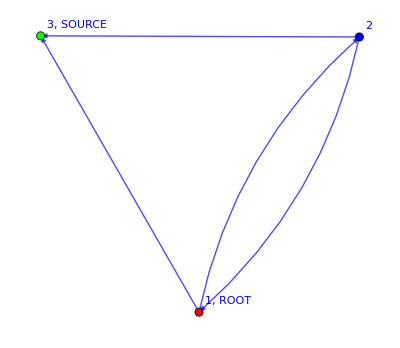

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=1;
source=3;
g=MyGraph[edges,root,source][[1]]
```

```mathematica
fields={ϕ,ψ,ξ,χ};
endTime=1;
Z=Final2DynamicLERWaction["graph"->g,"endTime"->1]/.β[__]->1;
exp1=ExpectationValue[Z ϕs[1,Subscript[t, 1],Subscript[k, 1]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1}]/.γ->"γ_1"
```

ϕs[1,t_2,k_1]-3/4 γ_1 ϕs[1,t_2,k_1]+1/4 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_2,k_2] ψs[1,t_2,l_1]+1/2 γ_1 R[1,3,RGBColor[1, 0, 0]] ϕs[3,t_2,k_3] ψs[1,t_2,l_1]

```mathematica
exp1/.Subscript[t, a_]->Subscript[t, a-1];
exp2=ExpectationValue[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1}]/.γ->"γ_2"
```

(ϕ^*)_(1,t_2,k_1)-3/4 γ_1 (ϕ^*)_(1,t_2,k_1)-3/4 γ_2 (ϕ^*)_(1,t_2,k_1)+9/16 γ_1 γ_2 (ϕ^*)_(1,t_2,k_1)+1/4 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_2,k_2) (ψ^*)_(1,t_2,l_1)-5/16 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_2,k_2) (ψ^*)_(1,t_2,l_1)+1/2 γ_2 R_(1,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_2,k_3) (ψ^*)_(1,t_2,l_1)-3/8 γ_1 γ_2 R_(1,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_2,k_3) (ψ^*)_(1,t_2,l_1)+1/8 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_2,k_3) (ψ^*)_(1,t_2,l_1) (ψ^*)_(2,t_2,l_2)

```mathematica
exp2/.Subscript[t, a_]->Subscript[t, a-1];
exp3=ExpectationValue[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1}]/.γ->"γ_3"
```

(ϕ^*)_(1,t_2,k_1)-3/4 γ_1 (ϕ^*)_(1,t_2,k_1)-3/4 γ_2 (ϕ^*)_(1,t_2,k_1)+9/16 γ_1 γ_2 (ϕ^*)_(1,t_2,k_1)-3/4 γ_3 (ϕ^*)_(1,t_2,k_1)+9/16 γ_1 γ_3 (ϕ^*)_(1,t_2,k_1)+9/16 γ_2 γ_3 (ϕ^*)_(1,t_2,k_1)-27/64 γ_1 γ_2 γ_3 (ϕ^*)_(1,t_2,k_1)+1/4 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_2,k_2) (ψ^*)_(1,t_2,l_1)-3/16 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_2,k_2) (ψ^*)_(1,t_2,l_1)-5/16 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_2,k_2) (ψ^*)_(1,t_2,l_1)+19/64 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_2,k_2) (ψ^*)_(1,t_2,l_1)+1/2 γ_3 R_(1,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_2,k_3) (ψ^*)_(1,t_2,l_1)-3/8 γ_1 γ_3 R_(1,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_2,k_3) (ψ^*)_(1,t_2,l_1)-3/8 γ_2 γ_3 R_(1,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_2,k_3) (ψ^*)_(1,t_2,l_1)+9/32 γ_1 γ_2 γ_3 R_(1,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_2,k_3) (ψ^*)_(1,t_2,l_1)+1/8 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_2,k_3) (ψ^*)_(1,t_2,l_1) (ψ^*)_(2,t_2,l_2)-5/32 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_2,k_3) (ψ^*)_(1,t_2,l_1) (ψ^*)_(2,t_2,l_2)

```mathematica
expLERW/.R[__]->1/.ψs[__]->1/.ϕs[__]->1
```

1.06231×10^-7

```mathematica
0.+7.03777380359998*^-8+8.921121722873217*^-9 +2.390187329524522*^-8 +3.029814924749394*^-9
```

1.06231×10^-7

γ=0.5

```mathematica
expLERW2=Convergence[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->{ϕ,ψ,ξ,χ},"steps"->100,"precision"->10^-7,"theory"->"LERW","gammaValue"->0.5]
```

########## i=1, 0.625 ############

########## i=2, 0.390625 ############

########## i=3, 0.244141 ############

########## i=4, 0.152588 ############

########## i=5, 0.0953674 ############

########## i=6, 0.0596046 ############

########## i=7, 0.0372529 ############

########## i=8, 0.0232831 ############

########## i=9, 0.0145519 ############

########## i=10, 0.00909495 ############

########## i=11, 0.00568434 ############

########## i=12, 0.00355271 ############

########## i=13, 0.00222045 ############

########## i=14, 0.00138778 ############

########## i=15, 0.000867362 ############

########## i=16, 0.000542101 ############

########## i=17, 0.000338813 ############

########## i=18, 0.000211758 ############

########## i=19, 0.000132349 ############

########## i=20, 0.0000827181 ############

########## i=21, 0.0000516988 ############

########## i=22, 0.0000323117 ############

########## i=23, 0.0000201948 ############

########## i=24, 0.0000126218 ############

########## i=25,           -6
7.88861 10 ############

########## i=26,           -6
4.93038 10 ############

########## i=27,           -6
3.08149 10 ############

########## i=28,           -6
1.92593 10 ############

########## i=29,           -6
1.20371 10 ############

########## i=30,           -7
7.52316 10 ############

########## i=31,           -7
4.70198 10 ############

########## i=32,           -7
2.93874 10 ############

########## i=33,           -7
1.83671 10 ############

########## i=34,           -7
1.14795 10 ############

########## i=35,           -8
7.17468 10 ############

7.17482×10^-8 ϕs[1,t_1,k_1]+1.02491×10^-8 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,l_1]+2.86982×10^-8 R[1,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,l_1]+4.09989×10^-9 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,l_1] ψs[2,t_1,l_2]

```mathematica
expLERW3=Convergence[expLERW2,"graph"->g,"fields"->{ϕ,ψ,ξ,χ},"steps"->100,"precision"->10^-9,"theory"->"LERW","gammaValue"->0.5]
```

########## i=1,           -8
4.48426 10 ############

########## i=2,           -8
2.80266 10 ############

########## i=3,           -8
1.75167 10 ############

########## i=4,           -8
1.09479 10 ############

########## i=5,           -9
6.84244 10 ############

########## i=6,           -9
4.27653 10 ############

########## i=7,           -9
2.67283 10 ############

########## i=8,           -9
1.67052 10 ############

########## i=9,           -9
1.04407 10 ############

########## i=10,           -10
6.52546 10 ############

0.+6.52546×10^-10 (ϕ^*)_(1,t_1,k_1)+9.32209×10^-11 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_1,k_2) (ψ^*)_(1,t_1,l_1)+2.61018×10^-10 R_(1,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_1,k_3) (ψ^*)_(1,t_1,l_1)+3.72884×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_1,k_3) (ψ^*)_(1,t_1,l_1) (ψ^*)_(2,t_1,l_2)

```mathematica
a0=(Coefficient[expLERW2, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0);
a12=(Coefficient[expLERW2, R[1,2,Red]ϕs[2,Subscript[t, 1],Subscript[k, 2]] ]/.ψs[__]->1);
a13=(Coefficient[expLERW2, R[1,3,Red]ϕs[3,Subscript[t, 1],Subscript[k, 3]] ]/.ψs[__]->1);
a123=(Coefficient[expLERW2, R[2,3,Red]ϕs[3,Subscript[t, 1],Subscript[k, 3]] ]/.ψs[__]->1/.R[__]->1);
a12/a0
a13/a0
a123/a0
```

0.142848

0.399985

0.0571427

```mathematica
expLERW3=Convergence[expLERW2,"graph"->g,"fields"->{ϕ,ψ,ξ,χ},"steps"->100,"precision"->10^-7,"theory"->"LERW","gammaValue"->0.1]
```

########## i=1, 0.000380465 ############

########## i=2, 0.00035193 ############

########## i=3, 0.000325536 ############

########## i=4, 0.00030112 ############

########## i=5, 0.000278536 ############

########## i=6, 0.000257646 ############

########## i=7, 0.000238323 ############

########## i=8, 0.000220448 ############

########## i=9, 0.000203915 ############

########## i=10, 0.000188621 ############

########## i=11, 0.000174475 ############

########## i=12, 0.000161389 ############

########## i=13, 0.000149285 ############

########## i=14, 0.000138089 ############

########## i=15, 0.000127732 ############

########## i=16, 0.000118152 ############

########## i=17, 0.000109291 ############

########## i=18, 0.000101094 ############

########## i=19, 0.0000935118 ############

########## i=20, 0.0000864984 ############

########## i=21, 0.000080011 ############

########## i=22, 0.0000740102 ############

########## i=23, 0.0000684594 ############

########## i=24, 0.000063325 ############

########## i=25, 0.0000585756 ############

########## i=26, 0.0000541824 ############

########## i=27, 0.0000501187 ############

########## i=28, 0.0000463598 ############

########## i=29, 0.0000428828 ############

########## i=30, 0.0000396666 ############

########## i=31, 0.0000366916 ############

########## i=32, 0.0000339398 ############

########## i=33, 0.0000313943 ############

########## i=34, 0.0000290397 ############

########## i=35, 0.0000268617 ############

########## i=36, 0.0000248471 ############

########## i=37, 0.0000229836 ############

########## i=38, 0.0000212598 ############

########## i=39, 0.0000196653 ############

########## i=40, 0.0000181904 ############

########## i=41, 0.0000168261 ############

########## i=42, 0.0000155642 ############

########## i=43, 0.0000143969 ############

########## i=44, 0.0000133171 ############

########## i=45, 0.0000123183 ############

########## i=46, 0.0000113944 ############

########## i=47, 0.0000105399 ############

########## i=48,           -6
9.74937 10 ############

########## i=49,           -6
9.01817 10 ############

########## i=50,          -6
8.3418 10 ############

########## i=51,           -6
7.71617 10 ############

########## i=52,           -6
7.13746 10 ############

########## i=53,           -6
6.60215 10 ############

########## i=54,           -6
6.10699 10 ############

########## i=55,           -6
5.64896 10 ############

########## i=56,           -6
5.22529 10 ############

########## i=57,          -6
4.8334 10 ############

########## i=58,           -6
4.47089 10 ############

########## i=59,           -6
4.13558 10 ############

########## i=60,           -6
3.82541 10 ############

########## i=61,          -6
3.5385 10 ############

########## i=62,           -6
3.27312 10 ############

########## i=63,           -6
3.02763 10 ############

########## i=64,           -6
2.80056 10 ############

########## i=65,           -6
2.59052 10 ############

########## i=66,           -6
2.39623 10 ############

########## i=67,           -6
2.21651 10 ############

########## i=68,           -6
2.05028 10 ############

########## i=69,           -6
1.89651 10 ############

########## i=70,           -6
1.75427 10 ############

########## i=71,          -6
1.6227 10 ############

########## i=72,         -6
1.501 10 ############

########## i=73,           -6
1.38842 10 ############

########## i=74,           -6
1.28428 10 ############

########## i=75,           -6
1.18798 10 ############

########## i=76,           -6
1.09887 10 ############

########## i=77,           -6
1.01645 10 ############

########## i=78,           -7
9.40234 10 ############

########## i=79,           -7
8.69714 10 ############

########## i=80,          -7
8.0448 10 ############

########## i=81,           -7
7.44145 10 ############

########## i=82,          -7
6.8832 10 ############

########## i=83,           -7
6.36697 10 ############

########## i=84,           -7
5.88954 10 ############

########## i=85,           -7
5.44831 10 ############

########## i=86,           -7
5.03934 10 ############

########## i=87,           -7
4.66143 10 ############

########## i=88,          -7
4.3119 10 ############

########## i=89,           -7
3.98866 10 ############

########## i=90,           -7
3.68944 10 ############

########## i=91,           -7
3.41262 10 ############

########## i=92,           -7
3.15644 10 ############

########## i=93,           -7
2.92009 10 ############

########## i=94,           -7
2.70138 10 ############

########## i=95,           -7
2.49835 10 ############

########## i=96,           -7
2.31132 10 ############

########## i=97,           -7
2.13842 10 ############

########## i=98,          -7
1.9779 10 ############

########## i=99,           -7
1.82921 10 ############

########## i=100,           -7
1.69222 10 ############

γ=0.45

```mathematica
expLERW45=Convergence[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->{ϕ,ψ,ξ,χ},"steps"->100,"precision"->10^-7,"theory"->"LERW","gammaValue"->0.45]
```

########## i=1, 0.6625 ############

########## i=2, 0.438906 ############

########## i=3, 0.290775 ############

########## i=4, 0.192639 ############

########## i=5, 0.127623 ############

########## i=6, 0.0845503 ############

########## i=7, 0.0560146 ############

########## i=8, 0.0371097 ############

########## i=9, 0.0245852 ############

########## i=10, 0.0162877 ############

########## i=11, 0.0107906 ############

########## i=12, 0.00714876 ############

########## i=13, 0.00473605 ############

########## i=14, 0.00313763 ############

########## i=15, 0.00207868 ############

########## i=16, 0.00137713 ############

########## i=17, 0.000912347 ############

########## i=18, 0.00060443 ############

########## i=19, 0.000400435 ############

########## i=20, 0.000265288 ############

########## i=21, 0.000175753 ############

########## i=22, 0.000116437 ############

########## i=23, 0.0000771392 ############

########## i=24, 0.0000511047 ############

########## i=25, 0.0000338569 ############

########## i=26, 0.0000224302 ############

########## i=27, 0.00001486 ############

########## i=28,           -6
9.84475 10 ############

########## i=29,           -6
6.52215 10 ############

########## i=30,           -6
4.32092 10 ############

########## i=31,           -6
2.86261 10 ############

########## i=32,           -6
1.89648 10 ############

########## i=33,           -6
1.25642 10 ############

########## i=34,           -7
8.32377 10 ############

########## i=35,          -7
5.5145 10 ############

########## i=36,           -7
3.65335 10 ############

########## i=37,           -7
2.42036 10 ############

########## i=38,           -7
1.60348 10 ############

########## i=39,           -7
1.06235 10 ############

########## i=40,          -8
7.0382 10 ############

7.03858×10^-8 (ϕ^*)_(1,t_1,k_1)+8.92055×10^-9 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_1,k_2) (ψ^*)_(1,t_1,l_1)+2.39052×10^-8 R_(1,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_1,k_3) (ψ^*)_(1,t_1,l_1)+3.02998×10^-9 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_1,k_3) (ψ^*)_(1,t_1,l_1) (ψ^*)_(2,t_1,l_2)

```mathematica
expLERW45=Convergence[expLERW45,"graph"->g,"fields"->{ϕ,ψ,ξ,χ},"steps"->100,"precision"->10^-9,"theory"->"LERW","gammaValue"->0.45]
```

########## i=1,           -8
4.66306 10 ############

########## i=2,           -8
3.08928 10 ############

########## i=3,           -8
2.04665 10 ############

########## i=4,          -8
1.3559 10 ############

########## i=5,           -9
8.98286 10 ############

########## i=6,           -9
5.95114 10 ############

########## i=7,           -9
3.94263 10 ############

########## i=8,           -9
2.61199 10 ############

########## i=9,           -9
1.73045 10 ############

########## i=10,           -9
1.14642 10 ############

########## i=11,           -10
7.59503 10 ############

0.+7.59503×10^-10 (ϕ^*)_(1,t_1,k_1)+9.62751×10^-11 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_1,k_2) (ψ^*)_(1,t_1,l_1)+2.57945×10^-10 R_(1,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_1,k_3) (ψ^*)_(1,t_1,l_1)+3.26972×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_1,k_3) (ψ^*)_(1,t_1,l_1) (ψ^*)_(2,t_1,l_2)

```mathematica
expLERW45=Convergence[expLERW45,"graph"->g,"fields"->{ϕ,ψ,ξ,χ},"steps"->100,"precision"->10^-12,"theory"->"LERW","gammaValue"->0.45]
```

########## i=1,           -11
6.42163 10 ############

########## i=2,           -11
4.25433 10 ############

########## i=3,           -11
2.81849 10 ############

########## i=4,           -11
1.86725 10 ############

########## i=5,           -11
1.23705 10 ############

########## i=6,           -12
8.19548 10 ############

########## i=7,           -12
5.42951 10 ############

########## i=8,           -12
3.59705 10 ############

########## i=9,           -12
2.38304 10 ############

########## i=10,           -12
1.57877 10 ############

########## i=11,           -12
1.04593 10 ############

########## i=12,           -13
6.92931 10 ############

0.+6.92931×10^-13 (ϕ^*)_(1,t_1,k_1)+8.78363×10^-14 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_1,k_2) (ψ^*)_(1,t_1,l_1)+2.35335×10^-13 R_(1,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_1,k_3) (ψ^*)_(1,t_1,l_1)+2.98312×10^-14 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_1,k_3) (ψ^*)_(1,t_1,l_1) (ψ^*)_(2,t_1,l_2)

```mathematica
a0=(Coefficient[expLERW45, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0);
a12=(Coefficient[expLERW45, R[1,2,Red]ϕs[2,Subscript[t, 1],Subscript[k, 2]] ]/.ψs[__]->1);
a13=(Coefficient[expLERW45, R[1,3,Red]ϕs[3,Subscript[t, 1],Subscript[k, 3]] ]/.ψs[__]->1);
a123=(Coefficient[expLERW45, R[2,3,Red]ϕs[3,Subscript[t, 1],Subscript[k, 3]] ]/.ψs[__]->1/.R[__]->1);
```

```mathematica
(a123+a13)/a0
```

0.382673

```mathematica
a12/a0
```

0.126761

```mathematica
expLERW3=Convergence[expLERW2,"graph"->g,"fields"->{ϕ,ψ,ξ,χ},"steps"->100,"precision"->10^-7,"theory"->"LERW","gammaValue"->0.1]
```

########## i=1, 0.000380465 ############

########## i=2, 0.00035193 ############

########## i=3, 0.000325536 ############

########## i=4, 0.00030112 ############

########## i=5, 0.000278536 ############

########## i=6, 0.000257646 ############

########## i=7, 0.000238323 ############

########## i=8, 0.000220448 ############

########## i=9, 0.000203915 ############

########## i=10, 0.000188621 ############

########## i=11, 0.000174475 ############

########## i=12, 0.000161389 ############

########## i=13, 0.000149285 ############

########## i=14, 0.000138089 ############

########## i=15, 0.000127732 ############

########## i=16, 0.000118152 ############

########## i=17, 0.000109291 ############

########## i=18, 0.000101094 ############

########## i=19, 0.0000935118 ############

########## i=20, 0.0000864984 ############

########## i=21, 0.000080011 ############

########## i=22, 0.0000740102 ############

########## i=23, 0.0000684594 ############

########## i=24, 0.000063325 ############

########## i=25, 0.0000585756 ############

########## i=26, 0.0000541824 ############

########## i=27, 0.0000501187 ############

########## i=28, 0.0000463598 ############

########## i=29, 0.0000428828 ############

########## i=30, 0.0000396666 ############

########## i=31, 0.0000366916 ############

########## i=32, 0.0000339398 ############

########## i=33, 0.0000313943 ############

########## i=34, 0.0000290397 ############

########## i=35, 0.0000268617 ############

########## i=36, 0.0000248471 ############

########## i=37, 0.0000229836 ############

########## i=38, 0.0000212598 ############

########## i=39, 0.0000196653 ############

########## i=40, 0.0000181904 ############

########## i=41, 0.0000168261 ############

########## i=42, 0.0000155642 ############

########## i=43, 0.0000143969 ############

########## i=44, 0.0000133171 ############

########## i=45, 0.0000123183 ############

########## i=46, 0.0000113944 ############

########## i=47, 0.0000105399 ############

########## i=48,           -6
9.74937 10 ############

########## i=49,           -6
9.01817 10 ############

########## i=50,          -6
8.3418 10 ############

########## i=51,           -6
7.71617 10 ############

########## i=52,           -6
7.13746 10 ############

########## i=53,           -6
6.60215 10 ############

########## i=54,           -6
6.10699 10 ############

########## i=55,           -6
5.64896 10 ############

########## i=56,           -6
5.22529 10 ############

########## i=57,          -6
4.8334 10 ############

########## i=58,           -6
4.47089 10 ############

########## i=59,           -6
4.13558 10 ############

########## i=60,           -6
3.82541 10 ############

########## i=61,          -6
3.5385 10 ############

########## i=62,           -6
3.27312 10 ############

########## i=63,           -6
3.02763 10 ############

########## i=64,           -6
2.80056 10 ############

########## i=65,           -6
2.59052 10 ############

########## i=66,           -6
2.39623 10 ############

########## i=67,           -6
2.21651 10 ############

########## i=68,           -6
2.05028 10 ############

########## i=69,           -6
1.89651 10 ############

########## i=70,           -6
1.75427 10 ############

########## i=71,          -6
1.6227 10 ############

########## i=72,         -6
1.501 10 ############

########## i=73,           -6
1.38842 10 ############

########## i=74,           -6
1.28428 10 ############

########## i=75,           -6
1.18798 10 ############

########## i=76,           -6
1.09887 10 ############

########## i=77,           -6
1.01645 10 ############

########## i=78,           -7
9.40234 10 ############

########## i=79,           -7
8.69714 10 ############

########## i=80,          -7
8.0448 10 ############

########## i=81,           -7
7.44145 10 ############

########## i=82,          -7
6.8832 10 ############

########## i=83,           -7
6.36697 10 ############

########## i=84,           -7
5.88954 10 ############

########## i=85,           -7
5.44831 10 ############

########## i=86,           -7
5.03934 10 ############

########## i=87,           -7
4.66143 10 ############

########## i=88,          -7
4.3119 10 ############

########## i=89,           -7
3.98866 10 ############

########## i=90,           -7
3.68944 10 ############

########## i=91,           -7
3.41262 10 ############

########## i=92,           -7
3.15644 10 ############

########## i=93,           -7
2.92009 10 ############

########## i=94,           -7
2.70138 10 ############

########## i=95,           -7
2.49835 10 ############

########## i=96,           -7
2.31132 10 ############

########## i=97,           -7
2.13842 10 ############

########## i=98,          -7
1.9779 10 ############

########## i=99,           -7
1.82921 10 ############

########## i=100,           -7
1.69222 10 ############

Smaller favorite graph

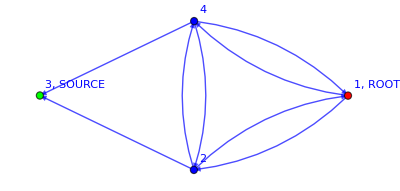

```mathematica
Edges={{1,2},{1,4},{2,3},{2,4},{4,3}};
root=1;
Source=3;
g=MyGraph[Edges,root,Source][[1]]
```

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Convergence

```mathematica
g=myFavoriteGraph;
expLERW=Convergence[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->{ϕ,ψ,ξ,χ},"steps"->5,"precision"->10^-7,"theory"->"LERW","gammaValue"->0.45]
```

PropertyValue::pvobj: myFavoriteGraph is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~ROOT].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

Part::partw: Part 1 of PropertyValue[] does not exist.

PropertyValue::pvobj: myFavoriteGraph is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~SOURCE].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

General::stop: Further output of PropertyValue::argrx will be suppressed during this calculation.

Part::partw: Part 1 of PropertyValue[] does not exist.

Part::partd: Part specification WeightedAdjacencyMatrix[myFavoriteGraph]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

########## i=1, 0 ############

ϕs[1,t_1,k_1]

```mathematica
expLERW
```

0.969444 (ϕ^*)_(1,t_1,k_1)+0.0138889 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_1,k_2) (ψ^*)_(1,t_2,j_-1)+0.0166667 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(5,t_1,k_5) (ψ^*)_(1,t_2,j_-1)

Partition Function

```mathematica
g=myFavoriteGraph;
endTime=1;
Z=FinalDynamicLERWaction["graph"->g,"endTime"->endTime]
```

V[1+ϕ_(1,t_2,0)] V[1+ϕ_(2,t_2,0)] V[1+ϕ_(3,t_2,0)] V[1+ϕ_(4,t_2,0)] V[1+ϕ_(5,t_2,0)] V[1+ψ_(1,t_2,j_-1)] V[1+ψ_(2,t_2,j_-1)] V[1+ψ_(3,t_2,j_-1)] V[1+ψ_(4,t_2,j_-1)] V[1+ψ_(5,t_2,j_-1)] V[1+ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1)+(R_(1,2,RGBColor[0, 0, 1]) β_(1,2) χ_(1,t_1,i_1) (χ^*)_(2,t_1,i_1))/(β_(1,2)+β_(1,5))+(R_(1,5,RGBColor[0, 0, 1]) β_(1,5) χ_(1,t_1,i_1) (χ^*)_(5,t_1,i_1))/(β_(1,2)+β_(1,5))+ψ_(1,t_1,j_-1) (ψ^*)_(1,t_2,j_-1)+γ ((R_(1,2,RGBColor[1, 0, 0]) β_(1,2) ϕ_(1,t_1,k_1) χ_(4,t_1,1) (χ^*)_(2,t_1,1) (-(ϕ^*)_(1,t_2,k_1)+(ϕ^*)_(2,t_2,k_1) (ψ^*)_(1,t_2,j_-1)))/(β_(1,2)+β_(1,5))+(R_(1,5,RGBColor[1, 0, 0]) β_(1,5) ϕ_(1,t_1,k_1) χ_(4,t_1,1) (χ^*)_(5,t_1,1) (-(ϕ^*)_(1,t_2,k_1)+(ϕ^*)_(5,t_2,k_1) (ψ^*)_(1,t_2,j_-1)))/(β_(1,2)+β_(1,5)))] V[1+ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2)+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,t_1,i_2) (χ^*)_(1,t_1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,t_1,i_2) (χ^*)_(3,t_1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,t_1,i_2) (χ^*)_(5,t_1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+ψ_(2,t_1,j_-1) (ψ^*)_(2,t_2,j_-1)+γ ((R_(2,1,RGBColor[1, 0, 0]) β_(2,1) ϕ_(2,t_1,k_2) χ_(4,t_1,1) (χ^*)_(1,t_1,1) (-(ϕ^*)_(2,t_2,k_2)+(ϕ^*)_(1,t_2,k_2) (ψ^*)_(2,t_2,j_-1)))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[1, 0, 0]) β_(2,3) ϕ_(2,t_1,k_2) χ_(4,t_1,1) (χ^*)_(3,t_1,1) (-(ϕ^*)_(2,t_2,k_2)+(ϕ^*)_(3,t_2,k_2) (ψ^*)_(2,t_2,j_-1)))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[1, 0, 0]) β_(2,5) ϕ_(2,t_1,k_2) χ_(4,t_1,1) (χ^*)_(5,t_1,1) (-(ϕ^*)_(2,t_2,k_2)+(ϕ^*)_(5,t_2,k_2) (ψ^*)_(2,t_2,j_-1)))/(β_(2,1)+β_(2,3)+β_(2,5)))] V[1+ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3)+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,t_1,i_3) (χ^*)_(2,t_1,i_3))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,t_1,i_3) (χ^*)_(4,t_1,i_3))/(β_(3,2)+β_(3,4))+ψ_(3,t_1,j_-1) (ψ^*)_(3,t_2,j_-1)+γ ((R_(3,2,RGBColor[1, 0, 0]) β_(3,2) ϕ_(3,t_1,k_3) χ_(4,t_1,1) (χ^*)_(2,t_1,1) (-(ϕ^*)_(3,t_2,k_3)+(ϕ^*)_(2,t_2,k_3) (ψ^*)_(3,t_2,j_-1)))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[1, 0, 0]) β_(3,4) ϕ_(3,t_1,k_3) χ_(4,t_1,1) (χ^*)_(4,t_1,1) (-(ϕ^*)_(3,t_2,k_3)+(ϕ^*)_(4,t_2,k_3) (ψ^*)_(3,t_2,j_-1)))/(β_(3,2)+β_(3,4)))] V[1+ϕ_(5,t_1,k_5) (ϕ^*)_(5,t_2,k_5)+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,t_1,i_5) (χ^*)_(1,t_1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,t_1,i_5) (χ^*)_(2,t_1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,t_1,i_5) (χ^*)_(4,t_1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+ψ_(5,t_1,j_-1) (ψ^*)_(5,t_2,j_-1)+γ ((R_(5,1,RGBColor[1, 0, 0]) β_(5,1) ϕ_(5,t_1,k_5) χ_(4,t_1,1) (χ^*)_(1,t_1,1) (-(ϕ^*)_(5,t_2,k_5)+(ϕ^*)_(1,t_2,k_5) (ψ^*)_(5,t_2,j_-1)))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[1, 0, 0]) β_(5,2) ϕ_(5,t_1,k_5) χ_(4,t_1,1) (χ^*)_(2,t_1,1) (-(ϕ^*)_(5,t_2,k_5)+(ϕ^*)_(2,t_2,k_5) (ψ^*)_(5,t_2,j_-1)))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[1, 0, 0]) β_(5,4) ϕ_(5,t_1,k_5) χ_(4,t_1,1) (χ^*)_(4,t_1,1) (-(ϕ^*)_(5,t_2,k_5)+(ϕ^*)_(4,t_2,k_5) (ψ^*)_(5,t_2,j_-1)))/(β_(5,1)+β_(5,2)+β_(5,4)))]

Observable Op[ϕs[1,t_1,0]]

```mathematica
fields={ϕ,ψ,χ};
startingTime=1;
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicLERWaction["graph"->g,"startingTime"->startingTime,"endTime"->endTime];
exp=ExpectationValue[Z Op[Subscript[SuperStar[ϕ], 1,Subscript[t, 1],0]],"endTime"->endTime+1,"fields"->fields,"draw"->False,"Rrule"->{}]

(*Dexp=D[exp,γ]/.γ->0*)
```

###################  Operator found  ##################

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp*18/13/.β[__]->1/.R[__,Blue]->1/.γ->2 γ//Expand
```

1-(11 γ)/13+5/13 γ R_(1,2,RGBColor[1, 0, 0])+6/13 γ R_(1,5,RGBColor[1, 0, 0])

```mathematica
%/.R[__,Red]->1
```

1

```mathematica
(*Dexp=D[exp,γ]/.γ->0;*)
exp2=exp/.R[a_,b_,Red]->R[a,b,Red]Op[ϕs[b,Subscript[t, 1],0]ψs[a,Subscript[t, 1],Subscript[j, -1]]]
```

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp=ExpectationValue[Z exp2,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
```

###################  Partition Function  ##################

1-(R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))+(R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 β_(2,3)^2 β_(3,2)^2)/((β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)+(γ R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3)^2 β_(3,2) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)-(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,3)^2 β_(3,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)+(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,3)^2 β_(3,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)+(R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(1,2) β_(2,1) β_(2,3) β_(3,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)))-(2 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2)^2 β_(2,1) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1])^2 R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(2,5)^2 β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(1,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,5) β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,3)^2 β_(3,2) β_(3,4) β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(2,5) β_(3,2) β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,3) β_(2,5) β_(3,4) β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,3) β_(3,4) β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])^2 β_(1,5) β_(2,1) β_(2,5) β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(2,5,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1])^2 β_(2,5)^2 β_(5,2)^2)/((β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])^2 β_(1,5)^2 β_(2,1) β_(2,3) β_(3,4) β_(5,2)^2)/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])^2 β_(1,5) β_(2,3) β_(2,5) β_(3,4) β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5)^2 β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1])^2 R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2)^2 β_(2,5)^2 β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,5) β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,5) β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,3)^2 β_(3,2)^2 β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,3) β_(2,5) β_(3,2) β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,3) β_(2,5) β_(3,2) β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(2 γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,3) β_(3,2) β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,1) β_(2,5) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(2,5,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5)^2 β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,1) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,5) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,1) β_(2,3) β_(3,2) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(2,5) β_(3,2) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,5)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,5)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(2 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(2 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3) β_(3,2) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(R_(1,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,1))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(2 R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2)^2 β_(2,3) β_(2,5) β_(3,4) β_(5,1))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,3) β_(3,4) β_(5,1))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(2,1) β_(2,5) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(2 R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,1) β_(2,3) β_(3,2) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(2 R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,3) β_(2,5) β_(3,2) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,1) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,1) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2)^2 β_(2,1) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,1) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(2 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(2 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
comp=exp*18/13/.β[__]->1/.R[__,Blue]->1/.γ->2 γ//Expand
```

11/36-(121 γ)/468+5/13 γ R_(1,2,RGBColor[1, 0, 0])-25/117 γ^2 R_(1,2,RGBColor[1, 0, 0])+5/13 γ R_(1,5,RGBColor[1, 0, 0])-4/13 γ^2 R_(1,5,RGBColor[1, 0, 0])+5/39 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0])+10/117 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0])+2/39 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+10/39 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

```mathematica
comp/.γ^n_->γ
```

11/36-(121 γ)/468+20/117 γ R_(1,2,RGBColor[1, 0, 0])+1/13 γ R_(1,5,RGBColor[1, 0, 0])+5/39 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0])+10/117 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0])+2/39 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+10/39 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

```mathematica
Dexp=D[exp,γ]/.γ->0;
exp2=Dexp/.R[a_,b_,Red]R[b_,c_,Red]->R[a,b,Red]R[b,c,Red]Op[ϕs[c,Subscript[t, 1],0]ψs[b,Subscript[t, 1],Subscript[j, -1]]ψs[a,Subscript[t, 1],Subscript[j, -1]]]
```

(Op[(ϕ^*)_(3,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,3)^2 β_(3,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)+(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(Op[(ϕ^*)_(4,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(4,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(4,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,5)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(4,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(2 Op[(ϕ^*)_(4,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3) β_(3,2) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(3,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp=ExpectationValue[Z exp2,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
```

###################  Partition Function  ##################

(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,3)^2 β_(3,4)^3)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^3)+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,3)^2 β_(3,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,5)^2 β_(5,4)^3)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^3)+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^3 R_(5,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^3 β_(3,4)^3 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^3 (β_(3,2)+β_(3,4))^3 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(2,3,RGBColor[1, 0, 0]) R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^3 β_(3,2) β_(3,4)^2 β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^3 (β_(3,2)+β_(3,4))^3 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,5)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4)^2 β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
Dexp=D[exp,γ]/.γ->0;
exp2=Dexp/.R[a_,b_,Red]R[b_,c_,Red]R[c_,d_,Red]->R[a,b,Red]R[b,c,Red]R[c,d,Red]Op[ϕs[c,Subscript[t, 1],0]ψs[c,Subscript[t, 1],Subscript[j, -1]]ψs[b,Subscript[t, 1],Subscript[j, -1]]ψs[a,Subscript[t, 1],Subscript[j, -1]]]
```

(Op[(ϕ^*)_(3,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(3,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,3)^2 β_(3,4)^3)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^3)+(Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,5)^2 β_(5,4)^3)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^3)+(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^3 R_(5,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^3 β_(3,4)^3 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^3 (β_(3,2)+β_(3,4))^3 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(2,3,RGBColor[1, 0, 0]) R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^3 β_(3,2) β_(3,4)^2 β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^3 (β_(3,2)+β_(3,4))^3 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(3,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(3,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4)^2 β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
ExpectationValue[Z Op[Subscript[SuperStar[ϕ], 2,Subscript[t, 1],0] Subscript[SuperStar[ψ], 1,Subscript[t, 1],Subscript[j, -1]]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
```

###################  Operator found  ##################

1

```mathematica
exp/.R[__,Blue]->1/.β[__]->1
```

169/324+25/648 γ R_(1,2,RGBColor[1, 0, 0])+1/54 γ R_(1,5,RGBColor[1, 0, 0])

```mathematica
%/.γ->1/.R[__]->1
```

125/216